```mathematica
(*UNSURE HOW TO DEAL WITH MAJORANA SPINORS HERE!*)
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
On[Assert];

Get["~/dphil/largeNmodels/helpfulFunctions.m"];
AbortAssert[True]
```

FeynCalc 10.0.0 (development version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to correctly cite this work.

True

```mathematica
$FeynArtsDirectory
```

/home/f/fraser-taliente/.Mathematica/Applications/FeynCalc/FeynArts

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.l

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to correctly cite this work.

```mathematica
params={InsertionLevel->{Particles},Model->FileNameJoin[{"Phi4","Phi4"}],GenericModel->FileNameJoin[{"Phi4","Phi4"}]};
top[i_,j_]:=CreateTopologies[1,i->j];
topCT[i_,j_]:=CreateCTTopologies[1,i->j];
topVertex[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{WFCorrections}];
topVertexCT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{WFCorrectionCTs}];
{diagPhi4SE,diagPhi4SECT}=(InsertFields[#1,{S[1]}->{S[1]},Sequence@@params]&)/@{top[1,1],topCT[1,1]};
{diagVertex,diagVertexCT}=(InsertFields[#1,{S[1],S[1]}->{S[1],S[1]},Sequence@@params]&)/@{topVertex[2,2],topVertexCT[2,2]};
```

```mathematica
SetDirectory[NotebookDirectory[]];
QGLoadInsertions[];
```

```mathematica
(*QGLoadInsertions[];
out=QGCreateAmp[2,{"phi[p1]", "phi[p2]", "phi[p3]","phi[q1]","phi[q2]","phi[q3]"}->{},QGLoopMomentum->k,QGOptions->{"onepi","notadpole"},QGModel->"3dFull446",QGShowOutput->False]

gotThemOut=QGConvertToFC[out[[1]],DiracChainJoin->True]
Length[gotThemOut]*)
```

```mathematica
(*QGLoadInsertions[];
out=QGCreateAmp[2,{"phi[p]"}->{"phi[p]"},QGLoopMomentum->k,QGOptions->{"onepi","notadpole"},QGModel->"3dFull446",QGShowOutput->False]

gotThemOut=QGConvertToFC[out[[1]],DiracChainJoin->True]


QGPrepareDiagramsTeX[out[[2]],"dias.tex",Style->"TikZ-Feynman"]*)
(*or QGPrepareDiagramsTeX[out[[2]],"Dias",Split->True]*)
```

```mathematica
(*"CF: For anybody else reading this in the future,both the OP and@JamalS are using the (+−−−) metric signature,which you can tell by the fact that in the original post the kinetic term is+12(∂ϕ)2. The (∂0ϕ)2 term must be positive.Had they chosen the (−+++) signature,the counterterm would be−i(p2δZ+δm)."

https://physics.stackexchange.com/questions/83711/why-does-the-counterterms-propagator-have-inverse-units-of-the-propagator-ph*)
```

```mathematica
phiStruct[i_,j_]:=phidelta[FCMakeIndex["c",{i,j},c]]
psiStruct[i_,j_]:=psidelta[FCMakeIndex["c",{i,j},c]]
gStruct[i_,j_,k_,l_]:=gO[FCMakeIndex["c",{i,j,k,l},c]]
λStruct[b[i_,j_],f[k_,l_]]:=λO[FCMakeIndex["c",{i,j,k,l},c]]
hStruct[i_,j_,k_,l_,m_,n_]:=hO[FCMakeIndex["c",{i,j,k,l,m,n},c]]
```

```mathematica
generatorsOfSymmetricTensor[size_Integer]:=generatorsOfSymmetricTensor[size]={#,1}&/@GroupGenerators@SymmetricGroup[size]; (*memoised*)
gSymmetryGroup = generatorsOfSymmetricTensor[4]
λSymmetryGroup =Join[generatorsOfSymmetricTensor[2],generatorsOfSymmetricTensor[2]/.Cycles[cycl_]->Cycles[cycl+2]]
hSymmetryGroup =generatorsOfSymmetricTensor[6]
symGroupOfIt=<|ϕϕ->generatorsOfSymmetricTensor[2],ψψb->generatorsOfSymmetricTensor[2],g->gSymmetryGroup, λ->{}(*generatorsOfSymmetricTensor[2]*),h->hSymmetryGroup|> 

(*This needs to be carefully selected*)
removeExtsForHead = <|ϕϕb->{"A"->b, "B"->b},ψψb->{"A"->f,"B"->f},g->{"A"->b, "B"->b,"C"->b, "D"->b},λ->{"A"->b, "B"->b,"C"->f, "D"->f},h->{"A"->b, "B"->b,"C"->b, "D"->b, "D"->b, "E"->b}|>

renormalisationPoints=<|ϕϕb->{},ψψb->{},λ->{p1->0,p2->0,q1->0,q2->0},g->{p1->0,p2->0,q1->0,q2->0},h->{p1->0,p2->0,p3->0,q1->0,q2->0,q3->0}|>
orderlessIndices={Subscript[go,{α_,β_,γ_,δ_}]->Subscript[go,{OrderlessPatternSequence[α,β,γ,δ]}],Subscript[λo,{α_,β_,γ_,δ_}]->Subscript[λo,{OrderlessPatternSequence[α,β],OrderlessPatternSequence[γ,δ]}],Subscript[ho,{α_,β_,γ_,δ_,ϵ_,ζ_}]->Subscript[ho,{OrderlessPatternSequence[α,β,γ,δ,ϵ,ζ]}]}; 
(*Permuting phis and phibars*)
turnIntoTensorForm={λO[__]->λo, gO[__]->go,hO[__]->ho}

$Assumptions={(λo|dZλo)∈Arrays[{n,n,n,n}, Reals,λSymmetryGroup],(go|dZgo)∈Arrays[{n,n,n,n}, Reals,gSymmetryGroup],(ho|dZho)∈Arrays[{n,n,n,n,n,n}, Reals,hSymmetryGroup]};
```

(Cycles[(1 | 2)] | 1
Cycles[(1 | 2 | 3 | 4)] | 1)

(Cycles[(1 | 2)] | 1
Cycles[(3 | 4)] | 1)

(Cycles[(1 | 2)] | 1
Cycles[(1 | 2 | 3 | 4 | 5 | 6)] | 1)

<|ϕϕ→(Cycles[(1 | 2)] | 1),ψψb→(Cycles[(1 | 2)] | 1),g→(Cycles[(1 | 2)] | 1
Cycles[(1 | 2 | 3 | 4)] | 1),λ→{},h→(Cycles[(1 | 2)] | 1
Cycles[(1 | 2 | 3 | 4 | 5 | 6)] | 1)|>

<|ϕϕb→{A→b,B→b},ψψb→{A→f,B→f},g→{A→b,B→b,C→b,D→b},λ→{A→b,B→b,C→f,D→f},h→{A→b,B→b,C→b,D→b,D→b,E→b}|>

<|ϕϕb→{},ψψb→{},λ→{p1→0,p2→0,q1→0,q2→0},g→{p1→0,p2→0,q1→0,q2→0},h→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}|>

{λO(__)→λo,gO(__)→go,hO(__)→ho}

```mathematica
insertionsWithSubs={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psi}},{q,qbar}]:>((I DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] FAD[{p,mass}] + ct( DCHN[(GSD[p]+mass).(I dZψ2 GSD[p]-I dZMψ2 M ).(GSD[p]+mass),FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] I^2 FAD[{p,mass}]^2))) psiStruct[i,j],

QGPropagator[scalar_[i_,p_],scalarbar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalarbar}]:>(I FAD[{p,mass}] + ct(I(dZϕ2 Pair[Momentum[p,D],Momentum[p,D]] - (dZmϕ2)m^2)I^2 FAD[{p,mass}]^2))phiStruct[i,j],

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalarbar_[k_,r_],scalarbar_[l_, s_]]/;MemberQ[{{phi, phi}},{scalar,scalarbar}]:> -I g gStruct[i,j,k,l] , 

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalarbar_[l_, s_],scalarbar_[m_,t_],scalarbar_[n_, u_]]/;MemberQ[{{phi,phi}},{scalar,scalarbar}]:> -I h hStruct[i,j,k,l,m,n], 
QGVertex[scalar_[i_, p_],scalarbar_[j_, q_],quark_[k_,r_],quarkbar_[l_, s_]]/;MemberQ[{{phi,phi, psi,psi}},{scalar,scalarbar, quark, quarkbar}]:> -I λ( DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]]) λStruct[b[i,j],f[k,l]], 

(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],MajoranaSpinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1,
QGPolarization[scalarbar_[i_,p_],mass_]/;MemberQ[{{scalarbar}},{phi}]:> 1,
(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psi},qbar]:>DCHN[Spinor[-Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psi},qbar]:>DCHN[FCMakeIndex["QGIDir",i],Spinor[-Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i]
}



insertionsForGraph ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psi}},{q,qbar}]:>psiStruct[i,j],

QGPropagator[scalar_[i_,p_],scalarbar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalarbar}]:>phiStruct[i,j],

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalarbar_[k_,r_],scalarbar_[l_, s_]]/;MemberQ[{{phi, phi}},{scalar,scalarbar}]:> gStruct[i,j,k,l] , 

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalarbar_[l_, s_],scalarbar_[m_,t_],scalarbar_[n_, u_]]/;MemberQ[{{phi}},{scalar}]:> hStruct[i,j,k,l,m,n], 
QGVertex[scalar_[i_, p_],scalarbar_[j_, q_],quark_[k_,r_],quarkbar_[l_, s_]]/;MemberQ[{{phi,phi, psi,psi}},{scalar,scalarbar, quark, quarkbar}]:>   λStruct[b[i,j],f[k,l]], 


(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>ext[psiin[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>ext[psiout[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psi},qbar]:>ext[psiin[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psi},qbar]:>ext[psiout[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i],

QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{phi},scalar]:> ext[phiin[FCMakeIndex["c",i,c]]]/;OddQ[i], (*Distinguished by Odd or Even*)
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{phi},scalar]:> ext[phiout[FCMakeIndex["c",i,c]]]/;EvenQ[i],
QGPolarization[scalarbar_[i_,p_],mass_]/;MemberQ[{phi},scalarbar]:> ext[phiin[FCMakeIndex["c",i,c]]]/;OddQ[i],
QGPolarization[scalarbar_[i_,p_],mass_]/;MemberQ[{phi},scalarbar]:> ext[phiout[FCMakeIndex["c",i,c]]]/;EvenQ[i]
};

structureHeads=DeleteCases[ Head[#[[2]]]&/@insertionsForGraph,Condition]
```

{QGPropagator(q_(i_,p_),qbar_(j_,_),mass_)/;MemberQ[(El | Ael
Mu | Amu
Tau | Atau
psi | psi),{q,qbar}]:>psiStruct(i,j) (ct (ⅈ^2 (1/(p^2-mass^2))^2 ((mass+γ·p).(ⅈ dZψ2 γ·p-ⅈ dZMψ2 M).(mass+γ·p))_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))+(ⅈ (mass+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-mass^2)),QGPropagator(scalar_(i_,p_),scalarbar_(j_,_),mass_)/;MemberQ[(phi | phi),{scalar,scalarbar}]:>phiStruct(i,j) (ct (ⅈ ⅈ^2 (1/(p^2-mass^2))^2 (dZϕ2 p^2-dZmϕ2 m^2))+ⅈ/(p^2-mass^2)),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalarbar_(k_,r_),scalarbar_(l_,s_))/;MemberQ[(phi | phi),{scalar,scalarbar}]:>-ⅈ g gStruct(i,j,k,l),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalarbar_(l_,s_),scalarbar_(m_,t_),scalarbar_(n_,u_))/;MemberQ[(phi | phi),{scalar,scalarbar}]:>-ⅈ h hStruct(i,j,k,l,m,n),QGVertex(scalar_(i_,p_),scalarbar_(j_,q_),quark_(k_,r_),quarkbar_(l_,s_))/;MemberQ[(phi | phi | psi | psi),{scalar,scalarbar,quark,quarkbar}]:>-ⅈ λ δ_(FCMakeIndex(QGIDir,k)FCMakeIndex(QGIDir,l)) λStruct(b(i,j),f(k,l)),QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧OddQ[i],QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧EvenQ[i],QGPolarization(scalar_(i_,p_),mass_)/;MemberQ[(scalar),{phi}]:>1,QGPolarization(scalarbar_(i_,p_),mass_)/;MemberQ[(scalarbar),{phi}]:>1,QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psi},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧OddQ[i],QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psi},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧EvenQ[i]}

{psidelta,phidelta,gO,hO,λO}

```mathematica
makeGraph[graph_]:=Module[{(*externals,edges,vertices,deltaMaps,extMaps, fixed*)externalLocations},
externals =Sort@Cases[graph, ext[__]];
edges = Cases[graph,phidelta[__]|psidelta[__]];
vertices = Cases[graph,hO[__]|gO[__]|λO[__]];
deltaMaps =Join@@(Thread[Rest[#[[1]]]->First[#[[1]]]] &/@vertices);

extMaps ={ext[phiin[a_]]:>DirectedEdge[ext[phiin[a ]],a/.deltaMaps, ϕ],
ext[phiout[a_]]:>DirectedEdge[a/.deltaMaps,ext[phiout[a]], ϕ],
ext[psiin[a_]]:>DirectedEdge[ext[psiin[a]],a/.deltaMaps,ψ],
ext[psiout[a_]]:>DirectedEdge[a/.deltaMaps,ext[psiout[a]], ψ],
ext[psibarin[a_]]:>DirectedEdge[a/.deltaMaps,ext[psibarin[a]], ψ],
ext[psibarout[a_]]:>DirectedEdge[ext[psibarout[a]],a/.deltaMaps,ψ]
};
propMaps = {
phidelta[{a_,b_}]->DirectedEdge[a,b,ϕ],
psidelta[{a_,b_}]->DirectedEdge[a,b,ψ]
};
fixed=Join[edges/.deltaMaps,(externals/.extMaps)];
graphNoAnnotations=Graph[fixed/.propMaps,EdgeStyle->{DirectedEdge[a_,b_,ϕ]->{Black,Dashed},DirectedEdge[a_,b_,ψ]->{Black}}];
externalLocations = If[Length[externals]===2,
{externals[[1]]->{0,0},externals[[2]]->{1,0}}
,
(*Else, assume 4:*)
{externals[[1]]->{0,0},externals[[2]]->{1,0}, externals[[3]]->{0,1}, externals[[2]]->{1,1}}
];
Graph[graphNoAnnotations,VertexLabels->Join[(#->First[#]&/@externals ),#[[1,1]]->Head[#]&/@vertices],VertexCoordinates->externalLocations]
];
```

```mathematica
Print/@ReadList[Directory[]<>"/3dReal446.mod", String]
```

[ model = '3D complex Yukawa' ]

% Propagators:

[phi, phi, +;  mass='m']

[psi, psi, -; mass='M']

% Vertices:

[phi, phi, phi, phi]

[phi, phi, phi, phi,phi, phi]

[phi,phi, psi, psi]

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
stdQGCreateAmp[nLoops_,input_]:=QGCreateAmp[nLoops,input,QGLoopMomentum->k,QGModel->Directory[]<>"/3dReal446.mod",QGOptions->{"onepi","notadpole"},QGShowOutput->False,QGAmplitudeStyle->"./feyncalcWithTop.sty"];
makePhiPhi[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p]"}->{"phi[p]"}];
results = {ϕϕb,nLoops}->runFinal[{ϕϕb,nLoops},done];
PutAppend[results,"/tmp/3dReal446.out"];
results
];
makePsiPsi[nLoops_]:=Module[{done,results}, 
 done=stdQGCreateAmp[nLoops,{"psi[p]"}->{"psi[p]"}];
results = {ψψb,nLoops}->runFinal[{ψψb,nLoops},done];
PutAppend[results,"/tmp/3dReal446.out"];
results
];

makeLam[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "psi[p2]"}->{"phi[q1]","psi[q2]"}];
results = {λ,nLoops}->runFinal[{λ,nLoops},done];
PutAppend[results,"/tmp/3dReal446.out"];
results
];
makeg[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "phi[p2]"}->{"phi[q1]","phi[q2]"}];
results = {g,nLoops}->runFinal[{g,nLoops},done];
PutAppend[results,"/tmp/3dReal446.out"];
results
];
makeh[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "phi[p2]", "phi[p3]"}->{"phi[q1]","phi[q2]","phi[q3]"}];
results = {h,nLoops}->runFinal[{h,nLoops},done];
PutAppend[results,"/tmp/3dReal446.out"];
results
];
```

```mathematica
traceRules={DiracTrace[1] -> Tr1s, DiracTrace[DiracGamma[Momentum[k1_, D], D]] -> 0,  DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D]] -> Tr1s*Pair[Momentum[mom1, D], Momentum[mom2, D]],(*DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D] . DiracGamma[Momentum[mom3_, D], D]] -> 2*Tr3[Momentum[mom1, D], Momentum[mom2, D], Momentum[mom3, D]],*)DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D] . DiracGamma[Momentum[mom3_, D], D] . DiracGamma[Momentum[mom4_, D], D]] -> 2*DiracTrace[DiracGamma[Momentum[mom1, D], D] . DiracGamma[Momentum[mom2, D], D] . DiracGamma[Momentum[mom3, D], D] . DiracGamma[Momentum[mom4, D], D], DiracTraceEvaluate->True, TraceOfOne->Tr1s],
DiracTrace[DiracGamma[LorentzIndex[arb_,D],D]]->0 (*This can come from kslash Tr[kslash^3] -> gamm_mu Tr[gamm^mu] k^2*)}

runFinal[{head_Symbol,nLoops_Integer},listOfAmps_List]:=Module[{andConv,fetchFCish,fullInsertions, removeIndexStructure, justGraphStructure,keepToOrder,andConvAllCt,simplified,traces,renoPoint,diracedUp,prepped, internalMomenta,fcMLTID,appliedDiracSimplifyAgain, tracesSecondTime, withSymmetryFactors,uniqs, justUniqueDiags,uniqueDiagsLoopExtracted,(*justBadBits,justFinalBitsContainingLIs,*)justLoops, justLoopsDuped,equalDiagsGrouped,representativeDiagrams,mapDWSFToRepresentative,mapAllToSomething,testRun},

renoPoint=renormalisationPoints[head];
fetchFCish =Association@QGConvertToFC[listOfAmps[[1]],DiracChainJoin->True];

Print[ {head,nLoops} ->renoPoint, ". There are ", Length[fetchFCish], " diagrams."];

keepToOrder=(*key is nLoops*)<|5->0,4->0,3->0,2->1, 1->2,0->5|>;
fullInsertions =#/.insertionsWithSubs &/@fetchFCish;
(*structureHeads = {psidelta,phidelta,gO,hO,λO}*)
removeIndexStructure =(# /.(#[__]->1 &/@ structureHeads)/.nt[_]->1)&/@ fullInsertions; (*Remove the new topology marker*)

If[nLoops >2,
andConv=#/.ct->0&/@ removeIndexStructure;
,
Print["    ","Keeping to order ", keepToOrder];
andConv =Normal[Simplify[Series[#, {ct,0,keepToOrder[nLoops]}]],Series]& /@ removeIndexStructure;
];



diracedUp=DiracChainJoin/@andConv;

justGraphStructure=List@@(#[[3]]/.insertionsForGraph)&/@fetchFCish;



Print["    ","Running firstDiracSimplify:"];
simplifiedAssoc=FCTraceExpand@DiracSimplify[#(* breaks ordering. DOT[Spinor[__], b___, Spinor[__]]->b *)/.Spinor[a__]->1/.renoPoint (*/.DiracTrace[inside_]->DiracTrace[inside, TraceOfOne->gammaMatrixDim]*), DiracTrace->True (*Simplify inside DiracTrace*),DiracTraceEvaluate->False (*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False] &/@ Association[diracedUp];
simplified=Normal[simplifiedAssoc, Association]; (*DiracSimplify panics if there's a free diagram index*)

traces = Union[Cases[Values@simplifiedAssoc, DiracTrace[__],Infinity]];

Print["    ","Applying traceRules to the ", Length[traces], " traces"];
prepped = #/.traceRules &/@ simplifiedAssoc;
internalMomenta=Sort@DeleteCases[Union@Cases[Values@prepped, Momentum[mom_, D]->mom, Infinity], Except[k1|k2|k3|k3|k4|k5|k6|k7|k8|k9|k10]];
Print["    ","Internal momenta detected are: ",internalMomenta];
fcMLTID = FCMultiLoopTID[#, internalMomenta, FDS->False,ApartFF->False, DiracSimplify->False, Dimension->D]&/@prepped;

Print["    ","Applying DiracSimplify again after tensor integral decomposition"];
appliedDiracSimplifyAgain = FDS@(FCTraceFactor[DiracSimplify[Times@@#, DiracTrace->True (*Simplify inside DiracTrace*) ,DiracTraceEvaluate->False(*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False (*not working inside DiracTrace*)]] /.traceRules) &/@ fcMLTID;
(*GroupBy[(*all the same*)]*)
tracesSecondTime= Union[Cases[Values@appliedDiracSimplifyAgain, DiracTrace[__],Infinity]];
Print["    ","Remaining traces: ",Short[ tracesSecondTime,5]];

AbortAssert[ tracesSecondTime ==={}, "Make sure that there are no finite parts that aren't loop integrals!"];

leakAppDirac=appliedDiracSimplifyAgain;
withSymmetryFactors =Association[Simplify@KeyValueMap[diagWithSF[head,nLoops, #1]->#2&, appliedDiracSimplifyAgain]];

leakWSFs=withSymmetryFactors;
uniqs =GroupBy[withSymmetryFactors, Identity]; (*GroupBy[assoc,f] gives an association whose keys are the distinct f[elemi] and whose values are subassociations of the association assoc.*)
Print["    ","Reduction in diagram count due to overlap between diagrams: ",
				 Length[withSymmetryFactors] ->Length[uniqs]];

equalDiagsGrouped = Values[Keys/@uniqs];
representativeDiagrams = First/@equalDiagsGrouped;
mapDWSFToRepresentative= Join@@Map[Thread[# -> First[#]] &, equalDiagsGrouped];

justUniqueDiags=KeyTake[withSymmetryFactors, representativeDiagrams];

uniqueDiagsLoopExtracted=Map[FCLoopExtract[#, internalMomenta, loopIntegral, PaVe->False, MultiLoop->False,FCLoopSplit->{2,3},FCLoopBasisSplit->True, FCI->True,FCLoopIBPReducableQ->False]&,justUniqueDiags];
(*"MultiLoop is an option for FCLoopIsolate. When set to True, FCLoopIsolate will
isolate only such loop integrals, that depend on all of the given loop
momenta. Integrals that depend only on some of the loop momenta will be
treated as non-loop terms and remain non-isolated.";*)

If[nLoops>0,
justBadBits=#[[1]]&/@uniqueDiagsLoopExtracted;
justFinalBitsContainingLIs=#[[2]]&/@uniqueDiagsLoopExtracted;
AbortAssert[ Union[Values[justBadBits]] ==={0}, "Make sure that there are no finite parts that aren't loop integrals!"];
,
justFinalBitsContainingLIs=#[[1]]&/@uniqueDiagsLoopExtracted;
];
justLoopsDuped =Join@@Values[#[[3]] &/@uniqueDiagsLoopExtracted];
justLoops =Union[justLoopsDuped];
Print["    ","Reduction in loopIntegrals count due to overlap between loopIntegrals: ", Length[justLoopsDuped] ->Length[justLoops]];

mapAllToSomething=((#*0) +something)& /@ justFinalBitsContainingLIs;
testRun= #/.mapAllToSomething &/@ withSymmetryFactors;
(*Assert[Union[Values[testRun]]=={something}];*)
(*Test that these really do replace all the right things*)

fetchContractionStructure[thisStructure_]:=Module[{thisAmp,theseDeltas},
(*thisAmp=thisStructure/.ext[__]->Nothing;*)
theseDeltas =Cases[thisStructure,phidelta[__]|psidelta[__],Infinity];
thisStructure/.Thread[theseDeltas->Nothing]/.(#[[1,1]]->#[[1,2]]&/@theseDeltas)
];


Return@<|"loopIntsToDo"->justLoops,"diagsToEvaluate"->justFinalBitsContainingLIs,"diags"->withSymmetryFactors,"loopsExtracted"->uniqueDiagsLoopExtracted,"simpWithSF"->simplified, "traces"->{traces, tracesSecondTime}, "initialInserted"->diracedUp,"fromQG"->fetchFCish,(*"symFacs"->symFacs, *)"mapDWSFToRepresentative"->mapDWSFToRepresentative,"justStructure"->justGraphStructure,"contractionStructure"->(fetchContractionStructure/@justGraphStructure)|>
];
```

{tr(1)→Tr1s,tr(γ·k1_)→0,tr((γ·mom1_).(γ·mom2_))→Tr1s (mom1·mom2),tr((γ·mom1_).(γ·mom2_).(γ·mom3_).(γ·mom4_))→2 Tr1s ((mom1·mom4) (mom2·mom3)-(mom1·mom3) (mom2·mom4)+(mom1·mom2) (mom3·mom4)),tr(γ^arb_)→0}

```mathematica
leakAppDirac/.insertionsWithSubs
```

<|1→sf(-1,1) DiracChain(QGIDirMinus1,1) DiracChain(1,QGIDirMinus2) QGPropagator(phi(1,k1),phibar(2,-k1),m) QGVertex(phi(1,k1),phibar(2,-k1),psi(-1,p),psibar(-2,-p))|>

```mathematica
makePhiPhi[2]
```

Warning! Some insertion rules are missing.

{ϕϕb,2}→{}. There are 6 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1,k2}

FCMultiLoopTID::failmsg: Error! FCMultiLoopTID has encountered a fatal problem and must abort the computation. The problem reads: tidSingleIntegral failed to extract the loop momenta with free Lorentz indices

$Aborted

```mathematica
simplifiedAssoc[[-1]]/.ct->0 //DiracChainJoin
```

{1,sf(-1,1/2),(ⅈ λ^2 (M-γ·k1)_QGIDir5QGIDir6 (M-γ·k2)_QGIDir5QGIDir6)/((k1^2-M^2) (k2^2-M^2) ((k1+k2-p)^2-m^2))}

```mathematica
phiphi2 = Association[makePhiPhi/@Range[4] ]//EchoTiming;
psipsi2= Association[makePsiPsi/@Range[4]]//EchoTiming;
```

Warning! Some insertion rules are missing.

{ϕϕb,1}→{}. There are 2 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 2→2

Reduction in loopIntegrals count due to overlap between loopIntegrals: 6→6

Warning! Some insertion rules are missing.

{ϕϕb,2}→{}. There are 6 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1,k2}

FCMultiLoopTID::failmsg: Error! FCMultiLoopTID has encountered a fatal problem and must abort the computation. The problem reads: tidSingleIntegral failed to extract the loop momenta with free Lorentz indices

$Aborted

Warning! Some insertion rules are missing.

{ψψb,1}→{}. There are 1 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1→1

Reduction in loopIntegrals count due to overlap between loopIntegrals: 3→3

Warning! Some insertion rules are missing.

{ψψb,2}→{}. There are 3 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 3→3

Reduction in loopIntegrals count due to overlap between loopIntegrals: 33→30

Warning! Some insertion rules are missing.

{ψψb,3}→{}. There are 14 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 3 traces

Internal momenta detected are: {k1,k2,k3}

FCMultiLoopTID::failmsg: Error! FCMultiLoopTID has encountered a fatal problem and must abort the computation. The problem reads: tidSingleIntegral failed to extract the loop momenta with free Lorentz indices

$Aborted

```mathematica
(*phiphi2 = Association[makePhiPhi/@Range[3] ]//EchoTiming;
psipsi2= Association[makePsiPsi/@Range[4]]//EchoTiming;*)
```

```mathematica
lam2 =Association[ makeLam/@Range[0,4] ]//EchoTiming;
gam2 =Association[ makeg/@Range[0,4]] //EchoTiming;
```

Warning! Some insertion rules are missing.

{λ,0}→{p1→0,p2→0,q1→0,q2→0}. There are 1 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1→1

Reduction in loopIntegrals count due to overlap between loopIntegrals: 0→0

Warning! Some insertion rules are missing.

{λ,1}→{p1→0,p2→0,q1→0,q2→0}. There are 3 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 3→2

Reduction in loopIntegrals count due to overlap between loopIntegrals: 14→14

Warning! Some insertion rules are missing.

{λ,2}→{p1→0,p2→0,q1→0,q2→0}. There are 29 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 29→16

Reduction in loopIntegrals count due to overlap between loopIntegrals: 176→134

Warning! Some insertion rules are missing.

{λ,3}→{p1→0,p2→0,q1→0,q2→0}. There are 339 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 12 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 339→134

Reduction in loopIntegrals count due to overlap between loopIntegrals: 383→207

Warning! Some insertion rules are missing.

{λ,4}→{p1→0,p2→0,q1→0,q2→0}. There are 4438 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 45 traces

Internal momenta detected are: {k1,k2,k3,k4}

Tdec::slow: Tdec is computing a decomposition that is not available in TIDL. This might take quite some time. If this integral often appears in your computations, it is recommended to compute it once and then save the result to the TIDL directory.

General::stop: Further output of Tdec::slow will be suppressed during this calculation.

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 4438→1360

Reduction in loopIntegrals count due to overlap between loopIntegrals: 5896→3204

421.504

Warning! Some insertion rules are missing.

{g,0}→{p1→0,p2→0,q1→0,q2→0}. There are 1 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1→1

Reduction in loopIntegrals count due to overlap between loopIntegrals: 0→0

Warning! Some insertion rules are missing.

{g,1}→{p1→0,p2→0,q1→0,q2→0}. There are 6 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 6→4

Reduction in loopIntegrals count due to overlap between loopIntegrals: 24→17

Warning! Some insertion rules are missing.

{g,2}→{p1→0,p2→0,q1→0,q2→0}. There are 57 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 57→16

Reduction in loopIntegrals count due to overlap between loopIntegrals: 144→90

Warning! Some insertion rules are missing.

{g,3}→{p1→0,p2→0,q1→0,q2→0}. There are 687 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 16 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 687→125

Reduction in loopIntegrals count due to overlap between loopIntegrals: 394→190

Warning! Some insertion rules are missing.

{g,4}→{p1→0,p2→0,q1→0,q2→0}. There are 9292 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 61 traces

Internal momenta detected are: {k1,k2,k3,k4}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 9292→974

Reduction in loopIntegrals count due to overlap between loopIntegrals: 4201→1897

526.009

```mathematica
haich2 =Association[ makeh/@Range[3]] //EchoTiming
```

Warning! Some insertion rules are missing.

{h,1}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 48 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 48→4

Reduction in loopIntegrals count due to overlap between loopIntegrals: 27→18

Warning! Some insertion rules are missing.

{h,2}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 1168 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1168→30

Reduction in loopIntegrals count due to overlap between loopIntegrals: 337→216

Warning! Some insertion rules are missing.

{h,3}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 25070 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 16 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 25070→309

Reduction in loopIntegrals count due to overlap between loopIntegrals: 1028→521

1104.58

<|{h,1}→<|loopIntsToDo→{loopIntegral(1/((k1^2-m^2)^2),{k1}),loopIntegral(1/((k1^2-m^2)^3),{k1}),loopIntegral(1/((k1^2-M^2)^3),{k1}),loopIntegral(1/((k1^2-m^2)^4),{k1}),loopIntegral(1/((k1^2-M^2)^4),{k1}),loopIntegral(1/((k1^2-m^2)^5),{k1}),loopIntegral(1/((k1^2-M^2)^5),{k1}),loopIntegral(k1^2/((k1^2-m^2)^3),{k1}),loopIntegral(k1^2/(1)^3,{k1}),loopIntegral(k1^2/(1)^4,{k1}),loopIntegral(k1^2/((k1^2-M^2)^4),{k1}),loopIntegral(k1^2/((k1^2-m^2)^5),{k1}),loopIntegral(k1^2/((k1^2-M^2)^5),{k1}),loopIntegral(k1^4/((k1^2-m^2)^4),{k1}),loopIntegral(k1^4/((k1^2-M^2)^4),{k1}),loopIntegral(k1^4/((k1^2-m^2)^5),{k1}),loopIntegral(k1^4/((k1^2-M^2)^5),{k1}),loopIntegral(k1^6/((k1^2-M^2)^5),{k1})},9,contractionStructure→<|1→{1},46,48→{1}|>|>,1,{h,3}→<|1|>|>
 |  |  |  |

```mathematica
allResults=<||>
```

<||>

```mathematica
KeyValueMap[(Print[#1];allResults[#1]=#2)&, phiphi2];
KeyValueMap[(Print[#1];allResults[#1]=#2)&, psipsi2];
KeyValueMap[(Print[#1];allResults[#1]=#2)&, lam2];
KeyValueMap[(Print[#1];allResults[#1]=#2)&,gam2];
KeyValueMap[(Print[#1];allResults[#1]=#2)&, haich2];
```

{ϕϕb,1}

{ϕϕb,2}

{ϕϕb,3}

{ϕϕb,4}

{ψψb,1}

{ψψb,2}

{ψψb,3}

{ψψb,4}

{λ,0}

{λ,1}

{λ,2}

{λ,3}

{λ,4}

{g,0}

{g,1}

{g,2}

{g,3}

{g,4}

{h,1}

{h,2}

{h,3}

```mathematica
Put[allResults,"~/dphil/largeNmodels/3dYukawa/PhiPhibPsiPsib446.out"];
```

```mathematica
(*Put[allResults,"~/dphil/largeNmodels/3dYukawa/PhiPhibPsiPsib446.out"];*)
```

```mathematica
(*Put[allResults,"~/dphil/largeNmodels/3dYukawa/PhiPhibPsiPsib446.out"];*)
```

```mathematica
allResults=Get["~/dphil/largeNmodels/3dYukawa/PhiPhibPsiPsib446.out"];
```

```mathematica
Keys@allResults//InputForm
```

{{ϕϕb, 1}, {ϕϕb, 2}, {ϕϕb, 3}, {ϕϕb, 4}, {ψψb, 1}, {ψψb, 2}, {ψψb, 3}, {ψψb, 4}, {λ, 0}, {λ, 1}, {λ, 2}, {λ, 3}, {λ, 4}, {g, 0}, {g, 1}, {g, 2}, {g, 3}, {g, 4}, {h, 1}, {h, 2}, {h, 3}}

```mathematica
{ByteCount[allResults], ByteCount/@allResults}
```

{1142765976,<|{ϕϕb,1}→36152,{ϕϕb,2}→436376,{ϕϕb,3}→773344,{ϕϕb,4}→9329136,{ψψb,1}→17800,{ψψb,2}→253864,{ψψb,3}→422512,{ψψb,4}→5578440,{λ,0}→9376,{λ,1}→152712,{λ,2}→2474904,{λ,3}→9055984,{λ,4}→175882264,{g,0}→8672,{g,1}→221592,{g,2}→2932936,{g,3}→14580000,{g,4}→251110480,{h,1}→1731968,{h,2}→65905096,{h,3}→601846496|>}

```mathematica
(*gam22 =Association[ EchoTiming[makeh[#]]&/@Range[2] ]//RuntimeTools`Profile;*)
```

```mathematica
(*
This is the code with which the above was developed:
studyThis=allResults[{h,2}];
contractionStructures =Association@MapIndexed[#2[[1]](*diagramNumber*)->#1 &,Transpose[{studyThis["justStructure"],studyThis["contractionStructure"]}]];

externals=Union@Cases[contractionStructures[[1]], ext[__],Infinity]
killExternals =#[[1,1]]->e&/@externals
indirectMethodMid=GroupBy[Sort[#[[2]]/.killExternals]&/@(contractionStructures),Identity];
doneIndirectMethod=getTensorContractionButForgetExternal/@Keys[indirectMethodMid];
Print[Length[contractionStructures]->Length[indirectMethodMid]->Length[Length/@GroupBy[doneIndirectMethod, Identity]]]

groupDirect=GroupBy[contractionStructures,getTensorContractionButForgetExternal@Sort[#[[2]]/.killExternals]&]//EchoTiming;
Length[groupDirect]
*)
```

```mathematica
Print["This must match the below:"];
insertionsForGraph[[3;;5]]
```

This must match the below:

{QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalarbar_(k_,r_),scalarbar_(l_,s_))/;MemberQ[(phi | phibar),{scalar,scalarbar}]:>gStruct(i,j,k,l),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalarbar_(l_,s_),scalarbar_(m_,t_),scalarbar_(n_,u_))/;MemberQ[(phi),{scalar}]:>hStruct(i,j,k,l,m,n),QGVertex(scalar_(i_,p_),scalarbar_(j_,q_),quark_(k_,r_),quarkbar_(l_,s_))/;MemberQ[(phi | phibar | psi | psibar),{scalar,scalarbar,quark,quarkbar}]:>λStruct(b(i,j),f(k,l))}

```mathematica
greekLetters=ToExpression/@Alphabet["Greek"];
allGreeksToBlank= Dispatch@Thread[greekLetters->a];
allGreekLetters= Alternatives@@greekLetters;
capitalEnglishLetters=Capitalize@Alphabet["English"];

replaceGreekWithPattern=Map[#->Pattern[#,_]&, greekLetters];
anyGreekLetter=Alternatives@@greekLetters;
removeExts=Thread[capitalEnglishLetters->"ext"];
(*Now defined above: orderlessIndices={Subscript[go,{α_,β_,γ_,δ_}]->Subscript[go,{OrderlessPatternSequence[α,β],OrderlessPatternSequence[γ,δ]}],Subscript[λo,{α_,β_,γ_,δ_}]->Subscript[λo,{α,β,γ,δ}],Subscript[ho,{α_,β_,γ_,δ_,ϵ_,ζ_}]->Subscript[ho,{OrderlessPatternSequence[α,β,γ],OrderlessPatternSequence[δ,ϵ,ζ]}]}; (*Permuting phis and phibars*)*)

applyMap[input_]:=Module[{whichLetters,stringLetters,pat},
whichLetters=Union@Cases[input,anyGreekLetter,{3}];
stringLetters= ToString/@whichLetters;
pat = input/.replaceGreekWithPattern/.orderlessIndices;
(*cond= Hold[Union[whichLetters]==whichLetters];
construct =f[,cond];
Return[(HoldPattern@*Condition@@construct)]*)
Return[t[OrderlessPatternSequence@@pat]] (*Surpisingly, this works*)
];
compareTwoTensors[tens1_t,tens2_t]:=Module[{},
MatchQ[tens2,applyMap[tens1]]
];
```

```mathematica
visualOutputOfSymmetrizedTensorWithPerm[tensorNoTranspose_TensorContract]:= visualOutputOfSymmetrizedTensorWithPerm[tensorNoTranspose,Range@TensorRank[tensorNoTranspose]];
visualOutputOfSymmetrizedTensorWithPerm[tensorNoTranspose_TensorContract,permutation_List]:=Module[{permutedCapitals,tensorUncontracted,contractionRules,fullRank,externalPoints,externalMap, listified, listifiedTensor,allLetters,allLettersFlat, tensorWithLetters, contractionMap},
permutedCapitals = Permute[Take[capitalEnglishLetters,Length@permutation],InversePermutation@permutation]; (*Need to invert here to construct the correct tensor!*)
(*tensorNoTranspose= tensor/.TensorTranspose[a_, b_]->a;
If[Head[tensorNoTranspose]!=TensorContract, Abort[];];*)
{tensorUncontracted, contractionRules}=List@@tensorNoTranspose;
fullRank = TensorRank[tensorUncontracted];
listifiedTensor=If[Head[tensorUncontracted]===Symbol, {tensorUncontracted} (*There's only one symbol*), (*else*)List@@tensorUncontracted];
allLetters=TakeList[greekLetters,TensorRank/@listifiedTensor];
allLettersFlat=Flatten[allLetters];
tensorWithLetters= MapThread[Subscript[#1, #2]&,{listifiedTensor,allLetters}];
contractionMap = allLettersFlat[[#[[2]]]]->allLettersFlat[[#[[1]]]]&/@contractionRules;
externalPoints = Complement[Range@TensorRank@tensorUncontracted, Flatten[contractionRules]];

externalMap = MapIndexed[ allLettersFlat[[#1]]->permutedCapitals[[#2[[1]]]]&,externalPoints];

listified =(tensorWithLetters/.contractionMap/.externalMap);
(*
reordered=SortBy[listified, #/.allGreeksToBlank&];
internalGuys =DeleteDuplicates@Cases[reordered, allGreekLetters,{3}] (*Level 3 is where the letters are*)
 MapIndexed[ allLettersFlat[[#1]]->permutedCapitals[[#2[[1]]]]&,externalPoints];e*)
(*Doesn't work if there are two empty vertices!*)
t@@listified
];
getVisualOutput={TensorTranspose[a_,b_]:>visualOutputOfSymmetrizedTensorWithPerm[a,b],TensorContract[a_,b_]:>visualOutputOfSymmetrizedTensorWithPerm[TensorContract[a,b]]};
getVisualOutputFunc[TensorTranspose[a_,b_]]:=visualOutputOfSymmetrizedTensorWithPerm[a,b];
getVisualOutputFunc[t_TensorContract]:=visualOutputOfSymmetrizedTensorWithPerm[t];
```

```mathematica
getTensorStructureForThisStruct[thisOneWithExts_List]:=Module[{t(*P,externals,thisOne, killExternals, indices,contractedOnes,contractionRules,contracted,freeOnesInGivenOrder,assignNumbers,correspondingPermutation*)},
externals=Union@Cases[thisOneWithExts, ext[__],Infinity];
killExternals =#[[1,1]]->e&/@externals;
thisOne = thisOneWithExts /.ext[__]->Nothing;
tP=( TensorProduct@@thisOne)/.turnIntoTensorForm;(*turnIntoTensorForm={λO[__]->λo, gO[__]->go,hO[__]->ho}*)
indices=Flatten[First/@thisOne];
contractedOnes =Union@Cases[indices/.killExternals,c[_]];
contractionRules =First/@Position[indices, #,{1}]&/@contractedOnes;
contracted =TensorContract[tP,contractionRules](*//TensorReduce*);

freeOnesInGivenOrder =DeleteCases[indices,Alternatives@@contractedOnes];
canonicalOrder = getCanonicalIndexOrder[externals];
correspondingPermutation=FindPermutation[freeOnesInGivenOrder,#[[1,1]]&/@canonicalOrder];
(*FindPermutation[expr1,expr2] gives a permutation that converts expr1 to expr2 for two expressions that differ only in the order of their arguments. We presently have an expression which is out of order; we must order them to become the new ones.*)

TensorTranspose[contracted,correspondingPermutation]//TensorReduce
];Print["May not work for λ!***************************************************"];
```

May not work for λ!***************************************************

```mathematica
allResults[[13]]["contractionStructure"]
```

<|1→{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),ext(psiin(c(cMinus3))),ext(psiout(c(cMinus4))),hO({c(c4),c(c10),c(c12),c(c2),c(c6),c(c8)}),hO({c(cMinus1),c(c6),c(c8),c(cMinus2),c(c10),c(c12)}),λO({c(c2),c(c4),c(cMinus3),c(cMinus4)})},2→{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),ext(psiin(c(cMinus3))),ext(psiout(c(cMinus4))),hO({c(c4),c(c10),c(c12),c(c6),c(c8),c(c12)}),hO({c(cMinus1),c(c6),c(c8),c(cMinus2),c(c2),c(c10)}),λO({c(c2),c(c4),c(cMinus3),c(cMinus4)})},4435,4438→{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),ext(psiin(c(cMinus3))),ext(psiout(c(cMinus4))),gO({c(cMinus1),c(c10),c(c8),c(c14)}),λO({c(c2),c(cMinus2),c(c6),c(c4)}),λO({c(c12),c(c10),c(cMinus3),c(c6)}),λO({c(c14),c(c12),c(c16),c(c16)}),λO({c(c8),c(c2),c(c4),c(cMinus4)})}|>
 |  |  |  |

```mathematica
getCanonicalIndexOrder[{OrderlessPatternSequence[ext[phiin[c[cMinus1]]],ext[phiout[c[cMinus2]]]]}]:= {ext[phiin[c[cMinus1]]],ext[phiout[c[cMinus2]]]}
getCanonicalIndexOrder[{OrderlessPatternSequence[ext[psiin[c[cMinus1]]],ext[psiout[c[cMinus2]]]]}]:= {ext[psiin[c[cMinus1]]],ext[psiout[c[cMinus2]]]}
getCanonicalIndexOrder[{OrderlessPatternSequence[ext[phiin[c[cMinus1]]],ext[phiout[c[cMinus2]]],ext[psiin[c[cMinus3]]],ext[psiout[c[cMinus4]]]]}]:= {ext[phiin[c[cMinus1]]],ext[phiout[c[cMinus2]]],ext[psiin[c[cMinus3]]],ext[psiout[c[cMinus4]]]}
getCanonicalIndexOrder[{OrderlessPatternSequence[ext[phiin[c[cMinus1]]],ext[phiin[c[cMinus3]]],ext[phiout[c[cMinus2]]],ext[phiout[c[cMinus4]]]]}]:= {ext[phiin[c[cMinus1]]],ext[phiin[c[cMinus3]]],ext[phiout[c[cMinus2]]],ext[phiout[c[cMinus4]]]}
getCanonicalIndexOrder[{OrderlessPatternSequence[ext[phiin[c[cMinus1]]],ext[phiin[c[cMinus3]]],ext[phiin[c[cMinus5]]],ext[phiout[c[cMinus2]]],ext[phiout[c[cMinus4]]],ext[phiout[c[cMinus6]]]]}]:= {ext[phiin[c[cMinus1]]],ext[phiin[c[cMinus3]]],ext[phiin[c[cMinus5]]],ext[phiout[c[cMinus2]]],ext[phiout[c[cMinus4]]],ext[phiout[c[cMinus6]]]}
getCanonicalIndexOrder[anythingElse_]:=Module[{}, Print["Unknown externals pattern passed to getCanonicalIndexOrder: aborting. Pattern:", InputForm@anythingElse]; Abort[]]
```

```mathematica
(*
allResults[{g,2}]["contractionStructure"]
doneTSes=getTensorStructureForThisStruct[#]&/@allResults[{g,2}]["contractionStructure"]
makeGraph/@allResults[{g,2}]["justStructure"][[Keys[seled]]]

seled =Select[doneTSes, !FreeQ[#, go⊗λo⊗λo]&]

tensStructures=(getVisualOutputFunc[#]/.removeExtsForHead[g])&/@a*)
```

```mathematica
mySymmetrize[tensor_, {}]:=  tensor;
mySymmetrize[tensor_,listOfCycles:{{_Cycles,1}..}]:=Module[{expandTensor,group, order,tensorDimensions,listOfElements,symmetrised},
expandTensor=tensor//TensorExpand(*//EchoTiming*);
group=PermutationGroup[First/@listOfCycles];
listOfElements=GroupElements[group];
tensorDimensions=TensorDimensions[expandTensor];
(*Print[tensorDimensions];*)
If[Length@Union[Permute[tensorDimensions,#]&/@listOfElements]!= 1, Print["Permuting illegal tensor dimensions in mySymmetrize: ", tensorDimensions, " asked to be permuted by ",listOfCycles ];
Abort[]
];(*Make sure we are not symmetrising over illegal dimensions*)
order=GroupOrder[group];
symmetrised=1/order Total[TensorTranspose[expandTensor,#]&/@listOfElements]//TensorReduce(*//EchoTiming*);
FullSimplify[symmetrised, TimeConstraint->{1,5}]
];

(*removeExtsForHead = <|ϕϕb->{"A"->b, "B"->bb},ψψb->{"A"->f,"B"->fb},g->{"A"->b, "B"->b,"C"->bb, "D"->bb},λ->{"A"->b, "B"->bb,"C"->f, "D"->fb},h->{"A"->b, "B"->b,"C"->b, "D"->bb, "D"->bb, "E"->bb}|>*)
getTensorContractionButForgetExternal[currentVersion_List,head_Symbol]:=Module[{thisOne, tP, indices, contractedOnes, contractionRules},
mySymmetrize[getTensorStructureForThisStruct[currentVersion],symGroupOfIt[head]]
];

compareTwoTensorsEfficient[tens1_, tens2_]:=If[Length[tens1]===Length[tens2],
If[Sort@(First/@tens1)===Sort@(First/@tens2),
compareTwoTensors[tens1,tens2]
,
False
]
,
 False
];
generateDirectGroupings[{head_, loopCount_},studyThis_Association]:=Module[{stdTensorStructures,groupDirectButAddInRepresentative,groupDirect,tensStructures,keyGrouped,association},
(*groupDirect=GroupBy[studyThis["contractionStructure"],getTensorContractionButForgetExternal[#,head]&];
groupDirectButAddInRepresentative = {applySym[getTensorStructureForThisStruct[First@#],head], #}&/@groupDirect; (*We just pick the first one, and supply its contraction*)
*) (*This failed on lambdas, because of Mathematica not being good at contracting*)
stdTensorStructures=getTensorStructureForThisStruct[#]&/@studyThis["contractionStructure"];
tensStructures=(getVisualOutputFunc[#]/.removeExtsForHead[head])&/@stdTensorStructures;
keyGrouped=Gather[Keys@tensStructures, compareTwoTensorsEfficient[tensStructures[#1], tensStructures[#2]]&];

association =Association@Map[tensStructures[First[#]]->#&, keyGrouped];
AbortAssert[Sort[Join@@Values[association]]===Sort@Keys[tensStructures], "Make sure no keys dropped"];
Print[{head, loopCount}, "got reduction: ", Length[studyThis["contractionStructure"]]->Length[association]];
<|groups->association,stdTensors->stdTensorStructures, visualTensors->tensStructures|>
];
```

```mathematica
allResults//Keys
```

(ϕϕb | 1
ϕϕb | 2
ϕϕb | 3
ϕϕb | 4
ψψb | 1
ψψb | 2
ψψb | 3
ψψb | 4
λ | 0
λ | 1
λ | 2
λ | 3
λ | 4
g | 0
g | 1
g | 2
g | 3
g | 4
h | 1
h | 2
h | 3)

```mathematica
allResults[[4]]["contractionStructure"]
```

<|1→{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),hO({c(c6),c(c8),c(c10),c(c2),c(c4),c(c10)}),hO({c(cMinus1),c(c2),c(c4),c(cMinus2),c(c6),c(c8)})},2→{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),hO({c(c6),c(c8),c(c10),c(c4),c(c8),c(c10)}),hO({c(cMinus1),c(c2),c(c4),c(cMinus2),c(c2),c(c6)})},266,269→{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),gO({c(c12),c(c14),c(c8),c(c14)}),λO({c(c6),c(c12),c(c10),c(c10)}),λO({c(c8),c(cMinus2),c(c4),c(c2)}),λO({c(cMinus1),c(c6),c(c2),c(c4)})},270→{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),λO({c(c12),c(c8),c(c14),c(c14)}),λO({c(c6),c(c12),c(c10),c(c10)}),λO({c(c8),c(cMinus2),c(c4),c(c2)}),λO({c(cMinus1),c(c6),c(c2),c(c4)})}|>
 |  |  |  |

```mathematica
(*getVisualOutputFunc@*)getTensorStructureForThisStruct[#]&/@allResults[[13]]["contractionStructure"][[{1}]]
```

<|1→TensorContract[ho⊗ho⊗λo,(2 | 10
3 | 11
5 | 7
6 | 8
9 | 14
12 | 13)]|>

```mathematica
(*allGroupDirects= EchoTiming@Association@KeyValueMap[#1->EchoTiming@generateDirectGroupings[#1,#2]&,KeySelect[allResults,#[[2]]<3&]];*)
```

```mathematica
allGroupDirects= EchoTiming@Association@KeyValueMap[#1->EchoTiming@generateDirectGroupings[#1,#2]&,allResults];
```

{ϕϕb,1}got reduction: 2→2

0.00141

{ϕϕb,2}got reduction: 6→6

0.00597

{ϕϕb,3}got reduction: 33→33

0.046946

{ϕϕb,4}got reduction: 270→270

0.806896

{ψψb,1}got reduction: 1→1

0.000986

{ψψb,2}got reduction: 3→3

0.003415

{ψψb,3}got reduction: 18→18

0.023543

{ψψb,4}got reduction: 141→141

0.371571

{λ,0}got reduction: 1→1

0.000762

{λ,1}got reduction: 3→3

0.003544

{λ,2}got reduction: 29→29

0.041137

{λ,3}got reduction: 339→339

1.50071

{λ,4}got reduction: 4438→4438

191.678

{g,0}got reduction: 1→1

0.000801

{g,1}got reduction: 6→4

0.006307

{g,2}got reduction: 57→24

0.078318

{g,3}got reduction: 687→248

2.08736

{g,4}got reduction: 9292→2997

208.772

{h,1}got reduction: 48→9

0.060036

{h,2}got reduction: 1168→170

3.26021

{h,3}got reduction: 25070→3196

626.72

1040.1

```mathematica
Put[allGroupDirects, "~/dphil/largeNmodels/3dYukawa/PhiPhibPsiPsib446GroupDirects.out"];
```

```mathematica
whichKey={g,1};
studyThis=allResults[whichKey];
currentGroup=allGroupDirects[whichKey][[-2]];
Short[currentGroup,2]

here=Keys[currentGroup](*Flatten[Position[contractionStructures,#]&/@currentGroup]*);
Print[here->Length[here], " with different evaluations ", Length[Union[studyThis["simpWithSF"]/@here]]];
```

<|1→TensorContract[ho,(3 | 6)],2→TensorContract[go⊗go,(3 | 5
4 | 6)],3→TensorTranspose[TensorContract[go⊗go,(2 | 8
4 | 6)],{1,3,2,4}],4→TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,3,2,4}],5→TensorTranspose[TensorContract[go⊗go,(2 | 8
4 | 6)],{1,4,2,3}],6→TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,4,2,3}]|>

{1,2,3,4,5,6}→6 with different evaluations 6

```mathematica
allGroupDirects[whichKey][[-2]]//Short
```

<|1→TensorContract[ho,(3 | 6)],2→TensorContract[go⊗go,(3 | 5
4 | 6)],3→«1»,4→TensorTranspose[«1»,«1»],5→TensorTranspose[TensorContract[go⊗go,(2 | 8
4 | 6)],{1,4,2,3}],6→TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,4,2,3}]|>

```mathematica
currentGroup[[1]]
eachTensored=getVisualOutputFunc[#]&/@currentGroup(*
this = Total[eachTensored]//TensorReduce//FullSimplify;*)
(*
(*this//TensorSymmetry does not work, so instead we just randomly test symmetries:*)
(TensorReduce[this-TensorTranspose[this,PermutationProduct@@(First/@#)]])&/@RandomChoice[Permutations[symGroupOfIt[whichKey[[1]]]],2]*)
```

TensorTranspose[TensorContract[ho,(3 | 6)],{1,3,2,4}]

<|1→t(ho_{A,C,γ,B,D,γ}),2→t(go_{A,C,γ,δ},go_{γ,δ,B,D}),3→t(go_{A,β,B,δ},go_{C,δ,D,β}),4→t(λo_{A,B,γ,δ},λo_{C,D,δ,γ}),5→t(go_{A,β,D,δ},go_{C,δ,B,β}),6→t(λo_{A,D,γ,δ},λo_{C,B,δ,γ})|>

```mathematica
(*Gamma matrices from the SUSY tensor model paper
aaas={{{0,-1},{1,0}}, {{0,1},{1,0}},{{1,0}, {0,-1}}}
aaas[[#]].aaas[[#]]&/@{1,2,3}*)
```

```mathematica
analyzeGroupWithAllSymmetric[{head_, loopCount_},symmetrisedStructure_,listOfDiagsInGroup_List,ExtraData->{groupData_Association,allOfTheData_Association}]:=Module[{whichDiagrams,allValues,numericalFactor,finalResult,count,howManyDiags,allTensorStructures,symmetrizeJustOne,check},
whichDiagrams=diagWithSF[head,loopCount,#]&/@listOfDiagsInGroup(*Flatten[Position[contractionStructures,#]&/@currentGroup]*);
allValues=Union[(allOfTheData["diags"][#])&/@whichDiagrams];

If[Length[allValues]> 1,
	Print["Diagrams with same tensor structure but ", Length[Union@allValues], " different evaluations: don't panic, likely these are k-rearranged", allValues/.ct->0]; leakAllValues ={listOfDiagsInGroup, allValues}; (*Abort[];*)
(*symfacs = Association[allOfTheData["simpWithSF"]][#][[2]]&/@ whichDiagrams;
Print[whichDiagrams->Length[whichDiagrams], " and so ",allValues/.ct->0, "+ cts., and then ",reducedDiags = Union[whichDiagrams/.allOfTheData["mapDWSFToRepresentative"]], " so just ",Length[reducedDiags]];*)
];



(*Now check symmetric:*)
allTensorStructures = groupData[stdTensors]/@listOfDiagsInGroup;

symmetrizeJustOne =mySymmetrize[First@allTensorStructures,symGroupOfIt[head] ];
howManyDiags=Count[symmetrizeJustOne, TensorContract[_,_],{0,3}];

numericalFactor=Length[whichDiagrams];
check=(howManyDiags===numericalFactor);
(*leakInputs={whichDiagrams,symmetrisedStructure,groupWithSameStructureUpToExtperm};*)
If[!check, (*No need to search too deep; make sure to search at level 0. *)Print["There are ", numericalFactor, " diagrams in the set of diagrams " , ToString[whichDiagrams] ," Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is " <> ToString[howManyDiags]" from the symmetrisation of "<> ToString[InputForm@First@allTensorStructures]];(* Abort[];*)];

If[!(TensorReduce[howManyDiags * symmetrizeJustOne] === TensorReduce@Total[allTensorStructures]), Print["***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb"]];

If[!IntegerQ[numericalFactor],Print["Not a symmetric tensor structure - panic!"]; Abort[];];
finalResult = fullContrib[numDiags[numericalFactor]  *fullSym[First@allTensorStructures,head]*eval[First[whichDiagrams]],symmetrisedStructure];

finalResult
];
```

```mathematica
(*outputasd= analyzeGroup[groupDirect[[-1]], studyThis] (*//RuntimeTools`Profile*);*)
```

```mathematica
allLoopAndHeads = Keys@allGroupDirects;
allLoopAndHeads//InputForm
```

{{ϕϕb, 1}, {ϕϕb, 2}, {ψψb, 1}, {ψψb, 2}, {λ, 1}, {λ, 2}, {g, 1}, {g, 2}, {h, 1}, {h, 2}}

```mathematica
doTheseLoopAndHeads=Select[allLoopAndHeads, #[[2]]<=2(*&&!( #[[1]]===h)*)&];(*{{ϕϕ,1},{ϕϕ,2},{ϕϕ,3},(*{ϕϕ,4}*){g,1},{g,2},{g,3}(*,{g,4},{h,1},{h,2},{h,3}*)}*)
doTheseLoopAndHeads//InputForm
```

{{ϕϕb, 1}, {ϕϕb, 2}, {ψψb, 1}, {ψψb, 2}, {λ, 1}, {λ, 2}, {g, 1}, {g, 2}, {h, 1}, {h, 2}}

```mathematica
allGroupDirects[[1]]
```

<|groups→<|t(go_{b,β,bb,β})→{1},t(λo_{b,bb,γ,γ})→{2}|>,stdTensors→<|1→TensorContract[go,(2 | 4)],2→TensorContract[λo,(3 | 4)]|>,visualTensors→<|1→t(go_{b,β,bb,β}),2→t(λo_{b,bb,γ,γ})|>|>

```mathematica
(*Print["We have set ho to zero here!"]*)
runKey[key_]:=Module[{(*onlySome, got*)},
Print["******************************************\n****************Running ", key , "******************"];
onlySome=allGroupDirects[key][groups](*KeySelect[allGroupDirects[key][groups], FreeQ2[#, {ho}]&]*) (*******************************************************************************);
(*Print[Short[Keys@onlySome,1]];*)
got=Association@KeyValueMap[#1->analyzeGroupWithAllSymmetric[key,#1,#2,ExtraData->{allGroupDirects[key], allResults[key]}]&,(*allGroupDirects[key]*)onlySome];
swapEvalForActualLoopExtractedVersion=#/.allResults[key]["mapDWSFToRepresentative"]/.allResults[key]["loopsExtracted"]&/@got;
AbortAssert[Length@Cases[Normal@swapEvalForActualLoopExtractedVersion, diagWithSF[_,_,_],Infinity]===0, "Should be no DWSFs left."];
swapEvalForActualLoopExtractedVersion
];
```

```mathematica
allGroupDirects[{g,1}]
```

<|groups→<|t(ho_{b,b,γ,bb,bb,γ})→{1},t(go_{b,b,γ,δ},go_{γ,δ,bb,bb})→{2},t(go_{b,β,bb,δ},go_{b,δ,bb,β})→{3,5},t(λo_{b,bb,γ,δ},λo_{b,bb,δ,γ})→{4,6}|>,stdTensors→<|1→TensorContract[ho,(3 | 6)],2→TensorContract[go⊗go,(3 | 5
4 | 6)],3→TensorTranspose[TensorContract[go⊗go,(2 | 8
4 | 6)],{1,3,2,4}],4→TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,3,2,4}],5→TensorTranspose[TensorContract[go⊗go,(2 | 8
4 | 6)],{1,4,2,3}],6→TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,4,2,3}]|>,visualTensors→<|1→t(ho_{b,b,γ,bb,bb,γ}),2→t(go_{b,b,γ,δ},go_{γ,δ,bb,bb}),3→t(go_{b,β,bb,δ},go_{b,δ,bb,β}),4→t(λo_{b,bb,γ,δ},λo_{b,bb,δ,γ}),5→t(go_{b,β,bb,δ},go_{b,δ,bb,β}),6→t(λo_{b,bb,γ,δ},λo_{b,bb,δ,γ})|>|>

```mathematica
Length@Cases[Normal[#], diagWithSF[_,_,_],Infinity]&/@allAnalysed
```

allAnalysed

```mathematica
Cases[Normal[swapEvalForActualLoopExtractedVersion], diagWithSF[_,_,_],Infinity]
```

{diagWithSF(ϕϕ,4,77),diagWithSF(ϕϕ,4,93),diagWithSF(ϕϕ,4,94),diagWithSF(ϕϕ,4,105),diagWithSF(ϕϕ,4,109),diagWithSF(ϕϕ,4,147),diagWithSF(ϕϕ,4,151),diagWithSF(ϕϕ,4,152),diagWithSF(ϕϕ,4,153)}

```mathematica
(*allResults[{g,1}]["loopsExtracted"]*)
```

```mathematica
testRunKeyOutput =runKey[{g,2}];
```

******************************************
****************Running {g,2}******************

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{(ⅈ g Tr1s λ^2 (M^2+k1^2) sf(-1,1))/((k1^2-M^2)^2.(k2^2-m^2)^2),(ⅈ g Tr1s λ^2 (M^2+k2^2) sf(-1,1))/((k1^2-m^2)^2.(k2^2-M^2)^2)}

There are 1 diagrams in the set of diagrams {diagWithSF[g, 2, 35]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 2  from the symmetrisation of TensorContract[go ⊗ λo ⊗ λo, {{3, 5}, {4, 9}, {7, 12}, {8, 11}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

```mathematica
allGroupDirects[{g,1}]
```

<|groups→<|t(ho_{b,bb,γ,b,bb,γ})→{1},t(go_{b,bb,γ,δ},go_{γ,δ,b,bb})→{2},t(go_{b,β,b,δ},go_{bb,δ,bb,β})→{3},t(λo_{b,b,γ,δ},λo_{bb,bb,δ,γ})→{4},t(go_{b,β,bb,δ},go_{bb,δ,b,β})→{5},t(λo_{b,bb,γ,δ},λo_{bb,b,δ,γ})→{6}|>,stdTensors→<|1→TensorContract[ho,(3 | 6)],2→TensorContract[go⊗go,(3 | 5
4 | 6)],3→TensorTranspose[TensorContract[go⊗go,(2 | 8
4 | 6)],{1,3,2,4}],4→TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,3,2,4}],5→TensorTranspose[TensorContract[go⊗go,(2 | 8
4 | 6)],{1,4,2,3}],6→TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,4,2,3}]|>,visualTensors→<|1→t(ho_{b,bb,γ,b,bb,γ}),2→t(go_{b,bb,γ,δ},go_{γ,δ,b,bb}),3→t(go_{b,β,b,δ},go_{bb,δ,bb,β}),4→t(λo_{b,b,γ,δ},λo_{bb,bb,δ,γ}),5→t(go_{b,β,bb,δ},go_{bb,δ,b,β}),6→t(λo_{b,bb,γ,δ},λo_{bb,b,δ,γ})|>|>

```mathematica
Assuming[{Element[io,Arrays[{n,n,n,n},Reals,Symmetric[{1,2,3,4}]]],Element[lo,Arrays[{n,n,n,n},Reals,{}]]},
mySymmetrize[TensorContract[io ⊗ lo ⊗ lo, {{4, 5}, {3, 9}, {7, 11}, {8, 12}}], symGroupOfIt[g]]//TensorReduce]
```

1/2 TensorTranspose[TensorContract[io⊗lo⊗lo,(3 | 5
4 | 9
7 | 11
8 | 12)],{1,2,4,3}]+1/2 TensorContract[io⊗lo⊗lo,(3 | 5
4 | 9
7 | 11
8 | 12)]

```mathematica
(*Ntest=4;
λoFull = Normal@SymmetrizedArray[{i_,j_,k_,l_}->el[i,j,k,l],{Ntest,Ntest,Ntest,Ntest},{}]
goFull = Normal@SymmetrizedArray[{i_,j_,k_,l_}->g[i,j,k,l],{Ntest,Ntest,Ntest,Ntest},{}]*)
```

```mathematica
(*This should just symmetrise to a single object*)
mySymmetrize[TensorContract[TensorTranspose[go,{1,2,4,3}] ⊗ λo ⊗ λo, {{3, 5}, {4, 9}, {7, 12}, {8, 11}}], symGroupOfIt[g]]//TensorReduce//FullSimplify
```

1/2 (TensorTranspose[TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
7 | 12
8 | 11)],{1,2,4,3}]+TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
7 | 12
8 | 11)])

```mathematica
(*theseOnes=Select[Keys@allGroupDirects[{λ,3}],(Head[#]===Times)&&(!FreeQ[#, λo ⊗ λo ⊗ λo ⊗ λo ])&];
tooMany=Select[GroupBy[theseOnes, #/.getVisualOutput/.t->Times&], Length[#]>1&]

makeGraph[allResults[{λ,3}]["justStructure"][#]]&/@{163,171}

makeGraph[allResults[{λ,3}]["justStructure"][#[[3]]]]&/@ leakInputs[[1]]*)
(*#/.getVisualOutput&/@failures
failures/@{{7},{12}}
#->TensorReduce@TensorTranspose[#,{2,1,3,4}]& /@ failures

testIt =GroupBy[Keys[testRunKeyOutput],TensorReduce@ mySymmetrize[#,generatorsOfSymmetricTensor[4]]&];
Values[Length/@testIt]
allResults[{λ,2}]["justStructure"]/@{7,12}*)
```

```mathematica
doTheseLoopAndHeads //InputForm
```

{{ϕϕb, 1}, {ϕϕb, 2}, {ψψb, 1}, {ψψb, 2}, {λ, 1}, {λ, 2}, {g, 1}, {g, 2}, {h, 1}, {h, 2}}

```mathematica
allAnalysed = EchoTiming@AssociationMap[EchoTiming@runKey[#]&, doTheseLoopAndHeads];
```

******************************************
****************Running {ϕϕb,1}******************

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

0.003331

******************************************
****************Running {ϕϕb,2}******************

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

«3 more identical outputs»

0.005611

******************************************
****************Running {ψψb,1}******************

0.00105

******************************************
****************Running {ψψb,2}******************

0.004164

******************************************
****************Running {λ,1}******************

0.004391

******************************************
****************Running {λ,2}******************

0.042997

******************************************
****************Running {g,1}******************

0.024553

******************************************
****************Running {g,2}******************

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{(ⅈ g Tr1s λ^2 (M^2+k1^2) sf(-1,1))/((k1^2-M^2)^2.(k2^2-m^2)^2),(ⅈ g Tr1s λ^2 (M^2+k2^2) sf(-1,1))/((k1^2-m^2)^2.(k2^2-M^2)^2)}

There are 1 diagrams in the set of diagrams {diagWithSF[g, 2, 35]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 2  from the symmetrisation of TensorContract[go ⊗ λo ⊗ λo, {{3, 5}, {4, 9}, {7, 12}, {8, 11}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

0.158768

******************************************
****************Running {h,1}******************

There are 6 diagrams in the set of diagrams {diagWithSF[h, 1, 3], diagWithSF[h, 1, 4], diagWithSF[h, 1, 7], diagWithSF[h, 1, 8], diagWithSF[h, 1, 10], diagWithSF[h, 1, 11]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho, {{2, 10}, {4, 7}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 1, 5], diagWithSF[h, 1, 9], diagWithSF[h, 1, 12]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho, {{2, 10}, {4, 7}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 1, 13]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho, {{1, 9}, {2, 10}}], {4, 5, 1, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 2 diagrams in the set of diagrams {diagWithSF[h, 1, 14], diagWithSF[h, 1, 15]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho, {{1, 9}, {2, 10}}], {4, 6, 1, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 1, 16], diagWithSF[h, 1, 17], diagWithSF[h, 1, 19], diagWithSF[h, 1, 20], diagWithSF[h, 1, 22], diagWithSF[h, 1, 31]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {8, 10}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 1, 18], diagWithSF[h, 1, 21], diagWithSF[h, 1, 40]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {8, 10}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

0.440119

******************************************
****************Running {h,2}******************

There are 2 diagrams in the set of diagrams {diagWithSF[h, 2, 1], diagWithSF[h, 2, 2]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorContract[ho ⊗ ho, {{5, 7}, {6, 8}, {9, 12}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 2, 3]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ ho, {{5, 7}, {6, 8}, {9, 12}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 4], diagWithSF[h, 2, 7], diagWithSF[h, 2, 11]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ ho, {{3, 11}, {6, 8}, {9, 12}}], {1, 2, 4, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 5], diagWithSF[h, 2, 6], diagWithSF[h, 2, 8], diagWithSF[h, 2, 9], diagWithSF[h, 2, 12], diagWithSF[h, 2, 13]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ ho, {{3, 11}, {6, 8}, {9, 12}}], {1, 2, 4, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 17], diagWithSF[h, 2, 18], diagWithSF[h, 2, 20], diagWithSF[h, 2, 21], diagWithSF[h, 2, 24], diagWithSF[h, 2, 25]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ ho, {{3, 12}, {5, 8}, {6, 9}}], {1, 2, 4, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 19], diagWithSF[h, 2, 22], diagWithSF[h, 2, 23]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ ho, {{3, 12}, {5, 8}, {6, 9}}], {1, 2, 6, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 28], diagWithSF[h, 2, 30], diagWithSF[h, 2, 35], diagWithSF[h, 2, 37], diagWithSF[h, 2, 41], diagWithSF[h, 2, 43]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 7}, {4, 5}, {6, 14}, {8, 11}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 29], diagWithSF[h, 2, 31], diagWithSF[h, 2, 36], diagWithSF[h, 2, 38], diagWithSF[h, 2, 42], diagWithSF[h, 2, 44]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ λo ⊗ λo, {{3, 12}, {6, 11}, {9, 14}, {10, 13}}], {2, 3, 5, 6, 1, 4}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 32], diagWithSF[h, 2, 39], diagWithSF[h, 2, 45]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 7}, {4, 5}, {6, 14}, {8, 11}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 33], diagWithSF[h, 2, 40], diagWithSF[h, 2, 46]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ λo ⊗ λo, {{3, 12}, {6, 11}, {9, 14}, {10, 13}}], {2, 3, 4, 5, 1, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 2, 47]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 7}, {2, 8}, {5, 13}, {6, 14}}], {4, 5, 1, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 2 diagrams in the set of diagrams {diagWithSF[h, 2, 48], diagWithSF[h, 2, 49]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 7}, {2, 8}, {5, 13}, {6, 14}}], {4, 6, 1, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 54], diagWithSF[h, 2, 58], diagWithSF[h, 2, 68], diagWithSF[h, 2, 72], diagWithSF[h, 2, 80], diagWithSF[h, 2, 84]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 7}, {4, 11}, {5, 8}, {6, 14}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 55], diagWithSF[h, 2, 59], diagWithSF[h, 2, 69], diagWithSF[h, 2, 73], diagWithSF[h, 2, 81], diagWithSF[h, 2, 85]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho ⊗ λo, {{2, 12}, {4, 7}, {10, 11}, {13, 14}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 56], diagWithSF[h, 2, 60], diagWithSF[h, 2, 70], diagWithSF[h, 2, 74], diagWithSF[h, 2, 82], diagWithSF[h, 2, 86]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 14}, {4, 5}, {6, 7}, {8, 11}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 57], diagWithSF[h, 2, 61], diagWithSF[h, 2, 71], diagWithSF[h, 2, 75], diagWithSF[h, 2, 83], diagWithSF[h, 2, 87]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho ⊗ λo, {{2, 10}, {4, 11}, {7, 12}, {13, 14}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 62], diagWithSF[h, 2, 76], diagWithSF[h, 2, 88]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 7}, {4, 11}, {5, 8}, {6, 14}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 63], diagWithSF[h, 2, 77], diagWithSF[h, 2, 89]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho ⊗ λo, {{2, 12}, {4, 7}, {10, 11}, {13, 14}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 64], diagWithSF[h, 2, 78], diagWithSF[h, 2, 90]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 14}, {4, 5}, {6, 7}, {8, 11}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 65], diagWithSF[h, 2, 79], diagWithSF[h, 2, 91]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho ⊗ λo, {{2, 10}, {4, 11}, {7, 12}, {13, 14}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 2, 92]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 7}, {2, 13}, {5, 8}, {6, 14}}], {4, 5, 1, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 2, 93]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho ⊗ λo, {{1, 9}, {2, 12}, {10, 11}, {13, 14}}], {4, 5, 1, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 2 diagrams in the set of diagrams {diagWithSF[h, 2, 94], diagWithSF[h, 2, 96]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 7}, {2, 13}, {5, 8}, {6, 14}}], {4, 6, 1, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 2 diagrams in the set of diagrams {diagWithSF[h, 2, 95], diagWithSF[h, 2, 97]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ ho ⊗ λo, {{1, 9}, {2, 12}, {10, 11}, {13, 14}}], {4, 6, 1, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 102], diagWithSF[h, 2, 105], diagWithSF[h, 2, 113], diagWithSF[h, 2, 116], diagWithSF[h, 2, 122], diagWithSF[h, 2, 125]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 8}, {3, 5}, {4, 11}, {6, 14}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 103], diagWithSF[h, 2, 106], diagWithSF[h, 2, 114], diagWithSF[h, 2, 117], diagWithSF[h, 2, 123], diagWithSF[h, 2, 126]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ λo ⊗ λo, {{3, 8}, {6, 11}, {9, 14}, {10, 13}}], {2, 3, 5, 6, 1, 4}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 104], diagWithSF[h, 2, 107], diagWithSF[h, 2, 115], diagWithSF[h, 2, 118], diagWithSF[h, 2, 124], diagWithSF[h, 2, 127]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 14}, {3, 5}, {4, 6}, {8, 11}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 108], diagWithSF[h, 2, 119], diagWithSF[h, 2, 128]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 8}, {3, 5}, {4, 11}, {6, 14}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 109], diagWithSF[h, 2, 120], diagWithSF[h, 2, 129]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ λo ⊗ λo, {{3, 8}, {6, 11}, {9, 14}, {10, 13}}], {2, 3, 4, 5, 1, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 110], diagWithSF[h, 2, 121], diagWithSF[h, 2, 130]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 14}, {3, 5}, {4, 6}, {8, 11}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 2, 131]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 8}, {2, 13}, {4, 5}, {6, 14}}], {4, 5, 1, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 2, 132]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 6  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ λo ⊗ λo, {{5, 7}, {6, 11}, {9, 14}, {10, 13}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 2 diagrams in the set of diagrams {diagWithSF[h, 2, 133], diagWithSF[h, 2, 135]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 8}, {2, 13}, {4, 5}, {6, 14}}], {4, 6, 1, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 2 diagrams in the set of diagrams {diagWithSF[h, 2, 134], diagWithSF[h, 2, 136]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 6  from the symmetrisation of TensorTranspose[TensorContract[ho ⊗ λo ⊗ λo, {{5, 7}, {6, 11}, {9, 14}, {10, 13}}], {1, 2, 3, 5, 4, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 138], diagWithSF[h, 2, 139], diagWithSF[h, 2, 142], diagWithSF[h, 2, 143], diagWithSF[h, 2, 170], diagWithSF[h, 2, 171]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 5}, {4, 10}, {6, 14}, {8, 11}}], {1, 2, 4, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 140], diagWithSF[h, 2, 144], diagWithSF[h, 2, 172]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 5}, {4, 10}, {6, 14}, {8, 11}}], {1, 2, 6, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 145], diagWithSF[h, 2, 147], diagWithSF[h, 2, 153], diagWithSF[h, 2, 155], diagWithSF[h, 2, 173], diagWithSF[h, 2, 175], diagWithSF[h, 2, 181], diagWithSF[h, 2, 183], diagWithSF[h, 2, 197], diagWithSF[h, 2, 199], diagWithSF[h, 2, 205], diagWithSF[h, 2, 207]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 7}, {4, 10}, {6, 14}, {8, 11}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 146], diagWithSF[h, 2, 148], diagWithSF[h, 2, 154], diagWithSF[h, 2, 156], diagWithSF[h, 2, 174], diagWithSF[h, 2, 176], diagWithSF[h, 2, 182], diagWithSF[h, 2, 184], diagWithSF[h, 2, 198], diagWithSF[h, 2, 200], diagWithSF[h, 2, 206], diagWithSF[h, 2, 208]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 14}, {4, 6}, {7, 10}, {8, 11}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 149], diagWithSF[h, 2, 157], diagWithSF[h, 2, 177], diagWithSF[h, 2, 185], diagWithSF[h, 2, 201], diagWithSF[h, 2, 209]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 8}, {4, 11}, {5, 13}, {6, 14}}], {1, 4, 5, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 150], diagWithSF[h, 2, 158], diagWithSF[h, 2, 178], diagWithSF[h, 2, 186], diagWithSF[h, 2, 202], diagWithSF[h, 2, 210]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {4, 5}, {6, 14}, {8, 11}}], {1, 4, 5, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 151], diagWithSF[h, 2, 159], diagWithSF[h, 2, 179], diagWithSF[h, 2, 187], diagWithSF[h, 2, 203], diagWithSF[h, 2, 211]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 8}, {4, 11}, {5, 13}, {6, 14}}], {1, 4, 6, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 152], diagWithSF[h, 2, 160], diagWithSF[h, 2, 180], diagWithSF[h, 2, 188], diagWithSF[h, 2, 204], diagWithSF[h, 2, 212]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {4, 5}, {6, 14}, {8, 11}}], {1, 4, 6, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 161], diagWithSF[h, 2, 163], diagWithSF[h, 2, 189], diagWithSF[h, 2, 191], diagWithSF[h, 2, 213], diagWithSF[h, 2, 215]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 7}, {4, 10}, {6, 14}, {8, 11}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 162], diagWithSF[h, 2, 164], diagWithSF[h, 2, 190], diagWithSF[h, 2, 192], diagWithSF[h, 2, 214], diagWithSF[h, 2, 216]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 14}, {4, 6}, {7, 10}, {8, 11}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 165], diagWithSF[h, 2, 167], diagWithSF[h, 2, 193], diagWithSF[h, 2, 195], diagWithSF[h, 2, 217], diagWithSF[h, 2, 219]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 8}, {4, 11}, {5, 13}, {6, 14}}], {1, 6, 4, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 166], diagWithSF[h, 2, 168], diagWithSF[h, 2, 194], diagWithSF[h, 2, 196], diagWithSF[h, 2, 218], diagWithSF[h, 2, 220]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {4, 5}, {6, 14}, {8, 11}}], {1, 6, 4, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 221], diagWithSF[h, 2, 222], diagWithSF[h, 2, 223]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {3, 5}, {4, 11}, {6, 14}}], {1, 4, 5, 2, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 1 diagrams in the set of diagrams {diagWithSF[h, 2, 224]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 8}, {2, 12}, {5, 13}, {6, 14}}], {4, 5, 6, 1, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 225], diagWithSF[h, 2, 226], diagWithSF[h, 2, 227], diagWithSF[h, 2, 229], diagWithSF[h, 2, 230], diagWithSF[h, 2, 231]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {3, 5}, {4, 11}, {6, 14}}], {1, 4, 6, 2, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 2 diagrams in the set of diagrams {diagWithSF[h, 2, 228], diagWithSF[h, 2, 232]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 3  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{1, 8}, {2, 12}, {5, 13}, {6, 14}}], {4, 6, 5, 1, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 233], diagWithSF[h, 2, 234], diagWithSF[h, 2, 239], diagWithSF[h, 2, 240], diagWithSF[h, 2, 245], diagWithSF[h, 2, 251]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ ho, {{3, 9}, {4, 10}, {6, 14}, {8, 11}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 235], diagWithSF[h, 2, 241], diagWithSF[h, 2, 257]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 9}, {4, 10}, {6, 14}, {8, 11}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 236], diagWithSF[h, 2, 242], diagWithSF[h, 2, 263]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 10}, {4, 11}, {5, 13}, {6, 14}}], {1, 2, 4, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 237], diagWithSF[h, 2, 238], diagWithSF[h, 2, 243], diagWithSF[h, 2, 244], diagWithSF[h, 2, 264], diagWithSF[h, 2, 265]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 10}, {4, 11}, {5, 13}, {6, 14}}], {1, 2, 4, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 246], diagWithSF[h, 2, 248], diagWithSF[h, 2, 252], diagWithSF[h, 2, 254], diagWithSF[h, 2, 266], diagWithSF[h, 2, 269]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {4, 10}, {6, 14}, {8, 11}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 247], diagWithSF[h, 2, 249], diagWithSF[h, 2, 253], diagWithSF[h, 2, 255], diagWithSF[h, 2, 258], diagWithSF[h, 2, 259], diagWithSF[h, 2, 260], diagWithSF[h, 2, 261], diagWithSF[h, 2, 267], diagWithSF[h, 2, 270], diagWithSF[h, 2, 272], diagWithSF[h, 2, 273]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {4, 10}, {6, 14}, {8, 11}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 250], diagWithSF[h, 2, 256], diagWithSF[h, 2, 268], diagWithSF[h, 2, 271], diagWithSF[h, 2, 275], diagWithSF[h, 2, 276]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 12}, {4, 11}, {5, 13}, {6, 14}}], {1, 4, 5, 6, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 262], diagWithSF[h, 2, 274], diagWithSF[h, 2, 277]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 12}, {4, 11}, {5, 13}, {6, 14}}], {1, 6, 4, 5, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 278], diagWithSF[h, 2, 279], diagWithSF[h, 2, 284], diagWithSF[h, 2, 285], diagWithSF[h, 2, 290], diagWithSF[h, 2, 300]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ ho, {{3, 6}, {4, 9}, {8, 10}, {11, 14}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 280], diagWithSF[h, 2, 286], diagWithSF[h, 2, 310]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 6}, {4, 9}, {8, 10}, {11, 14}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 281], diagWithSF[h, 2, 287], diagWithSF[h, 2, 320]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 5}, {4, 10}, {6, 13}, {11, 14}}], {1, 2, 4, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 282], diagWithSF[h, 2, 283], diagWithSF[h, 2, 288], diagWithSF[h, 2, 289], diagWithSF[h, 2, 321], diagWithSF[h, 2, 322]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{3, 5}, {4, 10}, {6, 13}, {11, 14}}], {1, 2, 4, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 291], diagWithSF[h, 2, 292], diagWithSF[h, 2, 295], diagWithSF[h, 2, 296], diagWithSF[h, 2, 301], diagWithSF[h, 2, 302], diagWithSF[h, 2, 305], diagWithSF[h, 2, 306], diagWithSF[h, 2, 323], diagWithSF[h, 2, 324], diagWithSF[h, 2, 328], diagWithSF[h, 2, 329]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 8}, {4, 10}, {6, 13}, {11, 14}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 293], diagWithSF[h, 2, 297], diagWithSF[h, 2, 303], diagWithSF[h, 2, 307], diagWithSF[h, 2, 312], diagWithSF[h, 2, 314], diagWithSF[h, 2, 316], diagWithSF[h, 2, 318], diagWithSF[h, 2, 325], diagWithSF[h, 2, 330], diagWithSF[h, 2, 334], diagWithSF[h, 2, 336]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 8}, {4, 10}, {6, 13}, {11, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 294], diagWithSF[h, 2, 298], diagWithSF[h, 2, 304], diagWithSF[h, 2, 308], diagWithSF[h, 2, 311], diagWithSF[h, 2, 313], diagWithSF[h, 2, 315], diagWithSF[h, 2, 317], diagWithSF[h, 2, 326], diagWithSF[h, 2, 331], diagWithSF[h, 2, 333], diagWithSF[h, 2, 335]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 13}, {4, 6}, {8, 10}, {11, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 299], diagWithSF[h, 2, 309], diagWithSF[h, 2, 327], diagWithSF[h, 2, 332], diagWithSF[h, 2, 338], diagWithSF[h, 2, 339]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 12}, {4, 5}, {6, 13}, {11, 14}}], {1, 4, 5, 6, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 319], diagWithSF[h, 2, 337], diagWithSF[h, 2, 340]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ ho, {{2, 12}, {4, 5}, {6, 13}, {11, 14}}], {1, 6, 4, 5, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 341], diagWithSF[h, 2, 342], diagWithSF[h, 2, 350], diagWithSF[h, 2, 351], diagWithSF[h, 2, 359], diagWithSF[h, 2, 385]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 13}, {8, 14}, {9, 15}, {10, 16}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 343], diagWithSF[h, 2, 352], diagWithSF[h, 2, 411]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 13}, {8, 14}, {9, 15}, {10, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 344], diagWithSF[h, 2, 353], diagWithSF[h, 2, 437]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 15}, {8, 14}, {10, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 345], diagWithSF[h, 2, 354], diagWithSF[h, 2, 438]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{3, 5}, {4, 13}, {6, 14}, {11, 16}, {12, 15}}], {1, 2, 4, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 346], diagWithSF[h, 2, 348], diagWithSF[h, 2, 355], diagWithSF[h, 2, 357], diagWithSF[h, 2, 439], diagWithSF[h, 2, 441]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 15}, {8, 14}, {10, 16}}], {1, 2, 3, 5, 4, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 347], diagWithSF[h, 2, 349], diagWithSF[h, 2, 356], diagWithSF[h, 2, 358], diagWithSF[h, 2, 440], diagWithSF[h, 2, 442]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{3, 5}, {4, 13}, {6, 14}, {11, 16}, {12, 15}}], {1, 2, 4, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 360], diagWithSF[h, 2, 362], diagWithSF[h, 2, 372], diagWithSF[h, 2, 374], diagWithSF[h, 2, 386], diagWithSF[h, 2, 388], diagWithSF[h, 2, 398], diagWithSF[h, 2, 400], diagWithSF[h, 2, 443], diagWithSF[h, 2, 445], diagWithSF[h, 2, 456], diagWithSF[h, 2, 458]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 8}, {4, 13}, {6, 15}, {10, 16}, {12, 14}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 361], diagWithSF[h, 2, 363], diagWithSF[h, 2, 373], diagWithSF[h, 2, 375], diagWithSF[h, 2, 387], diagWithSF[h, 2, 389], diagWithSF[h, 2, 399], diagWithSF[h, 2, 401], diagWithSF[h, 2, 444], diagWithSF[h, 2, 446], diagWithSF[h, 2, 457], diagWithSF[h, 2, 459]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 8}, {4, 13}, {6, 14}, {11, 16}, {12, 15}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 364], diagWithSF[h, 2, 365], diagWithSF[h, 2, 376], diagWithSF[h, 2, 377], diagWithSF[h, 2, 390], diagWithSF[h, 2, 391], diagWithSF[h, 2, 402], diagWithSF[h, 2, 403], diagWithSF[h, 2, 447], diagWithSF[h, 2, 448], diagWithSF[h, 2, 460], diagWithSF[h, 2, 461]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 14}, {4, 13}, {7, 12}, {8, 15}, {11, 16}}], {3, 6, 1, 4, 2, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 366], diagWithSF[h, 2, 378], diagWithSF[h, 2, 392], diagWithSF[h, 2, 404], diagWithSF[h, 2, 414], diagWithSF[h, 2, 420], diagWithSF[h, 2, 426], diagWithSF[h, 2, 432], diagWithSF[h, 2, 449], diagWithSF[h, 2, 462], diagWithSF[h, 2, 471], diagWithSF[h, 2, 477]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 8}, {4, 13}, {6, 15}, {10, 16}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 367], diagWithSF[h, 2, 379], diagWithSF[h, 2, 393], diagWithSF[h, 2, 405], diagWithSF[h, 2, 415], diagWithSF[h, 2, 421], diagWithSF[h, 2, 427], diagWithSF[h, 2, 433], diagWithSF[h, 2, 450], diagWithSF[h, 2, 463], diagWithSF[h, 2, 472], diagWithSF[h, 2, 478]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 8}, {4, 13}, {6, 14}, {11, 16}, {12, 15}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 368], diagWithSF[h, 2, 380], diagWithSF[h, 2, 394], diagWithSF[h, 2, 406], diagWithSF[h, 2, 412], diagWithSF[h, 2, 418], diagWithSF[h, 2, 424], diagWithSF[h, 2, 430], diagWithSF[h, 2, 451], diagWithSF[h, 2, 464], diagWithSF[h, 2, 469], diagWithSF[h, 2, 475]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 15}, {4, 6}, {8, 13}, {10, 16}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 369], diagWithSF[h, 2, 381], diagWithSF[h, 2, 395], diagWithSF[h, 2, 407], diagWithSF[h, 2, 413], diagWithSF[h, 2, 419], diagWithSF[h, 2, 425], diagWithSF[h, 2, 431], diagWithSF[h, 2, 452], diagWithSF[h, 2, 465], diagWithSF[h, 2, 470], diagWithSF[h, 2, 476]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 14}, {4, 6}, {8, 13}, {11, 16}, {12, 15}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 370], diagWithSF[h, 2, 382], diagWithSF[h, 2, 396], diagWithSF[h, 2, 408], diagWithSF[h, 2, 417], diagWithSF[h, 2, 423], diagWithSF[h, 2, 429], diagWithSF[h, 2, 435], diagWithSF[h, 2, 453], diagWithSF[h, 2, 466], diagWithSF[h, 2, 474], diagWithSF[h, 2, 480]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 14}, {4, 13}, {7, 12}, {8, 15}, {11, 16}}], {3, 5, 1, 4, 2, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 371], diagWithSF[h, 2, 383], diagWithSF[h, 2, 397], diagWithSF[h, 2, 409], diagWithSF[h, 2, 416], diagWithSF[h, 2, 422], diagWithSF[h, 2, 428], diagWithSF[h, 2, 434], diagWithSF[h, 2, 454], diagWithSF[h, 2, 467], diagWithSF[h, 2, 473], diagWithSF[h, 2, 479]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 14}, {4, 13}, {7, 16}, {8, 11}, {12, 15}}], {3, 5, 1, 4, 2, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 384], diagWithSF[h, 2, 410], diagWithSF[h, 2, 455], diagWithSF[h, 2, 468], diagWithSF[h, 2, 482], diagWithSF[h, 2, 483]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 15}, {4, 9}, {7, 13}, {8, 14}, {10, 16}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 436], diagWithSF[h, 2, 481], diagWithSF[h, 2, 484]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 15}, {4, 9}, {7, 13}, {8, 14}, {10, 16}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 485], diagWithSF[h, 2, 487], diagWithSF[h, 2, 491], diagWithSF[h, 2, 493], diagWithSF[h, 2, 539], diagWithSF[h, 2, 541]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {8, 13}, {10, 15}, {14, 16}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 486], diagWithSF[h, 2, 488], diagWithSF[h, 2, 492], diagWithSF[h, 2, 494], diagWithSF[h, 2, 540], diagWithSF[h, 2, 542]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ λo, {{3, 6}, {4, 9}, {8, 13}, {10, 14}, {15, 16}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 489], diagWithSF[h, 2, 495], diagWithSF[h, 2, 543]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {8, 13}, {10, 15}, {14, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 490], diagWithSF[h, 2, 496], diagWithSF[h, 2, 544]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{3, 6}, {4, 9}, {8, 13}, {10, 14}, {15, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 497], diagWithSF[h, 2, 511], diagWithSF[h, 2, 545], diagWithSF[h, 2, 559], diagWithSF[h, 2, 587], diagWithSF[h, 2, 601]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 7}, {4, 9}, {8, 13}, {10, 15}, {14, 16}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 498], diagWithSF[h, 2, 512], diagWithSF[h, 2, 546], diagWithSF[h, 2, 560], diagWithSF[h, 2, 588], diagWithSF[h, 2, 602]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{2, 7}, {4, 9}, {8, 13}, {10, 14}, {15, 16}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 499], diagWithSF[h, 2, 507], diagWithSF[h, 2, 513], diagWithSF[h, 2, 521], diagWithSF[h, 2, 547], diagWithSF[h, 2, 555], diagWithSF[h, 2, 561], diagWithSF[h, 2, 569], diagWithSF[h, 2, 589], diagWithSF[h, 2, 597], diagWithSF[h, 2, 603], diagWithSF[h, 2, 611]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 8}, {4, 10}, {6, 15}, {12, 13}, {14, 16}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 500], diagWithSF[h, 2, 508], diagWithSF[h, 2, 514], diagWithSF[h, 2, 522], diagWithSF[h, 2, 548], diagWithSF[h, 2, 556], diagWithSF[h, 2, 562], diagWithSF[h, 2, 570], diagWithSF[h, 2, 590], diagWithSF[h, 2, 598], diagWithSF[h, 2, 604], diagWithSF[h, 2, 612]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{2, 8}, {4, 10}, {6, 14}, {12, 13}, {15, 16}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 501], diagWithSF[h, 2, 505], diagWithSF[h, 2, 515], diagWithSF[h, 2, 519], diagWithSF[h, 2, 549], diagWithSF[h, 2, 553], diagWithSF[h, 2, 563], diagWithSF[h, 2, 567], diagWithSF[h, 2, 591], diagWithSF[h, 2, 595], diagWithSF[h, 2, 605], diagWithSF[h, 2, 609]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 12}, {4, 6}, {8, 13}, {10, 15}, {14, 16}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 502], diagWithSF[h, 2, 506], diagWithSF[h, 2, 516], diagWithSF[h, 2, 520], diagWithSF[h, 2, 550], diagWithSF[h, 2, 554], diagWithSF[h, 2, 564], diagWithSF[h, 2, 568], diagWithSF[h, 2, 592], diagWithSF[h, 2, 596], diagWithSF[h, 2, 606], diagWithSF[h, 2, 610]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{2, 12}, {4, 6}, {8, 13}, {10, 14}, {15, 16}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 503], diagWithSF[h, 2, 510], diagWithSF[h, 2, 517], diagWithSF[h, 2, 524], diagWithSF[h, 2, 551], diagWithSF[h, 2, 558], diagWithSF[h, 2, 565], diagWithSF[h, 2, 572], diagWithSF[h, 2, 593], diagWithSF[h, 2, 600], diagWithSF[h, 2, 607], diagWithSF[h, 2, 614]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 8}, {4, 11}, {7, 16}, {12, 15}, {13, 14}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 504], diagWithSF[h, 2, 509], diagWithSF[h, 2, 518], diagWithSF[h, 2, 523], diagWithSF[h, 2, 552], diagWithSF[h, 2, 557], diagWithSF[h, 2, 566], diagWithSF[h, 2, 571], diagWithSF[h, 2, 594], diagWithSF[h, 2, 599], diagWithSF[h, 2, 608], diagWithSF[h, 2, 613]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 12}, {4, 7}, {8, 15}, {11, 16}, {13, 14}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 525], diagWithSF[h, 2, 573], diagWithSF[h, 2, 615]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 7}, {4, 9}, {8, 13}, {10, 15}, {14, 16}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 526], diagWithSF[h, 2, 574], diagWithSF[h, 2, 616]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{2, 7}, {4, 9}, {8, 13}, {10, 14}, {15, 16}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 527], diagWithSF[h, 2, 529], diagWithSF[h, 2, 533], diagWithSF[h, 2, 535], diagWithSF[h, 2, 575], diagWithSF[h, 2, 577], diagWithSF[h, 2, 581], diagWithSF[h, 2, 583], diagWithSF[h, 2, 617], diagWithSF[h, 2, 619], diagWithSF[h, 2, 623], diagWithSF[h, 2, 625]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 8}, {4, 10}, {6, 15}, {12, 13}, {14, 16}}], {1, 6, 2, 4, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 528], diagWithSF[h, 2, 530], diagWithSF[h, 2, 534], diagWithSF[h, 2, 536], diagWithSF[h, 2, 576], diagWithSF[h, 2, 578], diagWithSF[h, 2, 582], diagWithSF[h, 2, 584], diagWithSF[h, 2, 618], diagWithSF[h, 2, 620], diagWithSF[h, 2, 624], diagWithSF[h, 2, 626]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{2, 8}, {4, 10}, {6, 14}, {12, 13}, {15, 16}}], {1, 6, 2, 4, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 531], diagWithSF[h, 2, 532], diagWithSF[h, 2, 537], diagWithSF[h, 2, 538], diagWithSF[h, 2, 579], diagWithSF[h, 2, 580], diagWithSF[h, 2, 585], diagWithSF[h, 2, 586], diagWithSF[h, 2, 621], diagWithSF[h, 2, 622], diagWithSF[h, 2, 627], diagWithSF[h, 2, 628]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 8}, {4, 11}, {7, 16}, {12, 15}, {13, 14}}], {1, 6, 2, 4, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 629], diagWithSF[h, 2, 631], diagWithSF[h, 2, 633]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 15}, {8, 10}, {14, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 630], diagWithSF[h, 2, 632], diagWithSF[h, 2, 634]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{3, 9}, {4, 13}, {6, 14}, {8, 10}, {15, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 635], diagWithSF[h, 2, 637], diagWithSF[h, 2, 639], diagWithSF[h, 2, 641], diagWithSF[h, 2, 643], diagWithSF[h, 2, 645]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 15}, {8, 10}, {14, 16}}], {1, 2, 3, 5, 4, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 636], diagWithSF[h, 2, 638], diagWithSF[h, 2, 640], diagWithSF[h, 2, 642], diagWithSF[h, 2, 644], diagWithSF[h, 2, 646]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ λo, {{3, 9}, {4, 13}, {6, 14}, {8, 10}, {15, 16}}], {1, 2, 3, 5, 4, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 647], diagWithSF[h, 2, 651], diagWithSF[h, 2, 662], diagWithSF[h, 2, 666], diagWithSF[h, 2, 677], diagWithSF[h, 2, 721]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 12}, {8, 14}, {10, 16}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 648], diagWithSF[h, 2, 652], diagWithSF[h, 2, 663], diagWithSF[h, 2, 667], diagWithSF[h, 2, 678], diagWithSF[h, 2, 722]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 16}, {8, 10}, {12, 14}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 649], diagWithSF[h, 2, 653], diagWithSF[h, 2, 664], diagWithSF[h, 2, 668], diagWithSF[h, 2, 679], diagWithSF[h, 2, 723]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{3, 9}, {4, 13}, {7, 12}, {8, 15}, {11, 16}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 650], diagWithSF[h, 2, 654], diagWithSF[h, 2, 665], diagWithSF[h, 2, 669], diagWithSF[h, 2, 680], diagWithSF[h, 2, 724]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{3, 9}, {4, 13}, {7, 16}, {8, 11}, {12, 15}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 655], diagWithSF[h, 2, 656], diagWithSF[h, 2, 670], diagWithSF[h, 2, 671], diagWithSF[h, 2, 765], diagWithSF[h, 2, 766]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 12}, {8, 14}, {10, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 657], diagWithSF[h, 2, 658], diagWithSF[h, 2, 672], diagWithSF[h, 2, 673], diagWithSF[h, 2, 767], diagWithSF[h, 2, 768]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{3, 9}, {4, 13}, {7, 12}, {8, 15}, {11, 16}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 659], diagWithSF[h, 2, 674], diagWithSF[h, 2, 809]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 13}, {7, 9}, {8, 14}, {10, 16}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 660], diagWithSF[h, 2, 661], diagWithSF[h, 2, 675], diagWithSF[h, 2, 676], diagWithSF[h, 2, 810], diagWithSF[h, 2, 811]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 13}, {7, 9}, {8, 14}, {10, 16}}], {1, 2, 3, 4, 6, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 681], diagWithSF[h, 2, 699], diagWithSF[h, 2, 725], diagWithSF[h, 2, 743], diagWithSF[h, 2, 812], diagWithSF[h, 2, 834]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 11}, {4, 13}, {6, 12}, {8, 14}, {10, 16}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 682], diagWithSF[h, 2, 685], diagWithSF[h, 2, 700], diagWithSF[h, 2, 703], diagWithSF[h, 2, 726], diagWithSF[h, 2, 729], diagWithSF[h, 2, 744], diagWithSF[h, 2, 747], diagWithSF[h, 2, 813], diagWithSF[h, 2, 816], diagWithSF[h, 2, 835], diagWithSF[h, 2, 838]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 11}, {4, 13}, {6, 16}, {8, 10}, {12, 14}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 683], diagWithSF[h, 2, 686], diagWithSF[h, 2, 701], diagWithSF[h, 2, 704], diagWithSF[h, 2, 727], diagWithSF[h, 2, 730], diagWithSF[h, 2, 745], diagWithSF[h, 2, 748], diagWithSF[h, 2, 814], diagWithSF[h, 2, 817], diagWithSF[h, 2, 836], diagWithSF[h, 2, 839]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 10}, {4, 13}, {7, 12}, {8, 15}, {11, 16}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 684], diagWithSF[h, 2, 688], diagWithSF[h, 2, 702], diagWithSF[h, 2, 706], diagWithSF[h, 2, 728], diagWithSF[h, 2, 732], diagWithSF[h, 2, 746], diagWithSF[h, 2, 750], diagWithSF[h, 2, 815], diagWithSF[h, 2, 819], diagWithSF[h, 2, 837], diagWithSF[h, 2, 841]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 10}, {4, 13}, {7, 16}, {8, 11}, {12, 15}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 687], diagWithSF[h, 2, 689], diagWithSF[h, 2, 705], diagWithSF[h, 2, 707], diagWithSF[h, 2, 731], diagWithSF[h, 2, 733], diagWithSF[h, 2, 749], diagWithSF[h, 2, 751], diagWithSF[h, 2, 818], diagWithSF[h, 2, 820], diagWithSF[h, 2, 840], diagWithSF[h, 2, 842]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 12}, {4, 15}, {7, 16}, {8, 11}, {10, 13}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 690], diagWithSF[h, 2, 708], diagWithSF[h, 2, 734], diagWithSF[h, 2, 752], diagWithSF[h, 2, 769], diagWithSF[h, 2, 778], diagWithSF[h, 2, 787], diagWithSF[h, 2, 796], diagWithSF[h, 2, 821], diagWithSF[h, 2, 843], diagWithSF[h, 2, 856], diagWithSF[h, 2, 865]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 11}, {4, 13}, {6, 12}, {8, 14}, {10, 16}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 691], diagWithSF[h, 2, 709], diagWithSF[h, 2, 735], diagWithSF[h, 2, 753], diagWithSF[h, 2, 773], diagWithSF[h, 2, 782], diagWithSF[h, 2, 791], diagWithSF[h, 2, 800], diagWithSF[h, 2, 822], diagWithSF[h, 2, 844], diagWithSF[h, 2, 860], diagWithSF[h, 2, 869]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 11}, {4, 13}, {6, 16}, {8, 10}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 692], diagWithSF[h, 2, 710], diagWithSF[h, 2, 736], diagWithSF[h, 2, 754], diagWithSF[h, 2, 774], diagWithSF[h, 2, 783], diagWithSF[h, 2, 792], diagWithSF[h, 2, 801], diagWithSF[h, 2, 823], diagWithSF[h, 2, 845], diagWithSF[h, 2, 861], diagWithSF[h, 2, 870]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 10}, {4, 13}, {7, 12}, {8, 15}, {11, 16}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 693], diagWithSF[h, 2, 711], diagWithSF[h, 2, 737], diagWithSF[h, 2, 755], diagWithSF[h, 2, 776], diagWithSF[h, 2, 785], diagWithSF[h, 2, 794], diagWithSF[h, 2, 803], diagWithSF[h, 2, 824], diagWithSF[h, 2, 846], diagWithSF[h, 2, 863], diagWithSF[h, 2, 872]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 10}, {4, 13}, {7, 16}, {8, 11}, {12, 15}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 694], diagWithSF[h, 2, 712], diagWithSF[h, 2, 738], diagWithSF[h, 2, 756], diagWithSF[h, 2, 770], diagWithSF[h, 2, 779], diagWithSF[h, 2, 788], diagWithSF[h, 2, 797], diagWithSF[h, 2, 825], diagWithSF[h, 2, 847], diagWithSF[h, 2, 857], diagWithSF[h, 2, 866]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 16}, {4, 10}, {6, 11}, {8, 13}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 695], diagWithSF[h, 2, 713], diagWithSF[h, 2, 739], diagWithSF[h, 2, 757], diagWithSF[h, 2, 771], diagWithSF[h, 2, 780], diagWithSF[h, 2, 789], diagWithSF[h, 2, 798], diagWithSF[h, 2, 826], diagWithSF[h, 2, 848], diagWithSF[h, 2, 858], diagWithSF[h, 2, 867]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 10}, {4, 13}, {7, 12}, {8, 15}, {11, 16}}], {2, 6, 1, 4, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 696], diagWithSF[h, 2, 714], diagWithSF[h, 2, 740], diagWithSF[h, 2, 758], diagWithSF[h, 2, 777], diagWithSF[h, 2, 786], diagWithSF[h, 2, 795], diagWithSF[h, 2, 804], diagWithSF[h, 2, 827], diagWithSF[h, 2, 849], diagWithSF[h, 2, 864], diagWithSF[h, 2, 873]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 12}, {4, 15}, {7, 16}, {8, 11}, {10, 13}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

Diagrams with same tensor structure but 2 different evaluations: don't panic, likely these are k-rearranged{ⅈ g M Tr1s λ^3 (M^2/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(3 k1^2)/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-M^2)^2.(k2^2-m^2)^2.((k1+k2)^2-M^2))) sf(1,1),ⅈ g M Tr1s λ^3 (M^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(2 (k1·k2))/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))+(3 k2^2)/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1+k2)^2-M^2))) sf(1,1)}

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 697], diagWithSF[h, 2, 715], diagWithSF[h, 2, 741], diagWithSF[h, 2, 759], diagWithSF[h, 2, 772], diagWithSF[h, 2, 781], diagWithSF[h, 2, 790], diagWithSF[h, 2, 799], diagWithSF[h, 2, 828], diagWithSF[h, 2, 850], diagWithSF[h, 2, 859], diagWithSF[h, 2, 868]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{2, 10}, {4, 13}, {7, 16}, {8, 11}, {12, 15}}], {2, 6, 1, 4, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 698], diagWithSF[h, 2, 716], diagWithSF[h, 2, 742], diagWithSF[h, 2, 760], diagWithSF[h, 2, 775], diagWithSF[h, 2, 784], diagWithSF[h, 2, 793], diagWithSF[h, 2, 802], diagWithSF[h, 2, 829], diagWithSF[h, 2, 851], diagWithSF[h, 2, 862], diagWithSF[h, 2, 871]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 16}, {4, 11}, {7, 12}, {8, 15}, {10, 13}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 717], diagWithSF[h, 2, 718], diagWithSF[h, 2, 761], diagWithSF[h, 2, 762], diagWithSF[h, 2, 830], diagWithSF[h, 2, 831], diagWithSF[h, 2, 852], diagWithSF[h, 2, 853], diagWithSF[h, 2, 878], diagWithSF[h, 2, 879], diagWithSF[h, 2, 882], diagWithSF[h, 2, 883]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 7}, {4, 10}, {6, 11}, {8, 13}, {12, 14}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 719], diagWithSF[h, 2, 720], diagWithSF[h, 2, 763], diagWithSF[h, 2, 764], diagWithSF[h, 2, 832], diagWithSF[h, 2, 833], diagWithSF[h, 2, 854], diagWithSF[h, 2, 855], diagWithSF[h, 2, 880], diagWithSF[h, 2, 881], diagWithSF[h, 2, 884], diagWithSF[h, 2, 885]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{1, 10}, {2, 14}, {7, 12}, {8, 15}, {11, 16}}], {5, 6, 1, 4, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 805], diagWithSF[h, 2, 806], diagWithSF[h, 2, 874], diagWithSF[h, 2, 875], diagWithSF[h, 2, 886], diagWithSF[h, 2, 887]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 7}, {4, 10}, {6, 11}, {8, 13}, {12, 14}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 807], diagWithSF[h, 2, 808], diagWithSF[h, 2, 876], diagWithSF[h, 2, 877], diagWithSF[h, 2, 888], diagWithSF[h, 2, 889]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ λo ⊗ λo ⊗ λo, {{1, 10}, {2, 14}, {7, 12}, {8, 15}, {11, 16}}], {4, 5, 1, 6, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 890], diagWithSF[h, 2, 894], diagWithSF[h, 2, 911], diagWithSF[h, 2, 915], diagWithSF[h, 2, 934], diagWithSF[h, 2, 982]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {8, 13}, {10, 16}, {12, 14}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 891], diagWithSF[h, 2, 895], diagWithSF[h, 2, 912], diagWithSF[h, 2, 916], diagWithSF[h, 2, 935], diagWithSF[h, 2, 983]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{3, 6}, {4, 9}, {8, 13}, {11, 16}, {12, 15}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 892], diagWithSF[h, 2, 896], diagWithSF[h, 2, 913], diagWithSF[h, 2, 917], diagWithSF[h, 2, 932], diagWithSF[h, 2, 980]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 13}, {8, 9}, {10, 16}, {12, 14}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 893], diagWithSF[h, 2, 897], diagWithSF[h, 2, 914], diagWithSF[h, 2, 918], diagWithSF[h, 2, 933], diagWithSF[h, 2, 981]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{3, 6}, {4, 9}, {8, 13}, {11, 16}, {12, 15}}], {1, 2, 3, 4, 6, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 898], diagWithSF[h, 2, 900], diagWithSF[h, 2, 919], diagWithSF[h, 2, 921], diagWithSF[h, 2, 1028], diagWithSF[h, 2, 1030]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {8, 13}, {10, 16}, {12, 14}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 899], diagWithSF[h, 2, 901], diagWithSF[h, 2, 920], diagWithSF[h, 2, 922], diagWithSF[h, 2, 1029], diagWithSF[h, 2, 1031]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{3, 6}, {4, 9}, {8, 13}, {11, 16}, {12, 15}}], {1, 2, 3, 6, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 902], diagWithSF[h, 2, 923], diagWithSF[h, 2, 1076]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {7, 13}, {8, 14}, {10, 16}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 903], diagWithSF[h, 2, 924], diagWithSF[h, 2, 1077]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 16}, {7, 10}, {8, 14}}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 3 diagrams in the set of diagrams {diagWithSF[h, 2, 904], diagWithSF[h, 2, 925], diagWithSF[h, 2, 1078]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{3, 5}, {4, 13}, {6, 10}, {11, 16}, {12, 15}}], {1, 2, 4, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 905], diagWithSF[h, 2, 908], diagWithSF[h, 2, 926], diagWithSF[h, 2, 929], diagWithSF[h, 2, 1079], diagWithSF[h, 2, 1082]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 6}, {4, 9}, {7, 13}, {8, 14}, {10, 16}}], {1, 2, 3, 4, 6, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 906], diagWithSF[h, 2, 909], diagWithSF[h, 2, 927], diagWithSF[h, 2, 930], diagWithSF[h, 2, 1080], diagWithSF[h, 2, 1083]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{3, 9}, {4, 13}, {6, 16}, {7, 10}, {8, 14}}], {1, 2, 3, 4, 6, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 907], diagWithSF[h, 2, 910], diagWithSF[h, 2, 928], diagWithSF[h, 2, 931], diagWithSF[h, 2, 1081], diagWithSF[h, 2, 1084]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 9  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{3, 5}, {4, 13}, {6, 10}, {11, 16}, {12, 15}}], {1, 2, 4, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 936], diagWithSF[h, 2, 943], diagWithSF[h, 2, 956], diagWithSF[h, 2, 963], diagWithSF[h, 2, 984], diagWithSF[h, 2, 991], diagWithSF[h, 2, 1004], diagWithSF[h, 2, 1011], diagWithSF[h, 2, 1085], diagWithSF[h, 2, 1092], diagWithSF[h, 2, 1109], diagWithSF[h, 2, 1116]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 8}, {4, 10}, {6, 16}, {11, 13}, {12, 14}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 937], diagWithSF[h, 2, 941], diagWithSF[h, 2, 957], diagWithSF[h, 2, 961], diagWithSF[h, 2, 985], diagWithSF[h, 2, 989], diagWithSF[h, 2, 1005], diagWithSF[h, 2, 1009], diagWithSF[h, 2, 1086], diagWithSF[h, 2, 1090], diagWithSF[h, 2, 1110], diagWithSF[h, 2, 1114]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 11}, {4, 6}, {8, 13}, {10, 16}, {12, 14}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 938], diagWithSF[h, 2, 942], diagWithSF[h, 2, 958], diagWithSF[h, 2, 962], diagWithSF[h, 2, 986], diagWithSF[h, 2, 990], diagWithSF[h, 2, 1006], diagWithSF[h, 2, 1010], diagWithSF[h, 2, 1087], diagWithSF[h, 2, 1091], diagWithSF[h, 2, 1111], diagWithSF[h, 2, 1115]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 10}, {4, 6}, {8, 13}, {11, 16}, {12, 15}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 939], diagWithSF[h, 2, 945], diagWithSF[h, 2, 959], diagWithSF[h, 2, 965], diagWithSF[h, 2, 987], diagWithSF[h, 2, 993], diagWithSF[h, 2, 1007], diagWithSF[h, 2, 1013], diagWithSF[h, 2, 1088], diagWithSF[h, 2, 1094], diagWithSF[h, 2, 1112], diagWithSF[h, 2, 1118]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 8}, {4, 11}, {7, 16}, {10, 13}, {12, 15}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 940], diagWithSF[h, 2, 944], diagWithSF[h, 2, 960], diagWithSF[h, 2, 964], diagWithSF[h, 2, 988], diagWithSF[h, 2, 992], diagWithSF[h, 2, 1008], diagWithSF[h, 2, 1012], diagWithSF[h, 2, 1089], diagWithSF[h, 2, 1093], diagWithSF[h, 2, 1113], diagWithSF[h, 2, 1117]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 12}, {4, 7}, {8, 15}, {10, 13}, {11, 16}}], {1, 4, 2, 5, 3, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 946], diagWithSF[h, 2, 966], diagWithSF[h, 2, 994], diagWithSF[h, 2, 1014], diagWithSF[h, 2, 1039], diagWithSF[h, 2, 1049], diagWithSF[h, 2, 1059], diagWithSF[h, 2, 1069], diagWithSF[h, 2, 1095], diagWithSF[h, 2, 1119], diagWithSF[h, 2, 1140], diagWithSF[h, 2, 1150]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 8}, {4, 10}, {6, 16}, {11, 13}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 947], diagWithSF[h, 2, 967], diagWithSF[h, 2, 995], diagWithSF[h, 2, 1015], diagWithSF[h, 2, 1037], diagWithSF[h, 2, 1047], diagWithSF[h, 2, 1057], diagWithSF[h, 2, 1067], diagWithSF[h, 2, 1096], diagWithSF[h, 2, 1120], diagWithSF[h, 2, 1138], diagWithSF[h, 2, 1148]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 11}, {4, 6}, {8, 13}, {10, 16}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 948], diagWithSF[h, 2, 968], diagWithSF[h, 2, 996], diagWithSF[h, 2, 1016], diagWithSF[h, 2, 1038], diagWithSF[h, 2, 1048], diagWithSF[h, 2, 1058], diagWithSF[h, 2, 1068], diagWithSF[h, 2, 1097], diagWithSF[h, 2, 1121], diagWithSF[h, 2, 1139], diagWithSF[h, 2, 1149]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 10}, {4, 6}, {8, 13}, {11, 16}, {12, 15}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 949], diagWithSF[h, 2, 969], diagWithSF[h, 2, 997], diagWithSF[h, 2, 1017], diagWithSF[h, 2, 1041], diagWithSF[h, 2, 1051], diagWithSF[h, 2, 1061], diagWithSF[h, 2, 1071], diagWithSF[h, 2, 1098], diagWithSF[h, 2, 1122], diagWithSF[h, 2, 1142], diagWithSF[h, 2, 1152]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 8}, {4, 11}, {7, 16}, {10, 13}, {12, 15}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 950], diagWithSF[h, 2, 970], diagWithSF[h, 2, 998], diagWithSF[h, 2, 1018], diagWithSF[h, 2, 1040], diagWithSF[h, 2, 1050], diagWithSF[h, 2, 1060], diagWithSF[h, 2, 1070], diagWithSF[h, 2, 1099], diagWithSF[h, 2, 1123], diagWithSF[h, 2, 1141], diagWithSF[h, 2, 1151]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 12}, {4, 7}, {8, 15}, {10, 13}, {11, 16}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 951], diagWithSF[h, 2, 971], diagWithSF[h, 2, 999], diagWithSF[h, 2, 1019], diagWithSF[h, 2, 1033], diagWithSF[h, 2, 1043], diagWithSF[h, 2, 1053], diagWithSF[h, 2, 1063], diagWithSF[h, 2, 1100], diagWithSF[h, 2, 1124], diagWithSF[h, 2, 1134], diagWithSF[h, 2, 1144]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 8}, {4, 13}, {6, 11}, {10, 16}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 952], diagWithSF[h, 2, 972], diagWithSF[h, 2, 1000], diagWithSF[h, 2, 1020], diagWithSF[h, 2, 1034], diagWithSF[h, 2, 1044], diagWithSF[h, 2, 1054], diagWithSF[h, 2, 1064], diagWithSF[h, 2, 1101], diagWithSF[h, 2, 1125], diagWithSF[h, 2, 1135], diagWithSF[h, 2, 1145]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 8}, {4, 13}, {6, 10}, {11, 16}, {12, 15}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 953], diagWithSF[h, 2, 973], diagWithSF[h, 2, 1001], diagWithSF[h, 2, 1021], diagWithSF[h, 2, 1032], diagWithSF[h, 2, 1042], diagWithSF[h, 2, 1052], diagWithSF[h, 2, 1062], diagWithSF[h, 2, 1102], diagWithSF[h, 2, 1126], diagWithSF[h, 2, 1133], diagWithSF[h, 2, 1143]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 16}, {4, 6}, {8, 10}, {11, 13}, {12, 14}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 954], diagWithSF[h, 2, 974], diagWithSF[h, 2, 1002], diagWithSF[h, 2, 1022], diagWithSF[h, 2, 1036], diagWithSF[h, 2, 1046], diagWithSF[h, 2, 1056], diagWithSF[h, 2, 1066], diagWithSF[h, 2, 1103], diagWithSF[h, 2, 1127], diagWithSF[h, 2, 1137], diagWithSF[h, 2, 1147]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 8}, {4, 15}, {7, 12}, {10, 13}, {11, 16}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 955], diagWithSF[h, 2, 975], diagWithSF[h, 2, 1003], diagWithSF[h, 2, 1023], diagWithSF[h, 2, 1035], diagWithSF[h, 2, 1045], diagWithSF[h, 2, 1055], diagWithSF[h, 2, 1065], diagWithSF[h, 2, 1104], diagWithSF[h, 2, 1128], diagWithSF[h, 2, 1136], diagWithSF[h, 2, 1146]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 36  from the symmetrisation of TensorTranspose[TensorContract[λo ⊗ λo ⊗ λo ⊗ λo, {{3, 16}, {4, 7}, {8, 11}, {10, 13}, {12, 15}}], {1, 4, 2, 6, 3, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 976], diagWithSF[h, 2, 978], diagWithSF[h, 2, 1024], diagWithSF[h, 2, 1026], diagWithSF[h, 2, 1105], diagWithSF[h, 2, 1107], diagWithSF[h, 2, 1129], diagWithSF[h, 2, 1131], diagWithSF[h, 2, 1157], diagWithSF[h, 2, 1159], diagWithSF[h, 2, 1161], diagWithSF[h, 2, 1163]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 7}, {4, 13}, {6, 11}, {8, 10}, {12, 14}}], {1, 4, 2, 3, 5, 6}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 12 diagrams in the set of diagrams {diagWithSF[h, 2, 977], diagWithSF[h, 2, 979], diagWithSF[h, 2, 1025], diagWithSF[h, 2, 1027], diagWithSF[h, 2, 1106], diagWithSF[h, 2, 1108], diagWithSF[h, 2, 1130], diagWithSF[h, 2, 1132], diagWithSF[h, 2, 1158], diagWithSF[h, 2, 1160], diagWithSF[h, 2, 1162], diagWithSF[h, 2, 1164]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 10}, {4, 5}, {6, 14}, {11, 16}, {12, 15}}], {1, 4, 5, 6, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 1072], diagWithSF[h, 2, 1074], diagWithSF[h, 2, 1153], diagWithSF[h, 2, 1155], diagWithSF[h, 2, 1165], diagWithSF[h, 2, 1167]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ go ⊗ go, {{2, 7}, {4, 13}, {6, 11}, {8, 10}, {12, 14}}], {1, 6, 2, 3, 4, 5}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

There are 6 diagrams in the set of diagrams {diagWithSF[h, 2, 1073], diagWithSF[h, 2, 1075], diagWithSF[h, 2, 1154], diagWithSF[h, 2, 1156], diagWithSF[h, 2, 1166], diagWithSF[h, 2, 1168]} Because we have symmetrised over the momenta, this should always match the symmetrisation factor. The problem: said factor is 18  from the symmetrisation of TensorTranspose[TensorContract[go ⊗ go ⊗ λo ⊗ λo, {{2, 10}, {4, 5}, {6, 14}, {11, 16}, {12, 15}}], {1, 6, 4, 5, 2, 3}]

***Likely TensorReduce is failing to recognise a symmetry here - unfortunate. See symmetryBugReport.nb

22.9142

28.5071

```mathematica
doPPPP=allAnalysed;
```

```mathematica
repRuleForDodgy={loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[p,D]],{k1,k2}]->(-loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]+2loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]+(1+1(*this second is actually a k2^2, but they are equal*))*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k2,D]],{k1,k2}]-2*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[p,D]],{k1,k2}]+loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]*(Pair[Momentum[p,D],Momentum[p,D]]-m^2))/2,

loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k2, D]], {k1, k2}] ->1/2(-(loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] ) + (1+1(*this is actually a k2^2, but they are the same*))loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -m^2 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}])}
```

{loopIntegral((k2·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→1/2 (-loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})+2 loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+(p^2-m^2) loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+2 loopIntegral((k1·k2)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})-2 loopIntegral((k1·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})),loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→1/2 (m^2 (-loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))-loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})+2 loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))}

```mathematica
limitedFullSimplify01=Quiet[FullSimplify[#, TimeConstraint->{0.1,0.5}],{FullSimplify::gtime, FullSimplify::time}]&;
allAnalysedDropBadPPPP=((#/.fullContrib[a_,b_]:>limitedFullSimplify01@fullContrib[a/.repRuleForDodgy,b])&/@#)&/@doPPPP;
```

```mathematica
foundLIsPPPP=Union@Cases[Normal@allAnalysedDropBadPPPP /.fullContrib[a_]->b, loopIntegral[_,_],Infinity];
foundLIsPPPP//Length
```

404

```mathematica
allDonePPPP =((#/.eval[{0, b_,c_}]:>ev[b]&/@#)&/@allAnalysedDropBadPPPP);
Keys@allDonePPPP//InputForm
allStructsHere =Union@Cases[Normal@Values[allDonePPPP],fullSym[a_,b_],Infinity];
```

{{ϕϕb, 1}, {ϕϕb, 2}, {ψψb, 1}, {ψψb, 2}, {λ, 1}, {λ, 2}, {g, 1}, {g, 2}, {h, 1}, {h, 2}}

```mathematica
allStructsHere//Short
```

{fullSym(TensorContract[go,(2 | 4)],ϕϕb),fullSym(TensorContract[ho,(3 | 6)],g),«248»,fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
7 | 12
8 | 15
10 | 13)],{1,4,2,6,3,5}],h)}

```mathematica
(*twoLoopAndLower = KeySelect[allAnalysed, #[[2]]<=2  &];
Keys[twoLoopAndLower]//InputForm*)
```

```mathematica
repRuleForDodgy={loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[p,D]],{k1,k2}]->(-loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]+2loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]+(1+1(*this second is actually a k2^2, but they are equal*))*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k2,D]],{k1,k2}]-2*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[p,D]],{k1,k2}]+loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]*(Pair[Momentum[p,D],Momentum[p,D]]-m^2))/2,

loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k2, D]], {k1, k2}] ->1/2(-(loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] ) + (1+1(*this is actually a k2^2, but they are the same*))loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -m^2 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}])}
1/2(-((k1-k2)^2-m^2) +2 k1^2-m^2)//Expand

1/2(-((k1+k2-p)^2-m^2) +2 k1^2+(p^2-m^2)+2 k1 k2 - 2 k1 p)//Expand
```

{loopIntegral((k2·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→1/2 (-loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})+2 loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+(p^2-m^2) loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+2 loopIntegral((k1·k2)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})-2 loopIntegral((k1·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})),loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→1/2 (m^2 (-loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))-loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})+2 loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))}

k1^2/2+k1 k2-k2^2/2

k1^2/2-k2^2/2+k2 p

```mathematica
(*
doP2PP=KeySelect[mergeDisjointKeys[{treeLevelAnalysed,allAnalysed}],#[[2]]<4&];
Keys[doP2PP];
Put[doP2PP, "~/dphil/largeNmodels/3dYukawa/doP2PP.out"];*)
doP2PP=Get["~/dphil/largeNmodels/3dYukawa/doP2PP.out"];
(***********************************LOADED!!!!!!!!!!!!!!!**************************)
```

```mathematica
deltaColours=TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc],{1,4,2,5,3,6}];
treeLevelAnalysed=<|{ϕϕ,0}-><| t[delCols]->fullContrib[numDiags[1]fullSym[propColours, ϕϕ]  eval[{0,ct I (dZϕ2 p^2-m^2 dZmϕ2),0}], t[delCols]]|>, {ψψb,0}-><| t[delCols]->fullContrib[numDiags[1]fullSym[propColours, ψψb]  eval[{0,ct (I dZψ2 DiracGamma[Momentum[p,D],D]-I dZMψ2 M ),0}], t[delCols]]|>, {g,0}-> <|t[Subscript[go, {b,b,b,b}]]->fullContrib[numDiags[1]fullSym[go, g]  eval[{0,-I g,0}], t[Subscript[go, {b,b,b,b}]]](*nb counterterms added in later*)|>,{λ,0}-> <|t[Subscript[λo, {b,b,f,f}]]->fullContrib[numDiags[1]fullSym[λo, λ]  eval[{0,-I λ,0}], t[Subscript[λo, {b,b,f,f}]]](*nb counterterms added in later*)|>|>;
```

```mathematica
allStructsAll =Union@Cases[Normal[#],fullSym[a_,b_],Infinity]&/@doP2PP;
Length/@allStructsAll
```

<|{ϕϕ,0}→1,{ψψb,0}→1,{g,0}→1,{λ,0}→1,{ϕϕ,1}→2,{ϕϕ,2}→5,{ϕϕ,3}→20,{ψψb,1}→1,{ψψb,2}→3,{ψψb,3}→13,{λ,1}→2,{λ,2}→16,{λ,3}→146,{g,1}→2,{g,2}→8,{g,3}→65|>

```mathematica
Join@@Values@KeySelect[allStructsAll, #[[2]]<1&]//InputForm
```

{fullSym[propColours, ϕϕ], fullSym[propColours, ψψb], fullSym[go, g], fullSym[λo, λ]}

```mathematica
allStructsAll[{ϕϕ,1}]
```

{fullSym(TensorContract[go,(3 | 4)],ϕϕ),fullSym(TensorContract[λo,(3 | 4)],ϕϕ)}

```mathematica
allStructsAll =Union@Cases[Normal@Values[allAnalysed],fullSym[a_,b_],Infinity];
```

Values::invrl: The argument allAnalysed is not a valid Association or a list of rules.

```mathematica
(**************************************************************^Analyse all of these bad boys********************************************************************)
```

```mathematica
doTheseLoopAndHeads={{ϕϕ,0},{ϕϕ,1},{ϕϕ,2},(*{ϕϕ,3},{ϕϕ,4}*){g,0},{g,1},{g,2}(*{g,3},{g,4},{h,1},{h,2},{h,3}*)};
doPhi4=KeyTake[doP2PP, doTheseLoopAndHeads];
allAnalysedDropBadPhi4D=((#/.fullContrib[a_,b_]:>FullSimplify@fullContrib[a/.repRuleForDodgy/.λ->0,b])&/@#)&/@doPhi4;
```

```mathematica
foundLIsPhi4D=Union@Cases[Normal@allAnalysedDropBadPhi4D /.fullContrib[a_]->b, loopIntegral[_,_],Infinity];
foundLIsPhi4D//Length
```

115

```mathematica
(*Put[Normal[properReplacementRule],"~/dphil/largeNmodels/3dYukawa/4dBosonicLISymbolicEvals.out"];*)
```

```mathematica
properReplacementRulePhi4DFullLogs=((#[[1]]->Collect[(#[[2]])*l^Length[#[[1,2]]] /.π->Λ^(-1/2)/4/.l->Λ*(4π)^2/.f4π->Λ^(-1/2)/.Pair[Momentum[p,D],Momentum[p,D]]->p^2,{Λ,ϵ}])&/@Join[Get["~/dphil/largeNmodels/3dYukawa/4dBosonicLISymbolicEvals.out"],{loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]], {k1, k2}]->hOϵ-(6*m^2)/(f4π^4*ϵ^2)+(-18*m^2+12*m^2*Log[m^2/μb^2]+Pair[Momentum[p,D],Momentum[p,D]])/(2*f4π^4*ϵ), 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D], m], 
   PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}]->hOϵ-2/(f4π^4*ϵ^2)+(-1+2*Log[m^2/μb^2])/(f4π^4*ϵ)}]);
```

```mathematica
logs =Union@Cases[properReplacementRulePhi4DFullLogs, Log[__],Infinity];
Print[Thread[logs->logs]//InputForm]
logMap={Log[m] -> Logm, Log[M^2] -> 2LogM,Log[m^2/μb^2]->2 Logm-2Logμb , Log[M^2/μb^2] ->2 LogM-2Logμb , Log[μb] -> Logμb}
properReplacementRulePhi4D = Dispatch[properReplacementRulePhi4DFullLogs/.logMap];
```

{Log[m] -> Log[m], Log[M^2] -> Log[M^2], Log[m^2/μb^2] -> Log[m^2/μb^2], Log[M^2/μb^2] -> Log[M^2/μb^2], Log[μb] -> Log[μb]}

{log(m)→Logm,log(M^2)→2 LogM,log(m^2/μb^2)→2 Logm-2 Logμb,log(M^2/μb^2)→2 LogM-2 Logμb,log(μb)→Logμb}

```mathematica
(*allDonePhi4NoTree =((#/.eval[{0, b_,c_}]:>eval@Normal@(*REMOVE SERIEES IMMEDIATELY*)Series[b/.properReplacementRulePhi4D,{ϵ,0,10}])&/@#)&/@allAnalysedDropBadPhi4D;*)
allDonePhi4 =((#/.eval[{0, b_,c_}]:>ev[b]&/@#)&/@allAnalysedDropBadPhi4D);
Keys@allDonePhi4//InputForm
(*Cases[Normal[allDonePhi4], loopIntegral[_,_],Infinity]//InputForm*)
```

{{ϕϕ, 0}, {ϕϕ, 1}, {ϕϕ, 2}, {g, 0}, {g, 1}, {g, 2}}

```mathematica
addInCouplingCTs =Join[ #->(1+ct eZa[#]/ϵ^2)# &/@ {λt,λpE,λpS,λpO,λdS,λdD,gt,gp,gd}, {dZmϕ2->eZmϕ2/ϵ^2,dZϕ2->eZϕ2/ϵ^2}];
```

```mathematica
allStructs =Union@Cases[Normal@Values[allDonePhi4],fullSym[a_,b_],Infinity];
```

```mathematica
getStructForON3BosonicFull
```

getStructForON3BosonicFull

```mathematica
getStructForON3BosonicFull=Get["~/dphil/largeNmodels/3dYukawa/3dallNStructures3L.out"];(*<|fullSym[go,g]-><|3*match[gd/3]->gd,18*match[gp/18]->gp,6*match[gt/6]->gt|>,fullSym[propColours,ϕϕ]-><|match[ϕϕ[1]]->1|>,fullSym[TensorContract[go,{{3,4}}],ϕϕ]-><|match[ϕϕ[1]]->gt*N+(gp*(1+N+N^2))/3+(gd*(2+N^3))/3|>,fullSym[TensorContract[go⊗go,{{2,6},{3,7},{4,8}}],ϕϕ]-><|match[ϕϕ[1]]->(2*gd*gp*(1+N+N^2))/3+(gd^2*(2+N^3))/3+(gt^2*(2+3*N+N^3))/6+gt*(2*gd*N+(2*gp*(1+N+N^2))/3)+(gp^2*(5+N*(9+N*(3+N))))/18|>,fullSym[TensorContract[go⊗go,{{3,5},{4,6},{7,8}}],ϕϕ]-><|match[ϕϕ[1]]->gt^2*N^2+(gp^2*(1+N+N^2)^2)/9+(2*gd*gp*(1+N+N^2)*(2+N^3))/9+(gd^2*(2+N^3)^2)/9+gt*((2*gp*N*(1+N+N^2))/3+(2*gd*N*(2+N^3))/3)|>,fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,7},{4,9},{8,10},{11,12}}],ϕϕ]-><|match[ϕϕ[1]]->(gd^2*gp*(1+N+N^2)*(2+N^3))/3+(gd^3*(2+N^3)^2)/9+(gt^3*N*(2+3*N+N^3))/6+gt*(gd^2*N*(2+N^3)+(gp^2*(4+13*N+21*N^2+11*N^3+5*N^4))/18+(2*gd*gp*(2+8*N+8*N^2+7*N^3+N^4+N^5))/9)+(gp^3*(1+N+N^2)*(5+N*(9+N*(3+N))))/54+gt^2*((gp*(2+17*N+17*N^2+16*N^3+N^4+N^5))/18+gd*(2*N^2+((2+N^3)*(2+3*N+N^3))/18))+(gd*gp^2*(12*(1+N+N^2)^2+(2+N^3)*(5+N*(9+N*(3+N)))))/54|>,fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,9},{4,10},{7,11},{8,12}}],ϕϕ]-><|match[ϕϕ[1]]->(gt^3*(2+N)*(1+N+N^2))/9+(gd^2*gp*(2+N)*(4+(-2+N)*N)*(1+N+N^2))/9+(gd^3*(16+10*N^3+N^6))/27+(gd*gp^2*(2+N)*(3+N*(4+N+N^2)))/9+gt*((gp^2*(2+N)^4)/27+(2*gd*gp*(2+N)*(1+N+N^2))/3+(gd^2*N*(8+N^3))/3)+gt^2*((gd*(2+N)*(1+N+N^2))/3+(gp*(2+N)*(5+N*(9+N*(3+N))))/18)+(gp^3*(2+N)*(51+N*(68+N*(36+N*(6+N)))))/486|>,fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,6},{7,9},{8,10},{11,12}}],ϕϕ]-><|match[ϕϕ[1]]->gt^3*N^3+(gp^3*(1+N+N^2)^3)/27+(gd*gp^2*(1+N+N^2)^2*(2+N^3))/9+(gd^2*gp*(1+N+N^2)*(2+N^3)^2)/9+(gd^3*(2+N^3)^3)/27+gt^2*(gp*N^2*(1+N+N^2)+gd*N^2*(2+N^3))+gt*((gp^2*N*(1+N+N^2)^2)/3+(2*gd*gp*N*(1+N+N^2)*(2+N^3))/3+(gd^2*N*(2+N^3)^2)/3)|>,fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,7},{8,10},{11,12}}],ϕϕ]-><|match[ϕϕ[1]]->gt^3*N^3+(gp^3*(1+N+N^2)^3)/27+(gd*gp^2*(1+N+N^2)^2*(2+N^3))/9+(gd^2*gp*(1+N+N^2)*(2+N^3)^2)/9+(gd^3*(2+N^3)^3)/27+gt^2*(gp*N^2*(1+N+N^2)+gd*N^2*(2+N^3))+gt*((gp^2*N*(1+N+N^2)^2)/3+(2*gd*gp*N*(1+N+N^2)*(2+N^3))/3+(gd^2*N*(2+N^3)^2)/3)|>,fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,10},{7,11},{8,12}}],ϕϕ]-><|match[ϕϕ[1]]->(gd^2*gp*(1+N+N^2)*(2+N^3))/3+(gd^3*(2+N^3)^2)/9+(gt^3*N*(2+3*N+N^3))/6+gt*(gd^2*N*(2+N^3)+(gp^2*(4+13*N+21*N^2+11*N^3+5*N^4))/18+(2*gd*gp*(2+8*N+8*N^2+7*N^3+N^4+N^5))/9)+(gp^3*(1+N+N^2)*(5+N*(9+N*(3+N))))/54+gt^2*((gp*(2+17*N+17*N^2+16*N^3+N^4+N^5))/18+gd*(2*N^2+((2+N^3)*(2+3*N+N^3))/18))+(gd*gp^2*(12*(1+N+N^2)^2+(2+N^3)*(5+N*(9+N*(3+N)))))/54|>,fullSym[TensorTranspose[TensorContract[go⊗go,{{3,7},{4,8}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((gp^2*(3+2*N))/81+gt*((2*gp)/27+(2*gd*N)/9)+(2*gd*gp*(1+N+N^2))/27+(gd^2*(8+N^3))/27),18*match[gp/18]->18*((2*gd*gp)/27+(2*gp*gt*(2+N))/81+(gt^2*(2+N))/54+(gp^2*(12+N*(5+N)))/486),6*match[gt/6]->6*((2*gp^2)/81+gt*((2*gd)/9+(gp*(1+N))/27))|>,fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,6},{4,10},{7,11},{8,12}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((gt^3*N)/54+(4*gd^2*gp*(1+N+N^2))/27+(gd^3*(22+5*N^3))/81+(7*gp^3*(5+N*(3+N)))/1458+gt*((4*gd^2*N)/9+(4*gp^2*(1+N))/81+(2*gd*gp*(3+N+N^2))/27)+gt^2*((gp*(4+N+N^2))/81+(gd*(2+3*N+N^3))/54)+(gd*gp^2*(17+N*(17+N*(3+N))))/162),18*match[gp/18]->18*((gt^3*(4+N+N^2))/162+(gd^2*gp*(14+N^3))/162+(gd*gp^2*(15+4*N*(2+N)))/243+(gp^3*(179+N*(135+N*(27+4*N))))/8748+gt*((gd*gp*(8+7*N))/81+(gp^2*(30+N*(19+5*N)))/486)+gt^2*((gd*(2+N))/27+(gp*(50+N*(51+N*(6+N))))/972)),6*match[gt/6]->6*((4*gd*gp^2)/81+(gt^3*(2+3*N))/108+(gp^3*(24+13*N+2*N^2))/1458+gt^2*((gd*N)/9+(gp*(14+N*(5+2*N)))/162)+gt*((gd^2*(14+N^3))/54+(gd*gp*(3+N*(3+N)))/27+(gp^2*(53+N*(51+N*(9+N))))/972))|>,fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,7},{4,9},{8,10},{11,12}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((gp^3*(3+2*N)*(1+N+N^2))/243+gt^2*((2*gp*N)/27+(2*gd*N^2)/9)+(gd^3*(2+N^3)*(8+N^3))/81+(gd^2*gp*(4+4*N+4*N^2+N^3+N^4+N^5))/27+(gd*gp^2*(6*(1+N+N^2)^2+(3+2*N)*(2+N^3)))/243+gt*((gp^2*(2+5*N+4*N^2))/81+(gd^2*N*(4+N^3))/9+(2*gd*gp*(2+6*N+6*N^2+7*N^3))/81)),18*match[gp/18]->18*((gt^3*N*(2+N))/54+(2*gd^2*gp*(2+N^3))/81+(gp^3*(1+N+N^2)*(12+N*(5+N)))/1458+gt^2*((gd*(2+N)*(2+N^3))/162+(gp*(2+11*N+7*N^2+N^3))/162)+gt*((gp^2*(8+24*N+17*N^2+5*N^3))/486+(2*gd*gp*(4+11*N+2*N^3+N^4))/243)+(gd*gp^2*(36*(1+N+N^2)+(2+N^3)*(12+N*(5+N))))/1458),6*match[gt/6]->6*((2*gp^3*(1+N+N^2))/243+(2*gd*gp^2*(2+N^3))/243+gt^2*((2*gd*N)/9+(gp*N*(1+N))/27)+gt*((2*gd^2*(2+N^3))/27+(gp^2*(1+4*N+2*N^2+N^3))/81+(gd*gp*(8+8*N+6*N^2+N^3+N^4))/81))|>,fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,9},{4,10},{7,11},{8,12}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((2*gt^3)/27+(gd^2*gp*(1+N+N^2)*(4+N^3))/27+(gd^3*(20+6*N^3+N^6))/81+gt^2*((gd*N^2)/3+(gp*(2+5*N))/27)+(gp^3*(22+N*(33+N*(21+8*N))))/729+gt*((gd^2*N*(4+N^3))/9+(gp^2*(8+N*(10+7*N)))/81+(2*gd*gp*(2+3*N*(1+N+N^2)))/27)+(gd*gp^2*(9+N*(10+3*N*(3+N*(2+N)))))/81),18*match[gp/18]->18*((2*gd^2*gp)/27+(gt^3*N)/27+(gd*gp^2*(12+N*(5+N)))/243+gt*((4*gd*gp*(2+N))/81+(gp^2*(1+N)*(8+N*(3+N)))/243)+gt^2*((gd*(2+N))/27+(gp*(6+N*(7+5*N)))/162)+(gp^3*(67+N*(45+N*(22+N*(6+N)))))/4374),6*match[gt/6]->6*((4*gd*gp^2)/81+(gp*gt^2*N)/27+(gt^3*N^2)/54+(gp^3*(2+N))/243+gt*((2*gd^2)/9+(2*gd*gp*(1+N))/27+(gp^2*(5+N*(2+N)))/162))|>|>*);
```

```mathematica
KeySelect[getStructForON3BosonicFull[[1;;3]],MatchQ[#, fullSym[_, ϕϕ]]&]
```

<|fullSym(propColours,ϕϕ)→<|match(ϕϕ(1))→1|>|>

```mathematica
getStructForON3BosonicFull//Keys//Short
```

{fullSym(propColours,ϕϕ),fullSym(propColours,ψψb),fullSym(go,g),«282»,fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
7 | 12
8 | 15
9 | 13
10 | 14)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 15
6 | 13
7 | 12
8 | 11
10 | 14)],{1,3,2,4}],g)}

```mathematica
addNScalingForGs = {gt->gt/N^(3/2),gp->gp/N^2,gd->gd/N^3};
getStructForON3BosonicReduced = #/.addNScalingForGs&/@#&/@getStructForON3BosonicFull;
getStructForScalar [fullSym[a_, head_]]:=<|head[1]->1|> ;
```

```mathematica
oneOverNOrderPlusHalf[k_]:=SeriesData[N, Infinity, {1}, 2k+1,2k+1,2]
useToKillSubleading =<|match[ϕϕ[1]]->oneOverNOrderPlusHalf[0],match[ψψb[1]]->oneOverNOrderPlusHalf[1],6*match[gt/6]->oneOverNOrderPlusHalf[3/2],18*match[gp/18]->oneOverNOrderPlusHalf[2],3*match[gd/3]->oneOverNOrderPlusHalf[3]|>

analyzeToFindStructures[fullContrib[data_, tensorVisual_t]]:=Module[{structure,reducedToEvaluation,reducedToEvaluationRemoveGLs,getStructs},
structure=Cases[data, a_fullSym,Infinity];
reducedToEvaluation = (data/.{numDiags[numDi_]->numDi,fullSym[_, _]->1,sf[ferm_,sym_]->ferm*sym}/.{ev[evaluation_]->evaluation}); (*NOTE: FERMION MINUS SIGN ALREADY ACCOUNTED FOR*)
reducedToEvaluationRemoveGLs=reducedToEvaluation/.{g->1,λ->1};
AbortAssert[Length[structure]===1, "Should only be 1 structure, but we have " <> ToString[InputForm@structure]];


getStructs =Lookup[getStructForON3BosonicReduced,First@structure , Print[InputForm@structure, " not present in structure analysis - aborting!"];Abort[]];
(*If[leadingOnly ===True,
getStructs = 

];*)
(*getStructForScalar[First@structure]*)
getCorrection[key_]:=Lookup[useToKillSubleading, key, Print["Missing match for structure in useToKillSubleading"]; Abort[]];
KeyValueMap[#1->Normal[Series[((reducedToEvaluationRemoveGLs *(#2 + getCorrection[#1]))/.addInCouplingCTs),{ct,0,2}] + nextCT * ct^3 * a^3,Series]&,getStructs] (*******************************MAY NEED TO REDUCE ORDER OF CTs kept*)
];
```

<|match(ϕϕ(1))→O(√(1/N)),match(ψψb(1))→O((1/N)^(3/2)),6 match(gt/6)→O((1/N)^2),18 match(gp/18)→O((1/N)^(5/2)),3 match(gd/3)→O((1/N)^(7/2))|>

```mathematica
(*Series[#, N->Infinity]&/@#&/@getStructForON3BosonicReduced//InputForm*)
```

```mathematica
(*NB: selected only without λo!!!!!!!!!!!!!!!1*)
```

```mathematica
addedInStructures = Map[Values[analyzeToFindStructures/@ KeySelect[#,FreeQ[#, λo]&]]&,allDonePhi4]; (*DROPPING LAMBDAS*******************)
```

```mathematica
getStructForON3BosonicFull//Length
```

287

```mathematica
foundLIsNlim=Union@Cases[Normal@addedInStructures, loopIntegral[_,_],Infinity];
foundLIsNlim/.properReplacementRulePhi4D
```

{((32 ⅈ π^2 m^2)/ϵ+16 (ⅈ Logm^2 m^2+ⅈ Logμb^2 m^2-ⅈ Logm m^2-2 ⅈ Logm Logμb m^2+ⅈ Logμb m^2+(ⅈ m^2)/2) π^2 ϵ-16 ⅈ (2 Logm m^2-2 Logμb m^2-m^2) π^2) Λ^2+(1/24 ⅈ π^2 ϵ m^2+16 hOϵ π^2 ϵ^2) Λ,((32 ⅈ π^2 m^2)/ϵ+16 (ⅈ Logm^2 m^2+ⅈ Logμb^2 m^2-ⅈ Logm m^2-2 ⅈ Logm Logμb m^2+ⅈ Logμb m^2+(ⅈ m^2)/2) π^2 ϵ-16 ⅈ (2 Logm m^2-2 Logμb m^2-m^2) π^2) Λ^2+(1/24 ⅈ π^2 ϵ m^2+16 hOϵ π^2 ϵ^2) Λ,(-32 ⅈ π^2 (Logm-Logμb)+16 (ⅈ Logm^2-2 ⅈ Logμb Logm+ⅈ Logμb^2) π^2 ϵ+(32 ⅈ π^2)/ϵ) Λ^2+(16 hOϵ π^2 ϵ^2+1/24 ⅈ π^2 ϵ) Λ,(-32 ⅈ π^2 (Logm-Logμb)+16 (ⅈ Logm^2-2 ⅈ Logμb Logm+ⅈ Logμb^2) π^2 ϵ+(32 ⅈ π^2)/ϵ) Λ^2+(16 hOϵ π^2 ϵ^2+1/24 ⅈ π^2 ϵ) Λ,16 hOϵ π^2 Λ ϵ^2+((8 ⅈ (Logm-Logμb) π^2 ϵ)/m^2-(8 ⅈ π^2)/m^2) Λ^2,((128 (12 (2 Logm-2 Logμb) m^2-18 m^2+p^2) π^4)/ϵ-(1536 m^2 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,16 hOϵ π^2 Λ ϵ^2+((8 ⅈ (Logm-Logμb) π^2 ϵ)/m^2-(8 ⅈ π^2)/m^2) Λ^2,((128 (12 (2 Logm-2 Logμb) m^2-18 m^2+p^2) π^4)/ϵ-(1536 m^2 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,16 hOϵ π^2 Λ ϵ^2+((8 ⅈ π^2)/(3 m^4)-(4 ⅈ (2 Logm-2 Logμb-1) π^2 ϵ)/(3 m^4)) Λ^2,((256 (2 (2 Logm-2 Logμb)-1) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 (2 (2 Logm-2 Logμb)-1) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 (2 (2 Logm-2 Logμb)-1) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 (2 (2 Logm-2 Logμb)-1) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 (2 (2 Logm-2 Logμb)-1) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,256 hOϵ π^4 Λ^2,(256 π^4 Λ^4)/(m^2 ϵ)+256 hOϵ π^4 Λ^2,256 hOϵ π^4 Λ^2,((64 ⅈ π^2 m^2)/ϵ+16 (2 ⅈ Logm^2 m^2+2 ⅈ Logμb^2 m^2-ⅈ Logm m^2-4 ⅈ Logm Logμb m^2+ⅈ Logμb m^2+(ⅈ m^2)/2) π^2 ϵ-16 ⅈ (4 Logm m^2-4 Logμb m^2-m^2) π^2) Λ^2+(1/12 ⅈ π^2 ϵ m^2+16 hOϵ π^2 ϵ^2) Λ,(-8 ⅈ π^2 (4 Logm-4 Logμb+1)+16 (ⅈ Logm^2-2 ⅈ Logμb Logm+(ⅈ Logm)/2+ⅈ Logμb^2-(ⅈ Logμb)/2) π^2 ϵ+(32 ⅈ π^2)/ϵ) Λ^2+(16 hOϵ π^2 ϵ^2+1/24 ⅈ π^2 ϵ) Λ,16 hOϵ π^2 Λ ϵ^2+((4 ⅈ (4 Logm-4 Logμb+1) π^2 ϵ)/(3 m^2)-(16 ⅈ π^2)/(3 m^2)) Λ^2,((256 ((2 (2 Logm-2 Logμb)-1) m^2+1/2 (12 (2 Logm-2 Logμb) m^2-18 m^2+p^2)) π^4)/ϵ-(2048 m^2 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 ((2 (2 Logm-2 Logμb)-1) m^2+4 (Logm-Logμb) m^2+2 (2 Logm m^2-2 Logμb m^2-m^2)) π^4)/ϵ-(1536 m^2 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 (2 (2 Logm-2 Logμb)-1) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((512 (2 Logm-2 Logμb) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,(-8/3 ⅈ π^2 (12 Logm-12 Logμb+5)+16 (ⅈ Logm^2-2 ⅈ Logμb Logm+(5 ⅈ Logm)/6+ⅈ Logμb^2-(5 ⅈ Logμb)/6+ⅈ/12) π^2 ϵ+(32 ⅈ π^2)/ϵ) Λ^2+(16 hOϵ π^2 ϵ^2+1/24 ⅈ π^2 ϵ) Λ,((64 ⅈ π^2 m^2)/ϵ+16 (2 ⅈ Logm^2 m^2+2 ⅈ Logμb^2 m^2-ⅈ Logm m^2-4 ⅈ Logm Logμb m^2+ⅈ Logμb m^2+(ⅈ m^2)/2) π^2 ϵ-16 ⅈ (4 Logm m^2-4 Logμb m^2-m^2) π^2) Λ^2+(1/12 ⅈ π^2 ϵ m^2+16 hOϵ π^2 ϵ^2) Λ,(-8 ⅈ π^2 (4 Logm-4 Logμb+1)+16 (ⅈ Logm^2-2 ⅈ Logμb Logm+(ⅈ Logm)/2+ⅈ Logμb^2-(ⅈ Logμb)/2) π^2 ϵ+(32 ⅈ π^2)/ϵ) Λ^2+(16 hOϵ π^2 ϵ^2+1/24 ⅈ π^2 ϵ) Λ,((256 ((2 (2 Logm-2 Logμb)-1) m^2+4 (Logm-Logμb) m^2+2 (2 Logm m^2-2 Logμb m^2-m^2)) π^4)/ϵ-(1536 m^2 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 ((2 (2 Logm-2 Logμb)-1) m^2+1/2 (12 (2 Logm-2 Logμb) m^2-18 m^2+p^2)) π^4)/ϵ-(2048 m^2 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((2048 (Logm-Logμb) π^4)/ϵ-(1024 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2,((256 (2 (2 Logm-2 Logμb)-1) π^4)/ϵ-(512 π^4)/ϵ^2) Λ^4+256 hOϵ π^4 Λ^2}

```mathematica
matchedStructureWithTreeLevel=#/.properReplacementRulePhi4D&/@Merge[Values[addedInStructures], Total];
treeNoCT = #/.{ct->0,Λ->0} &/@matchedStructureWithTreeLevel
```

<|match(ϕϕ(1))→0,3 match(gd/3)→-(ⅈ gd)/N^3,18 match(gp/18)→-(ⅈ gp)/N^2,6 match(gt/6)→-(ⅈ gt)/N^(3/2)|>

```mathematica
(*Print["Assuming that they are zero*********************************************************************"];*)
matchedStructure=Merge[{matchedStructureWithTreeLevel, treeNoCT}, ((#[[1]]-#[[2]])(*/.{eZa[gt]->0, eZa[λt]->0,g->1, λ->1}*))&];
```

```mathematica
couplingConstants=First/@addNScalingForGs
Print[addOrderInCC = Join[Thread[couplingConstants-> a * couplingConstants],Thread[(eZa/@couplingConstants)-> (eZa/@couplingConstants)] ]]
```

{gt,gp,gd}

{gt→a gt,gp→a gp,gd→a gd,eZa(gt)→eZa(gt),eZa(gp)→eZa(gp),eZa(gd)→eZa(gd)}

```mathematica
matchedStructure[match[ϕϕ[1]]];
```

```mathematica
phiPoleResidue1 =1/(2p)D[matchedStructure[match[ϕϕ[1]]],p](* /.p->m*);(*This is d/d(p^2).*)
phiPoleMassm = matchedStructure[match[ϕϕ[1]]]/.p->m;
fieldEquationsToEqualZero =<|ϕ2p2 -> phiPoleResidue1,ϕ2m2 -> phiPoleMassm(*, ψM -> coeffMasslike /.p ->M, ψpsl->coeffOfPslash/.p->M*)|>;
```

```mathematica
newEquationsAssoc = KeyDrop[matchedStructure, {match[ϕϕ[1]]}];
Print[Keys[newEquationsAssoc]];
newEquations = mergeDisjointKeys[{fieldEquationsToEqualZero,newEquationsAssoc}];
```

{3 match(gd/3),18 match(gp/18),6 match(gt/6)}

```mathematica
counterTermParams =Join[eZa /@ couplingConstants, {(*eZψ2,  eZM,*)eZϕ2, eZmϕ2}]
killAllCTs = Map[#->0&, counterTermParams];
```

{eZa(gt),eZa(gp),eZa(gd),eZϕ2,eZmϕ2}

```mathematica
maxLoop =2;maxEps =2;maxaOrder =4

generateExpansion[name_, maxEps_, maxaOrder_]:=Module[{theseGuys,getAllOrders},
theseGuys = Subscript[name, #]&/@Range[maxEps];
getAllOrders[this_,num_]:= this[#]&/@Range[1,num];
gotAllFactors = Flatten[getAllOrders[#,maxaOrder]&/@theseGuys] ;
summedAndAddedFactors=gotAllFactors/. Subscript[name, epsCount_][aCount_]-> (Subscript[name, epsCount][aCount])/ϵ^(epsCount-maxEps)a^aCount;
Return[{name->Total@summedAndAddedFactors, gotAllFactors}]
];
expanddZs = generateExpansion[#,maxEps, maxaOrder]&/@counterTermParams
rulesExpanddZs = First/@expanddZs;
```

4

(eZa(gt)→a^4 ϵ (eZa(gt))_1(4)+a^4 (eZa(gt))_2(4)+a^3 ϵ (eZa(gt))_1(3)+a^3 (eZa(gt))_2(3)+a^2 ϵ (eZa(gt))_1(2)+a^2 (eZa(gt))_2(2)+a ϵ (eZa(gt))_1(1)+a (eZa(gt))_2(1) | {(eZa(gt))_1(1),(eZa(gt))_1(2),(eZa(gt))_1(3),(eZa(gt))_1(4),(eZa(gt))_2(1),(eZa(gt))_2(2),(eZa(gt))_2(3),(eZa(gt))_2(4)}
eZa(gp)→a^4 ϵ (eZa(gp))_1(4)+a^4 (eZa(gp))_2(4)+a^3 ϵ (eZa(gp))_1(3)+a^3 (eZa(gp))_2(3)+a^2 ϵ (eZa(gp))_1(2)+a^2 (eZa(gp))_2(2)+a ϵ (eZa(gp))_1(1)+a (eZa(gp))_2(1) | {(eZa(gp))_1(1),(eZa(gp))_1(2),(eZa(gp))_1(3),(eZa(gp))_1(4),(eZa(gp))_2(1),(eZa(gp))_2(2),(eZa(gp))_2(3),(eZa(gp))_2(4)}
eZa(gd)→a^4 ϵ (eZa(gd))_1(4)+a^4 (eZa(gd))_2(4)+a^3 ϵ (eZa(gd))_1(3)+a^3 (eZa(gd))_2(3)+a^2 ϵ (eZa(gd))_1(2)+a^2 (eZa(gd))_2(2)+a ϵ (eZa(gd))_1(1)+a (eZa(gd))_2(1) | {(eZa(gd))_1(1),(eZa(gd))_1(2),(eZa(gd))_1(3),(eZa(gd))_1(4),(eZa(gd))_2(1),(eZa(gd))_2(2),(eZa(gd))_2(3),(eZa(gd))_2(4)}
eZϕ2→a^4 eZϕ2_1(4) ϵ+a^4 eZϕ2_2(4)+a^3 eZϕ2_1(3) ϵ+a^3 eZϕ2_2(3)+a^2 eZϕ2_1(2) ϵ+a^2 eZϕ2_2(2)+a eZϕ2_1(1) ϵ+a eZϕ2_2(1) | {eZϕ2_1(1),eZϕ2_1(2),eZϕ2_1(3),eZϕ2_1(4),eZϕ2_2(1),eZϕ2_2(2),eZϕ2_2(3),eZϕ2_2(4)}
eZmϕ2→a^4 eZmϕ2_1(4) ϵ+a^4 eZmϕ2_2(4)+a^3 eZmϕ2_1(3) ϵ+a^3 eZmϕ2_2(3)+a^2 eZmϕ2_1(2) ϵ+a^2 eZmϕ2_2(2)+a eZmϕ2_1(1) ϵ+a eZmϕ2_2(1) | {eZmϕ2_1(1),eZmϕ2_1(2),eZmϕ2_1(3),eZmϕ2_1(4),eZmϕ2_2(1),eZmϕ2_2(2),eZmϕ2_2(3),eZmϕ2_2(4)})

```mathematica
newEquationsWithCouplingConstOrder=( #/.addOrderInCC/.rulesExpanddZs)&/@newEquations;
```

```mathematica
allZs= Join@@(#[[2]]&/@expanddZs)
getAllToSolve[input_]:=Select[allZs,!FreeQ[input, #]&]
```

{(eZa(gt))_1(1),(eZa(gt))_1(2),(eZa(gt))_1(3),(eZa(gt))_1(4),(eZa(gt))_2(1),(eZa(gt))_2(2),(eZa(gt))_2(3),(eZa(gt))_2(4),(eZa(gp))_1(1),(eZa(gp))_1(2),(eZa(gp))_1(3),(eZa(gp))_1(4),(eZa(gp))_2(1),(eZa(gp))_2(2),(eZa(gp))_2(3),(eZa(gp))_2(4),(eZa(gd))_1(1),(eZa(gd))_1(2),(eZa(gd))_1(3),(eZa(gd))_1(4),(eZa(gd))_2(1),(eZa(gd))_2(2),(eZa(gd))_2(3),(eZa(gd))_2(4),eZϕ2_1(1),eZϕ2_1(2),eZϕ2_1(3),eZϕ2_1(4),eZϕ2_2(1),eZϕ2_2(2),eZϕ2_2(3),eZϕ2_2(4),eZmϕ2_1(1),eZmϕ2_1(2),eZmϕ2_1(3),eZmϕ2_1(4),eZmϕ2_2(1),eZmϕ2_2(2),eZmϕ2_2(3),eZmϕ2_2(4)}

```mathematica
oEpsilon0=O[ϵ]^1/ϵ;
limitedFullSimplify=Quiet[FullSimplify[#, TimeConstraint->{1,5}],{FullSimplify::gtime, FullSimplify::time}]&;
limitedFullSimplify01=Quiet[FullSimplify[#, TimeConstraint->{0.1,0.5}],{FullSimplify::gtime, FullSimplify::time}]&;
getToNextOrder[input_]:=Module[{refined, allOrders, solutionsBatch,whatSolving},
refined=Series[#, {Epsilon,0,-1}]&/@input;
allOrders=Flatten@Values[{Rest@CoefficientList[#, 1/ϵ]}&/@refined]; (*NB, CoefficientList[{a/ϵ^2+b/ϵ+c ϵ},{1/ϵ}] fails as not a polynomial in 1/epsilon. The first term is the finite part, always zero, because of Series, so we drop it.*)
Print["Solving: ",whatSolving =  getAllToSolve[allOrders]];
solutionsBatch =Solve[Thread[allOrders==0],whatSolving];
Print["And thus: ",Values[evaluationIngetToNextOrder = ParallelMap[limitedFullSimplify01[(#/.solutionsBatch[[1]])+oEpsilon0]&,input]]];
solutionsBatch[[1]]
];
```

```mathematica
originalForm =ParallelMap[Series[#, {a,0,5}]&,newEquationsWithCouplingConstOrder];
justDivergents[list_List]:=Normal@Series[list, {ϵ,0,-1}];
originalFormAsList =ParallelMap[( justDivergents@If[#===0, ConstantArray[0, 10], (*else get list part of series:*)#/.{HoldPattern@SeriesData[_,_,list_,nmin_,nmax_,_]->list}])&,originalForm];
```

```mathematica
First/@originalFormAsList
```

<|ϕ2p2→(ⅈ ct eZϕ2_2(1))/ϵ^2+(ⅈ ct eZϕ2_1(1))/ϵ,ϕ2m2→(16/3 ⅈ π^2 Λ^2 m^2 (gd+gp)-ⅈ ct (eZmϕ2_1(1) m^2-eZϕ2_1(1) m^2))/ϵ-(ⅈ ct (eZmϕ2_2(1) m^2-eZϕ2_2(1) m^2))/ϵ^2,3 match(gd/3)→((16 ⅈ π^2 Λ^2 (3 gd^2+6 gd gp+2 gp^2))/(9 N^3)-(ⅈ ct gd (eZa(gd))_1(1))/N^3)/ϵ-(ⅈ ct gd (eZa(gd))_2(1))/(N^3 ϵ^2),18 match(gp/18)→((16 ⅈ π^2 Λ^2 (gp^2+9 gt^2))/(9 N^2)-(ⅈ ct gp (eZa(gp))_1(1))/N^2)/ϵ-(ⅈ ct gp (eZa(gp))_2(1))/(N^2 ϵ^2),6 match(gt/6)→-(ⅈ ct gt (eZa(gt))_2(1))/(N^(3/2) ϵ^2)-(ⅈ ct gt (eZa(gt))_1(1))/(N^(3/2) ϵ)|>

```mathematica
sol1 =getToNextOrder[#[[1]]&/@originalFormAsList]
```

Solving: {(eZa(gt))_1(1),(eZa(gt))_2(1),(eZa(gp))_1(1),(eZa(gp))_2(1),(eZa(gd))_1(1),(eZa(gd))_2(1),eZϕ2_1(1),eZϕ2_2(1),eZmϕ2_1(1),eZmϕ2_2(1)}

And thus: {O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}

{(eZa(gt))_1(1)→0,(eZa(gt))_2(1)→0,(eZa(gp))_1(1)→(16 π^2 Λ^2 (gp^2+9 gt^2))/(9 ct gp),(eZa(gp))_2(1)→0,(eZa(gd))_1(1)→(16 (3 π^2 gd^2 Λ^2+6 π^2 gd gp Λ^2+2 π^2 gp^2 Λ^2))/(9 ct gd),(eZa(gd))_2(1)→0,eZϕ2_1(1)→0,eZϕ2_2(1)→0,eZmϕ2_1(1)→(16 (π^2 gd Λ^2+π^2 gp Λ^2))/(3 ct),eZmϕ2_2(1)→0}

```mathematica
sol1 =getToNextOrder[#[[1]]&/@originalFormAsList]
```

Solving: {(eZa(gt))_1(1),(eZa(gt))_2(1),(eZa(gp))_1(1),(eZa(gp))_2(1),(eZa(gd))_1(1),(eZa(gd))_2(1),eZϕ2_1(1),eZϕ2_2(1),eZmϕ2_1(1),eZmϕ2_2(1)}

And thus: {O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}

{(eZa(gt))_1(1)→0,(eZa(gt))_2(1)→0,(eZa(gp))_1(1)→(16 π^2 Λ^2 (gp^2+9 gt^2))/(9 ct gp),(eZa(gp))_2(1)→0,(eZa(gd))_1(1)→(16 (3 π^2 gd^2 Λ^2+6 π^2 gd gp Λ^2+2 π^2 gp^2 Λ^2))/(9 ct gd),(eZa(gd))_2(1)→0,eZϕ2_1(1)→0,eZϕ2_2(1)→0,eZmϕ2_1(1)→(16 (π^2 gd Λ^2+π^2 gp Λ^2))/(3 ct),eZmϕ2_2(1)→0}

```mathematica
input2=ParallelMap[limitedFullSimplify[#[[2]]/.sol1 ]&,originalFormAsList]
```

<|ϕ2p2→(ⅈ (9 ct (eZϕ2_1(2) ϵ+eZϕ2_2(2))+32 π^4 gt^2 Λ^4 ϵ))/(9 ϵ^2),ϕ2m2→(ⅈ m^2 (-9 ct eZmϕ2_1(2) ϵ-9 ct eZmϕ2_2(2)+9 ct eZϕ2_1(2) ϵ+9 ct eZϕ2_2(2)+256 π^4 gd^2 Λ^4+512 π^4 gd gp Λ^4+256 π^4 gp^2 Λ^4+384 π^4 gt^2 Λ^4-160 π^4 gt^2 Λ^4 ϵ))/(9 ϵ^2),3 match(gd/3)→(ⅈ (27 gd (-3 ct (ϵ (eZa(gd))_1(2)+(eZa(gd))_2(2))+256 π^4 gp^2 Λ^4-128 π^4 gt^2 Λ^4 (ϵ-2))+2304 π^4 gd^3 Λ^4+6912 π^4 gd^2 gp Λ^4+256 π^4 gp Λ^4 (8 gp^2-9 gt^2 (ϵ-2))))/(81 N^3 ϵ^2),18 match(gp/18)→-(ⅈ gp (81 ct (ϵ (eZa(gp))_1(2)+(eZa(gp))_2(2))-256 π^4 gp^2 Λ^4+1152 π^4 gt^2 Λ^4 (ϵ-2)))/(81 N^2 ϵ^2),6 match(gt/6)→-(ⅈ ct gt (ϵ (eZa(gt))_1(2)+(eZa(gt))_2(2)))/(N^(3/2) ϵ^2)|>

```mathematica
sol2=Join[sol1,getToNextOrder[input2]];
```

Solving: {(eZa(gt))_1(2),(eZa(gt))_2(2),(eZa(gp))_1(2),(eZa(gp))_2(2),(eZa(gd))_1(2),(eZa(gd))_2(2),eZϕ2_1(2),eZϕ2_2(2),eZmϕ2_1(2),eZmϕ2_2(2)}

And thus: {O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}

```mathematica
input3=ParallelMap[limitedFullSimplify[#[[3]]/.sol2]&,originalFormAsList]
```

<|ϕ2p2→(ⅈ ct (ϵ eZϕ2_1(3)+eZϕ2_2(3)))/ϵ^2,ϕ2m2→-1/(27 ϵ^2)ⅈ m^2 (16 gd^3 π^6 (ϵ+128 (Logm-Logμb) ((9 Logm-9 Logμb-1) ϵ-6) Λ) Λ^5+16 gp^3 π^6 (ϵ+128 (Logm-Logμb) ((9 Logm-9 Logμb-1) ϵ-6) Λ) Λ^5+48 gd^2 gp π^6 (ϵ+128 (Logm-Logμb) ((9 Logm-9 Logμb-1) ϵ-6) Λ) Λ^5+8 gp gt^2 π^6 (32 (-120 Logm+120 Logμb+4 (33 Logm-33 Logμb-26) (Logm-Logμb) ϵ+23 ϵ+68) Λ^2+3 ϵ Λ-384 hOϵ ϵ) Λ^4+8 gd π^6 (6 Λ (ϵ+128 (Logm-Logμb) ((9 Logm-9 Logμb-1) ϵ-6) Λ) gp^2+gt^2 (32 (-120 Logm+120 Logμb+4 (33 Logm-33 Logμb-26) (Logm-Logμb) ϵ+23 ϵ+68) Λ^2+3 ϵ Λ-384 hOϵ ϵ)) Λ^4+27 ct (ϵ eZmϕ2_1(3)+eZmϕ2_2(3)-ϵ eZϕ2_1(3)-eZϕ2_2(3))),3 match(gd/3)→-1/(729 N^3 ϵ^2)ⅈ (144 gd^4 π^6 (3 ϵ+32 (-72 Logm+72 Logμb+2 (54 Logm-54 Logμb+43) (Logm-Logμb) ϵ-7 ϵ-26) Λ) Λ^5+576 gd^3 gp π^6 (3 ϵ+32 (-72 Logm+72 Logμb+2 (54 Logm-54 Logμb+43) (Logm-Logμb) ϵ-7 ϵ-26) Λ) Λ^5+96 gd^2 π^6 (Λ (27 ϵ+16 (-1296 Logm+1296 Logμb+2 (972 Logm-972 Logμb+767) (Logm-Logμb) ϵ-131 ϵ-466) Λ) gp^2+9 gt^2 (Λ (ϵ+8 (-192 Logm+192 Logμb+8 (24 Logm-24 Logμb+5) (Logm-Logμb) ϵ-41 ϵ+8) Λ)-192 hOϵ (4 ϵ m^2+ϵ))) Λ^4+32 π^6 (Λ (13 ϵ+96 (-104 Logm+104 Logμb+2 (78 Logm-78 Logμb+55) (Logm-Logμb) ϵ-11 ϵ-34) Λ) gp^4+24 gt^2 (Λ (ϵ+6 (-256 Logm+256 Logμb+8 (32 Logm-32 Logμb+3) (Logm-Logμb) ϵ-41 ϵ+32) Λ)-192 hOϵ (3 ϵ m^2+ϵ)) gp^2+27 gt^4 (Λ (-ϵ-384 (ϵ (Logm-Logμb)^2+2 Logm-2 Logμb-1) Λ)-384 hOϵ ϵ)) Λ^4+3 gd (64 gp^3 π^6 (9 ϵ+16 (-432 Logm+432 Logμb+2 (324 Logm-324 Logμb+245) (Logm-Logμb) ϵ-45 ϵ-150) Λ) Λ^5+576 gp gt^2 π^6 (Λ (ϵ+8 (192 Logμb-37 ϵ+32 ((6 Logm-6 Logμb+1) (Logm-Logμb) ϵ-6 Logm)+16) Λ)-64 hOϵ (10 m^2+3) ϵ) Λ^4+243 ct (ϵ (eZa(gd))_1(3)+(eZa(gd))_2(3)))),18 match(gp/18)→-1/(729 N^2 ϵ^2)ⅈ (3072 gd gp^3 π^6 ((26 Logm-26 Logμb+3) ϵ-6) Λ^6+16 gp^4 π^6 (ϵ+96 (-8 Logm+8 Logμb+2 (6 Logm-6 Logμb+19) (Logm-Logμb) ϵ+ϵ-10) Λ) Λ^5+432 gt^2 π^6 ((-48 (16 Logm-16 Logμb+8 (Logm-Logμb-5) (Logm-Logμb) ϵ+17 ϵ+8) Λ^2-ϵ Λ-384 hOϵ ϵ) gt^2+32 gd^2 ((14 Logm-14 Logμb+5) ϵ-2) Λ^2) Λ^4+96 gp^2 π^6 ((Λ (ϵ+24 (-64 Logm+64 Logμb+4 (16 Logm-16 Logμb+39) (Logm-Logμb) ϵ-11 ϵ-52) Λ)-192 hOϵ (12 ϵ m^2+ϵ)) gt^2+16 gd^2 ((14 Logm-14 Logμb+5) ϵ-2) Λ^2) Λ^4+27 gp (1024 gd gt^2 π^6 (3 (6 Logm ϵ-6 Logμb ϵ+ϵ-2) Λ^2-8 hOϵ m^2 ϵ) Λ^4+27 ct (ϵ (eZa(gp))_1(3)+(eZa(gp))_2(3)))),6 match(gt/6)→-(ⅈ ct gt (ϵ (eZa(gt))_1(3)+(eZa(gt))_2(3)))/(N^(3/2) ϵ^2)|>

```mathematica
(*sol3=Join[sol2,getToNextOrder[input3]]*)
```

```mathematica
solution = FullSimplify[sol2, {μb>0,m>0 }]
```

{(eZa(gt))_1(1)→0,(eZa(gt))_2(1)→0,(eZa(gp))_1(1)→(16 π^2 Λ^2 (gp^2+9 gt^2))/(9 ct gp),(eZa(gp))_2(1)→0,(eZa(gd))_1(1)→(16 π^2 Λ^2 (3 gd^2+6 gd gp+2 gp^2))/(9 ct gd),(eZa(gd))_2(1)→0,eZϕ2_1(1)→0,eZϕ2_2(1)→0,eZmϕ2_1(1)→(16 π^2 Λ^2 (gd+gp))/(3 ct),eZmϕ2_2(1)→0,(eZa(gt))_1(2)→0,(eZa(gt))_2(2)→0,(eZa(gp))_1(2)→-(128 π^4 gt^2 Λ^4)/(9 ct),(eZa(gp))_2(2)→(256 π^4 Λ^4 (gp^2+9 gt^2))/(81 ct),(eZa(gd))_1(2)→-(128 π^4 gt^2 Λ^4 (3 gd+2 gp))/(9 ct gd),(eZa(gd))_2(2)→(256 π^4 Λ^4 (9 gd^3+27 gd^2 gp+27 gd (gp^2+gt^2)+8 gp^3+18 gp gt^2))/(81 ct gd),eZϕ2_1(2)→-(32 π^4 gt^2 Λ^4)/(9 ct),eZϕ2_2(2)→0,eZmϕ2_1(2)→-(64 π^4 gt^2 Λ^4)/(3 ct),eZmϕ2_2(2)→(128 π^4 Λ^4 (2 (gd+gp)^2+3 gt^2))/(9 ct)}

```mathematica
higherOrderGuys =#->O[a]^1/a &/@Complement[allZs,First/@solution]
(*Need to remove these O[a^0]s after adding them:*)
((Normal[#/.solution/.higherOrderGuys])+oEpsilon0)&/@originalForm
```

{eZmϕ2_1(3)→O(a^0),eZmϕ2_1(4)→O(a^0),eZmϕ2_2(3)→O(a^0),eZmϕ2_2(4)→O(a^0),eZϕ2_1(3)→O(a^0),eZϕ2_1(4)→O(a^0),eZϕ2_2(3)→O(a^0),eZϕ2_2(4)→O(a^0),(eZa(gd))_1(3)→O(a^0),(eZa(gd))_1(4)→O(a^0),(eZa(gd))_2(3)→O(a^0),(eZa(gd))_2(4)→O(a^0),(eZa(gp))_1(3)→O(a^0),(eZa(gp))_1(4)→O(a^0),(eZa(gp))_2(3)→O(a^0),(eZa(gp))_2(4)→O(a^0),(eZa(gt))_1(3)→O(a^0),(eZa(gt))_1(4)→O(a^0),(eZa(gt))_2(3)→O(a^0),(eZa(gt))_2(4)→O(a^0)}

<|ϕ2p2→O(ϵ^0),ϕ2m2→O(ϵ^0),3 match(gd/3)→O(ϵ^0),18 match(gp/18)→O(ϵ^0),6 match(gt/6)→O(ϵ^0)|>

```mathematica
(*limitedFullSimplifymM=Quiet[FullSimplify[#, TimeConstraint->{0.5,5},Assumptions->{m>0, μb>0}],{FullSimplify::gtime, FullSimplify::time}]&;
testIt=ParallelMap[limitedFullSimplifymM[Normal[(#/.solution)+oEpsilon0] + O[a]^3]&,originalForm];*)
```

```mathematica
finalOnes =Series[Normal@#, N->Infinity]&/@Association[rulesExpanddZs/.solution/.higherOrderGuys]
```

<|eZa(gt)→0,eZa(gp)→(128 π^4 a^2 Λ^4 (2 gp^2-9 gt^2 ϵ+18 gt^2))/(81 ct)+(16 π^2 a Λ^2 ϵ (gp^2+9 gt^2))/(9 ct gp),eZa(gd)→(128 π^4 a^2 Λ^4 (18 gd^3+54 gd^2 gp+54 gd gp^2-27 gd gt^2 ϵ+54 gd gt^2+16 gp^3-18 gp gt^2 ϵ+36 gp gt^2))/(81 ct gd)+(16 π^2 a Λ^2 ϵ (3 gd^2+6 gd gp+2 gp^2))/(9 ct gd),eZϕ2→-(32 π^4 a^2 gt^2 Λ^4 ϵ)/(9 ct),eZmϕ2→(64 π^4 a^2 Λ^4 (4 gd^2+8 gd gp+4 gp^2-3 gt^2 ϵ+6 gt^2))/(9 ct)+(16 π^2 a Λ^2 ϵ (gd+gp))/(3 ct)|>

```mathematica
finalOnes =Association[rulesExpanddZs/.solution/.higherOrderGuys]
```

<|eZa(gt)→O(a^3),eZa(gp)→(16 (gp^2+9 gt^2) π^2 ϵ Λ^2 a)/(9 ct gp)+(128 π^4 (2 gp^2+18 gt^2-9 gt^2 ϵ) Λ^4 a^2)/(81 ct)+O(a^3),eZa(gd)→(16 (3 gd^2+6 gp gd+2 gp^2) π^2 ϵ Λ^2 a)/(9 ct gd)+(128 π^4 (18 gd^3+54 gp gd^2+54 gp^2 gd+54 gt^2 gd-27 gt^2 ϵ gd+16 gp^3+36 gp gt^2-18 gp gt^2 ϵ) Λ^4 a^2)/(81 ct gd)+O(a^3),eZϕ2→-(32 (gt^2 π^4 ϵ Λ^4) a^2)/(9 ct)+O(a^3),eZmϕ2→(16 (gd+gp) π^2 ϵ Λ^2 a)/(3 ct)+(64 π^4 (4 gd^2+8 gp gd+4 gp^2+6 gt^2-3 gt^2 ϵ) Λ^4 a^2)/(9 ct)+O(a^3)|>

```mathematica
FullSimplify@Series[(Normal[#] /.π->Λ^(-1/2)/4)+O[ϵ]^2,{a,0,4}]&/@finalOnes
```

<|eZa(gt)→O(ϵ^2),eZa(gp)→(((gp^2+9 gt^2) Λ^2 a^2)/(81 ct)+O(a^5))+(((gp^2+9 gt^2) Λ a)/(9 ct gp)-((gt^2 Λ^2) a^2)/(18 ct)+O(a^5)) ϵ+O(ϵ^2),eZa(gd)→(((9 gd^3+27 gp gd^2+27 (gp^2+gt^2) gd+8 gp^3+18 gp gt^2) Λ^2 a^2)/(81 ct gd)+O(a^5))+(((3 gd^2+6 gp gd+2 gp^2) Λ a)/(9 ct gd)-(((3 gd+2 gp) gt^2 Λ^2) a^2)/(18 (ct gd))+O(a^5)) ϵ+O(ϵ^2),eZϕ2→(-((gt^2 Λ^2) a^2)/(72 ct)+O(a^5)) ϵ+O(ϵ^2),eZmϕ2→(((2 (gd+gp)^2+3 gt^2) Λ^2 a^2)/(18 ct)+O(a^5))+(((gd+gp) Λ a)/(3 ct)-((gt^2 Λ^2) a^2)/(12 ct)+O(a^5)) ϵ+O(ϵ^2)|>

```mathematica
actualFinalOnes = Series[Normal@FullSimplify@Series[Normal@# /.π->Λ^(-1/2)/4,N->Infinity](*+O[ϵ]^2*),{a,0,4}]&/@finalOnes
```

<|eZa(gt)→0,eZa(gp)→((gp^2+9 gt^2) ϵ Λ a)/(9 ct gp)+((2 gp^2-9 gt^2 (ϵ-2)) Λ^2 a^2)/(162 ct)+O(a^5),eZa(gd)→((3 gd^2+6 gp gd+2 gp^2) ϵ Λ a)/(9 ct gd)+((18 gd^3+54 gp gd^2+54 (gp^2+gt^2) gd+16 gp^3+36 gp gt^2-9 (3 gd+2 gp) gt^2 ϵ) Λ^2 a^2)/(162 ct gd)+O(a^5),eZϕ2→-((gt^2 ϵ Λ^2) a^2)/(72 ct)+O(a^5),eZmϕ2→((gd+gp) ϵ Λ a)/(3 ct)+((4 (gd+gp)^2-3 gt^2 (ϵ-2)) Λ^2 a^2)/(36 ct)+O(a^5)|>

```mathematica
(*actualFinalOnesNoGt=<|eZa[gt]->0,eZa[gp]->SeriesData[a,0,{((gp^2+9*gt^2)*ϵ*Λ)/(9*ct*gp),((2*gp^2-9*gt^2*(-2+ϵ))*Λ^2)/(162*ct)},1,11,1],eZa[gd]->SeriesData[a,0,{((3*gd^2+6*gd*gp+2*gp^2)*ϵ*Λ)/(9*ct*gd),((18*gd^3+54*gd^2*gp+16*gp^3+36*gp*gt^2+54*gd*(gp^2+gt^2)-9*(3*gd+2*gp)*gt^2*ϵ)*Λ^2)/(162*ct*gd)},1,11,1],eZϕ2->SeriesData[a,0,{-1/72*(gt^2*ϵ*Λ^2)/ct},2,11,1],eZmϕ2->SeriesData[a,0,{((gd+gp)*ϵ*Λ)/(3*ct),((4*(gd+gp)^2-3*gt^2*(-2+ϵ))*Λ^2)/(36*ct)},1,11,1]|>*)
```

```mathematica
(*counterTerms =Simplify[# /.actualFinalOnesNoGt/.ϵ->-Dminus4]&/@ <|dZ[g]->((g(1+ct * eZa[g]/ϵ^2))/((1+ct *eZϕ2/ϵ^2)^2)-g)/g,dZ[m2]->(1+ct eZmϕ2/ϵ^2)/(1+eZϕ2/ϵ^2)-1|>*)
```

```mathematica
counterTerms =FullSimplify[# /.actualFinalOnes/.ϵ->-Dminus4]&/@ mergeDisjointKeys[{Association[(dZ[#]->(1+ct * eZa[#]/ϵ^2)/((1+ct *eZϕ2/ϵ^2)^2)-1)&/@couplingConstants],<|dZ[m2]->(1+ct eZmϕ2/ϵ^2)/(1+eZϕ2/ϵ^2)-1|>}];
```

```mathematica
(*simpled=Collect[#/.π->f4π/4/.f4π->1/Λ^(1/2),{Λ, g, ct}](*/.hOϵ->O[Epsilon]*)&/@scalarsOnly;
drophigher = Normal[#/.hOϵ->hOϵ+O[ϵ]]&/@ simpled;*)
```

```mathematica
(*
drophigherAndTree =Merge[{drophigher, tree}, Total];*)
```

```mathematica
(*maxLoop =2
maxEps =2
maxaOrder =4
generateExpansion[name_, maxEps_, maxaOrder_]:=Module[{theseGuys,getAllOrders},
theseGuys = Subscript[name, #]&/@Range[maxEps];
getAllOrders[this_,num_]:= this[#]&/@Range[num];
gotAllFactors = Flatten[getAllOrders[#,maxaOrder]&/@theseGuys] ;
summedAndAddedFactors=gotAllFactors/. Subscript[name, epsCount_][aCount_]-> (Subscript[name, epsCount][aCount])/ϵ^epsCount a^aCount;
Return[{name->Total@summedAndAddedFactors, gotAllFactors}]
];*)
```

```mathematica
(*expanddZs = generateExpansion[#,maxEps, maxaOrder]&/@{dZϕ2,dZmϕ2,dZg}*)
```

```mathematica
(*rulesExpanddZs = First/@expanddZs;*)
```

```mathematica
(*replaceg = g->a(g+ct g dZg)*)
```

```mathematica
(*addedInAll=#/.replaceg/.rulesExpanddZs &/@ drophigherAndTree;*)
```

```mathematica
(*getOrderInAFromCC[key_List (*e.g. {ϕϕ,2}*)]:=Length[allAnalysedDropBad[key][[1,2]]]*)
```

```mathematica
(*
generateFromHead[head_]:=addedInAll[{head, #}]&/@Range[0,maxLoop];
combined=AssociationMap[generateFromHead, {ϕϕ,g}];
(*CHange from here onwards*)
<|ϕϕp ->1/(2p)D[justCoeffLists[ϕϕ]/.Pair[Momentum[p1_,D],Momentum[p1_,D]]->p1^2,p]  (*This is a derivative with respect to p^2 p^2, but irrelevant.*),ϕϕm ->Limit[justCoeffLists[ϕϕ]/.Pair[Momentum[p1_,D],Momentum[p1_,D]]->p1^2,p->0], g->justCoeffLists[g]|>
*)
```

```mathematica
(*removeOrderGreaterThanMaxLoopOrder = Association@KeyValueMap[#1->Total@Join[#2,{ O[a]^(getOrderInAFromCC[{#1,maxLoop}]+1)}]&,combined];*)
```

```mathematica
(*justCoeffLists=Flatten[({Coefficient[#, 1/ϵ],Coefficient[#, 1/ϵ^2]}&/@ CoefficientList[#,a])]&/@removeOrderGreaterThanMaxLoopOrder;*)
```

```mathematica
(*splitUp=Simplify[#, {m>0, μb>0}]&/@<|ϕϕp ->D[justCoeffLists[ϕϕ]/.Pair[Momentum[p1_,D],Momentum[p1_,D]]->p1^2,p]  (*Technically p^2, but irrelevant.*),ϕϕm ->Limit[justCoeffLists[ϕϕ]/.Pair[Momentum[p1_,D],Momentum[p1_,D]]->p1^2,p->0], g->justCoeffLists[g]|>;*)
```

```mathematica
(*allZs= Join@@(#[[2]]&/@expanddZs);
allToSolve =Select[allZs,!FreeQ[splitUp, #]&];
*)
```

```mathematica
(*solsTemp =Solve[Thread[Join@@Values[splitUp]==0],allToSolve];
thus = FullSimplify[solsTemp[[1]], {m>0,μb>0}]*)
```

```mathematica
(*


*)
```

```mathematica
(*
getAllToSolve[input_]:=Select[allZs,!FreeQ[input, #]&];
oEpsilon0=O[ϵ]^1/ϵ;
getToNextOrder[input_]:=Module[{refined, allOrders, solutionsBatch,whatSolving},
refined=Series[#, {Epsilon,0,-1}]&/@input;
allOrders=Flatten@Values[{Rest@CoefficientList[#, 1/ϵ]}&/@refined]; (*NB, CoefficientList[{a/ϵ^2+b/ϵ+c ϵ},{1/ϵ}] fails as not a polynomial in 1/epsilon. The first term is the finite part, always zero, because of Series, so we drop it.*)
Print["Solving: ",whatSolving =  getAllToSolve[allOrders]];
solutionsBatch =Solve[Thread[allOrders==0],whatSolving];
Print["And thus: ",Values[evaluationIngetToNextOrder = ParallelMap[limitedFullSimplify01[(#/.solutionsBatch[[1]])+oEpsilon0]&,input]]];
solutionsBatch[[1]]
];*)
```

```mathematica
(*originalForm =Series[#, {a,0,10}]&/@newEquationsWithCouplingConstOrder2;*)
```

```mathematica
(*unknown =#->O[a]^1/a &/@Complement[allZs,allToSolve]
transformed=# /.ϵ->-Dminus4&/@Association[(First/@ expanddZs)/.thus/.unknown]*)
```

```mathematica
(*couplingConstants = {g}
counterTerms = <|dZ[g]->((g+ct *g * transformed[dZg])/(1+ct *transformed[dZϕ2])^2-g)/g,dZ[m2]->(1+transformed[dZmϕ2])/(1+transformed[dZϕ2])-1|>*)
```

```mathematica
additionalScalingRequired = {sc[gt]->-Dminus4,sc[gp]->-Dminus4,sc[gd]->-Dminus4,sc[m2]->0}
scalingSolutions ={sc[gt]->-Dminus4,sc[gp]->-Dminus4,sc[gd]->-Dminus4, sc[m2]->-2}
(*additionalScalingRequired = {sc[g]->-Dminus4,sc[m2]->0}
scalingSolutions ={sc[g]->0-Dminus4, sc[m2]->-2}*)
```

{sc(gt)→-Dminus4,sc(gp)→-Dminus4,sc(gd)→-Dminus4,sc(m2)→0}

{sc(gt)→-Dminus4,sc(gp)→-Dminus4,sc(gd)→-Dminus4,sc(m2)→-2}

```mathematica
(*C.f. WEinberg 18.6*)
weinbergb[l_, nu_Integer] := Coefficient[l counterTerms[ dZ[l]],Dminus4^-nu]
weinbergblnum[l_, nu_Integer,m_] := D[weinbergb[l,nu],m]
weinbergρ[l_]:=(sc[l]/.additionalScalingRequired)/Dminus4 (*Nb Dminus3 = - Epsilon!!!!!!!!!!!!!!*)
weinbergΔ[l_]:=sc[l]/.scalingSolutions/.Dminus4->0
sumOvercouplingConstants = Join[couplingConstants, {m2}]

weinbergBetaFuncNoEps[l_]:=- weinbergΔ[l] l - weinbergb[l,1]*weinbergρ[l] + Sum[weinbergblnum[l,1,idxm] weinbergρ[idxm] idxm,{idxm, sumOvercouplingConstants}]
weinbergα[l_]:=-weinbergρ[l]l
weinbergBetaFunc[l_]:=Simplify[ weinbergBetaFuncNoEps[l] + Dminus4 weinbergα[l]]

(*getOurs =Series[weinbergBetaFunc[g]/.ct->1,{a,0,5}]*)
```

{gt,gp,gd,m2}

```mathematica
getOurs =AssociationMap[Series[weinbergBetaFunc[#]/.ct->1,{a,0,5}]&,sumOvercouplingConstants]
```

<|gt→Dminus4 gt+1/18 gt^3 Λ^2 a^2+O(a^6),gp→Dminus4 gp+1/9 (gp^2+9 gt^2) Λ a-1/18 (gp gt^2 Λ^2) a^2+O(a^6),gd→Dminus4 gd+1/18 (6 gd^2+12 gp gd+4 gp^2) Λ a+1/18 Λ (-5 gd Λ gt^2-4 gp Λ gt^2) a^2+O(a^6),m2→2 m2+1/3 (gd+gp) m2 Λ a-5/36 (gt^2 m2 Λ^2) a^2+O(a^6)|>

```mathematica
getOursForComparison =FullSimplify[(#/.Thread[couplingConstants->couplingConstants*6]/.Dminus4->-ϵ)/6]&/@getOurs
```

<|gt→-gt ϵ+2 gt^3 Λ^2 a^2+O(a^6),gp→-gp ϵ+2/3 (gp^2+9 gt^2) Λ a-2 (gp gt^2 Λ^2) a^2+O(a^6),gd→-gd ϵ+2/3 (3 gd^2+6 gp gd+2 gp^2) Λ a-2 ((5 gd+4 gp) gt^2 Λ^2) a^2+O(a^6),m2→m2/3+1/3 (gd+gp) m2 Λ a-5/6 (gt^2 m2 Λ^2) a^2+O(a^6)|>

```mathematica
ourBetam2 =Series[weinbergBetaFunc[m2]/.ct->1,{a,0,5}]
```

2 m2+1/3 a Λ m2 (gd+gp)-5/36 a^2 (gt^2 Λ^2 m2)+O(a^6)

```mathematica
fromOtherPaper=ToExpression[#,TeXForm, HoldForm]&/@{"\\beta_{t} \\to -\\epsilon g_{1} +\\frac{4}{3(4\\pi)^{2}}(3 g_1 g_2 *(N+1)+18 g_{1} g_3+2 g_2^2)
+\\frac{2}{9(4\\pi)^{4}} (9 (N^3-15 N-10)g_{1}^3 -36 g_{1}^2 *((N^2+4 N+13) g_{2}+15 N g_{3} )
-3 g_{1}* ((N^3+15 N^2+93 N+101) g_{2}^2 +12 (5 N^2+17 N+17) g_{2} g_{3} +6(5 N^3+82) g_{3}^2 )
-4 g_{2}^2 *((2 N^2+13 N+24)g_{2} +72 g_{3}))","\\beta_{p} \\to -\\epsilon g_{2} +\\frac{2}{3(4\\pi)^{2}}(9 g_1^2 *(N+2)+12 g_2 g_1* (N+2)+g_{2}^{2} * (N^{2} +5N+12)+36 g_{2}g_3) 
-\\frac{2}{9(4\\pi)^{4}} (108 (N^2+N+4) g_{1}^3+9 g_{1}^{2} *( (N^3+12 N^2+99 N+98) g_{2}+72 (N+2) g_{3})
+36 g_{1} g_{2} *((4 N^2+18 N+29) g_{2} +3 (13 N+16) g_{3})+g_{2}* ((5 N^3+45 N^2+243 N+343) g_{2}^2 
+36 (7 N^2+15 N+29) g_{2} g_{3} +18(5 N^3+82) g_{3}^2 ))","\\beta_{ds} \\to -\\epsilon g_{3} +\\frac{2}{3(4\\pi)^{2}}(3 g_3^2 *\\left(N^3+8\\right)+6 g_3 g_2 * \\left(N^2+N+1\\right)+g_2^2 * (2 N+3)+18 g_{1} g_3 N+6 g_{1}g_2)
-\\frac{2}{9(4\\pi)^{4}}(54N g_{1}^3 +9 g_{1}^2 * (4 (N^2+N+4)g_{2} +5(N^3+3 N+2) g_{3} )
+36 g_{1} * (4 (N+1)g_{2}^2 +(5 N^2+5 N+17)g_{2} g_{3} +33 N g_{3}^2 
)+14 (N^2+3 N+5) g_{2}^3 
+3(5 N^3+15 N^2+93 N+97) g_{2}^2 g_{3} +396 (N^2+N+1)g_{2} g_{3}^2 +54 (3 N^3+14) g_{3}^3 )"};
forComp=Association[fromOtherPaper/.{Subscript[g, 1]->gt, Subscript[g, 2]->gp, Subscript[g, 3]->gd}/.{Subscript[β, t]->gt, Subscript[β, p]->gp,Subscript[β, ds]->gd}//ReleaseHold];
addNs=Thread[{gt, gp, gd}->1/Λ{gt/N^(3/2), gp/N^2, gd/N^3}]
```

{gt→gt/(Λ N^(3/2)),gp→gp/(Λ N^2),gd→gd/(Λ N^3)}

```mathematica
analysed =FullSimplify@Series[# /.addNs/.π->Λ^(-1/2)/4, N->Infinity]&/@forComp
```

<|gt→((2 gt^3-gt ϵ) (1/N)^(3/2))/Λ+O((1/N)^(5/2)),gp→(2 gp^2-3 (2 gt^2+ϵ) gp+18 gt^2)/(3 Λ N^2)+O((1/N)^(5/2)),gd→(6 gd^2+3 (-10 gt^2+4 gp-ϵ) gd+4 gp (gp-6 gt^2))/(3 Λ N^3)+O((1/N)^(7/2))|>

```mathematica
analysedWithM2= mergeDisjointKeys[{analysed, <|m2->notCalculatedByPaper|>}]
```

<|gt→((2 gt^3-gt ϵ) (1/N)^(3/2))/Λ+O((1/N)^(5/2)),gp→(2 gp^2-3 (2 gt^2+ϵ) gp+18 gt^2)/(3 Λ N^2)+O((1/N)^(5/2)),gd→(6 gd^2+3 (-10 gt^2+4 gp-ϵ) gd+4 gp (gp-6 gt^2))/(3 Λ N^3)+O((1/N)^(7/2)),m2→notCalculatedByPaper|>

```mathematica
Keys[analysedWithM2]//InputForm
```

{gt, gp, gd, m2}

```mathematica
Keys[getOurs]//InputForm
```

{gt, gp, gd, m2}

```mathematica
Merge[{getOursForComparison, analysedWithM2},FullSimplify[ Normal[#[[1]]]/Normal[#[[2]]]/.Λ->1/.a->1]&]
```

<|gt→N^(3/2),gp→N^2,gd→N^3,m2→(m2 (2 (gd+gp+1)-5 gt^2))/(6 notCalculatedByPaper)|>

```mathematica
checkWeinbergRecursionRelation[l_,ν_]:={weinbergρ[l]weinbergb[l,ν+1] - Sum[weinbergρ[idxm]idxm weinbergblnum[l,ν+1,idxm]  ,{idxm, sumOvercouplingConstants}]
,
-weinbergΔ[l] weinbergb[l,ν]- Sum[ weinbergblnum[l,ν,idxm]weinbergBetaFuncNoEps[idxm]  ,{idxm, sumOvercouplingConstants}]}
```

```mathematica
checkWeinbergRecursionRelation[gp,2]
```

{gt (-(a^4 gp^3 gt Λ^4)/1458-1/81 a^4 gp gt^3 Λ^4)+(a^4 gp^3 gt^2 Λ^4)/2916+gp (-1/972 a^4 gp^2 gt^2 Λ^4-1/324 a^4 gt^4 Λ^4)+1/324 a^4 gp gt^4 Λ^4,-1/18 a^2 gt^3 Λ^2 (-(5 a^4 gp gt^3 Λ^4)/1296+1/162 a^3 gp^2 gt Λ^3+1/9 a^3 gt^3 Λ^3+2/9 a^2 gp gt Λ^2)-(-(5 a^4 gt^4 Λ^4)/5184+1/162 a^3 gp gt^2 Λ^3+1/27 a^2 gp^2 Λ^2+1/9 a^2 gt^2 Λ^2) (1/36 a^2 gp gt^2 Λ^2-gp (1/36 a^2 gt^2 Λ^2-(2 a gp Λ)/9)-gt (1/18 a^2 gp gt Λ^2-2 a gt Λ)-1/9 a gp^2 Λ-a gt^2 Λ)}

```mathematica
Collect[checkWeinbergRecursionRelation[gd,1],{Λ,a, gt,gp,gdt},limitedFullSimplify01]
```

{a^4 gt^4 Λ^4 (-(7 gd)/432-gp/81)+a^3 gt^2 Λ^3 (gd^2/36+(gd gp)/18+gp^2/54)+a^2 Λ^2 ((2 gd^3)/9+(2 gd^2 gp)/3+(2 gd gp^2)/3+gt^2 ((2 gd)/3+(4 gp)/9)+(16 gp^3)/81),a^4 gt^4 Λ^4 ((5 gd)/216+(2 gp)/81)+a^3 Λ^3 (gt^2 (-(25 gd^2)/108-(25 gd gp)/54-(35 gp^2)/162)-gt^4/9)+a^2 Λ^2 ((2 gd^3)/9+(2 gd^2 gp)/3+(2 gd gp^2)/3+gt^2 ((2 gd)/3+(4 gp)/9)+(16 gp^3)/81)}

```mathematica
(*sols=Solve[Thread[Series[Values[getOurs], {Epsilon,0,5}]==0],ccs,Assumptions->{eN >1(*,ϵ>0*)}]*)
betaFuncEquationsNLim=Normal[Values[getOurs]/.Dminus4->-Epsilon] /.a->1
```

{(gt^3 Λ^2)/18-ε gt,1/9 Λ (gp^2+9 gt^2)-ε gp-1/18 gp gt^2 Λ^2,1/18 Λ (6 gd^2+12 gd gp+4 gp^2)-ε gd+1/18 Λ (-5 gd gt^2 Λ-4 gp gt^2 Λ),1/3 Λ m2 (gd+gp)-5/36 gt^2 Λ^2 m2+2 m2}

```mathematica
Series[betaFuncEquationsNLim, {Epsilon,0,5}]
```

{1/18 a^2 gt^3 Λ^2-gt ε+O(ε^6),(1/9 a (gp^2+9 gt^2) Λ-1/18 a^2 gp gt^2 Λ^2)-gp ε+O(ε^6),(1/18 Λ (-5 gd Λ gt^2-4 gp Λ gt^2) a^2+1/18 (6 gd^2+12 gp gd+4 gp^2) Λ a)-gd ε+O(ε^6),-5/36 a^2 gt^2 Λ^2 m2+1/3 a Λ m2 (gd+gp)+2 m2}

```mathematica
couplingConstantsAndM2= Join[couplingConstants, {m2}]
```

{gt,gp,gd,m2}

```mathematica
Solve[Thread[betaFuncEquationsNLim==0],couplingConstantsAndM2]
```

{{gt→0,gp→0,gd→0,m2→0},{gt→0,gp→0,gd→(3 ε)/Λ,m2→0},{gt→0,gp→(9 ε)/Λ,gd→-(9 ε)/Λ,m2→0},{gt→0,gp→(9 ε)/Λ,gd→-(6 ε)/Λ,m2→0},{gt→-(3 √2 √ε)/Λ,gp→(9 (ε Λ-√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (3 √(ε^2 Λ^2-2 ε Λ^2)-√3 √(3 ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0},{gt→-(3 √2 √ε)/Λ,gp→(9 (ε Λ-√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (3 √(ε^2 Λ^2-2 ε Λ^2)+√3 √(3 ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0},{gt→-(3 √2 √ε)/Λ,gp→(9 (ε Λ+√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (-3 √(ε^2 Λ^2-2 ε Λ^2)-√3 √(3 ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0},{gt→-(3 √2 √ε)/Λ,gp→(9 (ε Λ+√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (√3 √(3 ε^2 Λ^2-2 ε Λ^2)-3 √(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0},{gt→(3 √2 √ε)/Λ,gp→(9 (ε Λ-√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (3 √(ε^2 Λ^2-2 ε Λ^2)-√3 √(3 ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0},{gt→(3 √2 √ε)/Λ,gp→(9 (ε Λ-√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (3 √(ε^2 Λ^2-2 ε Λ^2)+√3 √(3 ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0},{gt→(3 √2 √ε)/Λ,gp→(9 (ε Λ+√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (-3 √(ε^2 Λ^2-2 ε Λ^2)-√3 √(3 ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0},{gt→(3 √2 √ε)/Λ,gp→(9 (ε Λ+√(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,gd→(3 (√3 √(3 ε^2 Λ^2-2 ε Λ^2)-3 √(ε^2 Λ^2-2 ε Λ^2)))/Λ^2,m2→0}}

```mathematica
everySingleInt =Cases[Normal[allAnalysed], loopIntegral[_,_],Infinity]//Union;
```

```mathematica
groupBySize = GroupBy[everySingleInt, #[[2]]&];
```

```mathematica
allAnalysedDropBad =(#/.diag[a__]:>FullSimplify@diag[a/.repRuleForDodgy]&/@#)&/@allAnalysed;
```

```mathematica
(*foundLIs=Union@Cases[Normal@allAnalysed, loopIntegral[_,_],Infinity];*)
foundLIs=Union@Cases[Normal@allAnalysedDropBad /.diag[{{0,b_,c_}}]->b, loopIntegral[_,_],Infinity];
```

```mathematica
foundSFADLIs=AssociationMap[FCLoopPropagatorPowersCombine@*ToSFAD, foundLIs];
```

```mathematica
rules ={loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0, X_, {b_, 1}]], {k1_}]:>IMaster[0,b,X ],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0, X_, {b_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]], {k1_}]->IMaster[1,b,X ],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0, X_, {b_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]]^2, {k1_}]->IMaster[2,b,X ],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] - Momentum[p, D], 0,Xk3_, {b3_, 1}]],{k1_, k2_}]->genSunrise3[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, -Momentum[p,D] }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]], {k1_, k2_}]->genSunrise3[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]], {k1_, k2_}]->genSunrise3[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] - Momentum[p, D], 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]],{k1_, k2_}]->genSunrise3TopK2[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, -Momentum[p,D] }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]], {k1_, k2_}]->genSunrise3TopK2[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]], {k1_, k2_}]->genSunrise3TopK2[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k2_, D]], {k1_, k2_}]->genSunrise3TopKL[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] - Momentum[p, D], 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k2_, D], Momentum[k2_, D]],{k1_, k2_}]->genSunrise3TopK2[ {b2,Xk2 },{b1,Xk1}, {b3,Xk3, -Momentum[p,D] }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k2_, D], Momentum[k2_, D]], {k1_, k2_}]->genSunrise3TopK2[ {b2,Xk2 },{b1,Xk1}, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k2_, D], Momentum[k2_, D]], {k1_, k2_}]->genSunrise3TopK2[{b2,Xk2 },{b1,Xk1},  {b3,Xk3, 0 }],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], 
StandardPropagatorDenominator[Momentum[k3_, D], 0,Xk3_, {b3_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D]- Momentum[k3_, D] +mom_., 0,Xk4_, {b4_, 1}]],{k1_, k2_,k3_}]->genSunrise4[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3},{b4, Xk4,mom }]}
```

{loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})),{k1_}):>IMaster(0,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^2,{k1_})→IMaster(1,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^4,{k1_})→IMaster(2,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) (k1_·k2_),{k1_,k2_})→genSunrise3TopKL({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k3_,0,Xk3_,{b3_,1}),StandardPropagatorDenominator(k1_-k2_-k3_+mom_.,0,Xk4_,{b4_,1})),{k1_,k2_,k3_})→genSunrise4({b1,Xk1},{b2,Xk2},{b3,Xk3},{b4,Xk4,mom})}

```mathematica
(*Now we use msbar*)
```

```mathematica
plot3L=FCLoopGraphPlot/@KeySelect[gs,Length[#[[2]]]==3&];
KeyValueMap[{#1,#1/.doem, #2}&, plot3L]
```

KeySelect::invru: The argument gs is not a valid Association or a list of rules.

KeySelect::invru: The argument FCLoopGraphPlot(gs) is not a valid Association or a list of rules.

KeyValueMap::invak: The argument KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)] is not a valid Association.

KeyValueMap[{#1,#1/.doem,#2}&,KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)]]

```mathematica
#->testa &/@Keys[plot3L[[2;;6]]]//InputForm
```

Part::take: Cannot take positions 2 through 6 in KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)].

Keys::invrl: The argument KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[Slot[«1»]⟦2⟧]==3&)]⟦2;;6⟧ is not a valid Association or a list of rules.

KeySelect[FCLoopGraphPlot[gs], FCLoopGraphPlot[Length[#1[[2]]] == 3 & ]][[2 ;; 6]]

ReplaceAll::reps: {doem2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

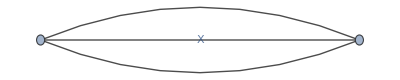
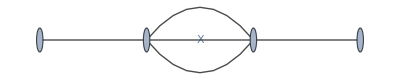
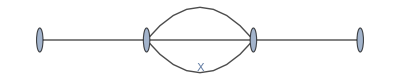
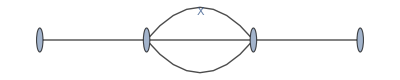
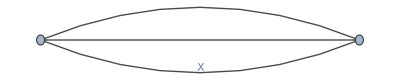
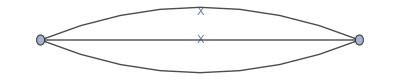
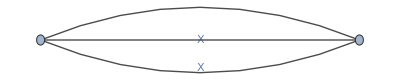
(loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}) | loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2}) | loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2}) | loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}) | loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}) | loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}) | loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3}) | loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})/.doem2 | -Graphics-
loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}) | loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}) | loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}) | loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}) | loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-)

```mathematica
gs2=AssociationMap[FCLoopIntegralToGraph@@#&,foundLIs];
plot2L=FCLoopGraphPlot/@KeySelect[gs2,Length[#[[2]]]==2&];
KeyValueMap[{#1,#1/.doem2, #2}&, plot2L]
```

```mathematica
(*doem ={loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2, k3}]->martinF[m], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}]->dmartinGbdw[m], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
   PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k3, D], m]], {k1, k2, k3}]->martinH[m],

loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->martinGWithMomInjection,loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k1,k2,k3}]->d2martinEbdz2[m],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->dmartinGbdv[m],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->dmartinGbdw[m],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->d2martinEbdzbdy[m]}*)
```

```mathematica
martinF= 1/eps^3 mF3[m]
```

(mF3(m))/eps^3

```mathematica
Keys[plot3L]//InputForm
```

Keys::invrl: The argument KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)] is not a valid Association or a list of rules.

Keys[KeySelect[FCLoopGraphPlot[gs], FCLoopGraphPlot[Length[#1[[2]]] == 3 & ]]]

```mathematica
appliedRules=foundSFADLIs /.rules;
unDone=KeySortBy[Select[appliedRules, Head[#]===loopIntegral&],#[[2]]&];
Length[unDone]->Length[Union@unDone]
AssociationMap[InputForm,Values[ unDone][[1;;3]]]
allRepRules =Join[rules, MapIndexed[#1 ->unknown3L[#2[[1]]]&,Values[unDone]]]
```

7→7

<|loopIntegral(1/((k1^2-m^2+ⅈ η).(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1+k2-p)^2-m^2+ⅈ η).((k1-k3-p)^2-m^2+ⅈ η)),{k1,k2,k3})→loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k2, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k3, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k1, D] - Momentum[k3, D] - Momentum[p, D], 0, -m^2, {1, 1}]], {k1, k2, k3}],loopIntegral(1/((k1^2-m^2+ⅈ η)^3.(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1+k2+k3)^2-m^2+ⅈ η)),{k1,k2,k3})→loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1, D], 0, -m^2, {3, 1}], StandardPropagatorDenominator[Momentum[k2, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k3, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] + Momentum[k3, D], 0, -m^2, {1, 1}]], {k1, k2, k3}],loopIntegral(1/((k1^2-m^2+ⅈ η)^2.(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1-k2)^2-m^2+ⅈ η).((k2-k3)^2-m^2+ⅈ η)),{k1,k2,k3})→loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1, D], 0, -m^2, {2, 1}], StandardPropagatorDenominator[Momentum[k2, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k3, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], 0, -m^2, {1, 1}]], {k1, k2, k3}]|>

{loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})),{k1_}):>IMaster(0,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^2,{k1_})→IMaster(1,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^4,{k1_})→IMaster(2,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) (k1_·k2_),{k1_,k2_})→genSunrise3TopKL({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k3_,0,Xk3_,{b3_,1}),StandardPropagatorDenominator(k1_-k2_-k3_+mom_.,0,Xk4_,{b4_,1})),{k1_,k2_,k3_})→genSunrise4({b1,Xk1},{b2,Xk2},{b3,Xk3},{b4,Xk4,mom}),loopIntegral(1/((k1^2-m^2+ⅈ η).(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1+k2-p)^2-m^2+ⅈ η).((k1-k3-p)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(1),loopIntegral(1/((k1^2-m^2+ⅈ η)^3.(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1+k2+k3)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(2),loopIntegral(1/((k1^2-m^2+ⅈ η)^2.(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1-k2)^2-m^2+ⅈ η).((k2-k3)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(3),loopIntegral(1/((k1^2-m^2+ⅈ η).(k2^2-m^2+ⅈ η)^2.(k3^2-m^2+ⅈ η).((k1+k2)^2-m^2+ⅈ η).((k2-k3)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(4),loopIntegral(1/((k1^2-m^2+ⅈ η)^2.(k2^2-m^2+ⅈ η)^2.(k3^2-m^2+ⅈ η).((k1+k2-k3)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(5),loopIntegral(1/((k1^2-m^2+ⅈ η)^2.(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1-k2)^2-m^2+ⅈ η).((k1+k3)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(6),loopIntegral(1/((k1^2-m^2+ⅈ η).(k2^2-m^2+ⅈ η).(k3^2-m^2+ⅈ η).((k1+k2)^2-m^2+ⅈ η).((k1-k3)^2-m^2+ⅈ η).((k2+k3)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(7)}

```mathematica
mapped = #/.allRepRules&/@foundSFADLIs
```

<|loopIntegral(1/(k1^2-m^2),{k1})→IMaster(0,1,-m^2),loopIntegral(1/(k2^2-m^2),{k2})→IMaster(0,1,-m^2),loopIntegral(1/(k3^2-m^2),{k3})→IMaster(0,1,-m^2),loopIntegral(1/((k1^2-m^2)^2),{k1})→IMaster(0,2,-m^2),loopIntegral(1/((k2^2-m^2)^2),{k2})→IMaster(0,2,-m^2),loopIntegral(1/((k3^2-m^2)^2),{k3})→IMaster(0,2,-m^2),loopIntegral(1/((k1^2-m^2)^3),{k1})→IMaster(0,3,-m^2),loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→genSunrise3({1,-m^2},{1,-m^2},{1,-m^2,-p}),loopIntegral(1/((k2^2-m^2)^3),{k2})→IMaster(0,3,-m^2),loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2})→genSunrise3({1,-m^2},{1,-m^2},{1,-m^2,-p}),loopIntegral(1/((k1^2-m^2)^4),{k1})→IMaster(0,4,-m^2),loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2})→genSunrise3({2,-m^2},{1,-m^2},{1,-m^2,0}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→genSunrise3({2,-m^2},{1,-m^2},{1,-m^2,-p}),loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→genSunrise3({1,-m^2},{1,-m^2},{2,-m^2,-p}),loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→genSunrise3({1,-m^2},{2,-m^2},{1,-m^2,-p}),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→genSunrise3({2,-m^2},{1,-m^2},{1,-m^2,0}),loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→genSunrise3({1,-m^2},{2,-m^2},{1,-m^2,0}),loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→genSunrise3({2,-m^2},{1,-m^2},{2,-m^2,0}),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→genSunrise3({3,-m^2},{1,-m^2},{1,-m^2,0}),loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→genSunrise3({2,-m^2},{2,-m^2},{1,-m^2,0}),loopIntegral(1/((k2^2-m^2).((k1-k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2),{k1,k2,k3})→genSunrise4({2,-m^2},{1,-m^2},{1,-m^2},{1,-m^2,0}),loopIntegral(1/((k3^2-m^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(1),loopIntegral(1/((k1^2-m^2)^3.((k1+k2+k3)^2-m^2).(k2^2-m^2).(k3^2-m^2)),{k1,k2,k3})→unknown3L(2),loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(3),loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→unknown3L(4),loopIntegral(1/(((k1+k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→unknown3L(5),loopIntegral(1/((k3^2-m^2).((k1+k3)^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(6),loopIntegral(1/((k3^2-m^2).((k2+k3)^2-m^2).(k1^2-m^2).(k2^2-m^2).((k1+k2)^2-m^2).((k1-k3)^2-m^2)),{k1,k2,k3})→unknown3L(7),loopIntegral(k1^2/((k1^2-m^2)^2),{k1})→IMaster(1,2,-m^2),loopIntegral(k1^2/((k1^2-m^2)^3),{k1})→IMaster(1,3,-m^2),loopIntegral(k1^2/((k1^2-m^2)^4),{k1})→IMaster(1,4,-m^2),loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→genSunrise3TopK2({2,-m^2},{1,-m^2},{1,-m^2,-p}),loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→genSunrise3TopK2({1,-m^2},{1,-m^2},{2,-m^2,-p}),loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→genSunrise3TopK2({2,-m^2},{1,-m^2},{2,-m^2,0}),loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→genSunrise3TopK2({3,-m^2},{1,-m^2},{1,-m^2,0}),loopIntegral(k1^4/((k1^2-m^2)^4),{k1})→IMaster(2,4,-m^2),loopIntegral(k2^2/((k2^2-m^2)^2),{k2})→IMaster(1,2,-m^2),loopIntegral(k2^2/((k2^2-m^2)^3),{k2})→IMaster(1,3,-m^2),loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→genSunrise3TopK2({1,-m^2},{1,-m^2},{2,-m^2,-p}),loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→genSunrise3TopK2({2,-m^2},{1,-m^2},{1,-m^2,-p}),loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→genSunrise3TopK2({1,-m^2},{2,-m^2},{2,-m^2,0}),loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→genSunrise3TopK2({2,-m^2},{2,-m^2},{1,-m^2,0})|>

```mathematica
Union[Values[mapped]]/.{genSunrise4[__]->unk3L}
```

{genSunrise3({1,-m^2},{1,-m^2},{1,-m^2,-p}),genSunrise3({1,-m^2},{1,-m^2},{2,-m^2,-p}),genSunrise3({1,-m^2},{2,-m^2},{1,-m^2,0}),genSunrise3({1,-m^2},{2,-m^2},{1,-m^2,-p}),genSunrise3({2,-m^2},{1,-m^2},{1,-m^2,0}),genSunrise3({2,-m^2},{1,-m^2},{1,-m^2,-p}),genSunrise3({2,-m^2},{1,-m^2},{2,-m^2,0}),genSunrise3({2,-m^2},{2,-m^2},{1,-m^2,0}),genSunrise3({3,-m^2},{1,-m^2},{1,-m^2,0}),genSunrise3TopK2({1,-m^2},{1,-m^2},{2,-m^2,-p}),genSunrise3TopK2({1,-m^2},{2,-m^2},{2,-m^2,0}),genSunrise3TopK2({2,-m^2},{1,-m^2},{1,-m^2,-p}),genSunrise3TopK2({2,-m^2},{1,-m^2},{2,-m^2,0}),genSunrise3TopK2({2,-m^2},{2,-m^2},{1,-m^2,0}),genSunrise3TopK2({3,-m^2},{1,-m^2},{1,-m^2,0}),unk3L,IMaster(0,1,-m^2),IMaster(0,2,-m^2),IMaster(0,3,-m^2),IMaster(0,4,-m^2),IMaster(1,2,-m^2),IMaster(1,3,-m^2),IMaster(1,4,-m^2),IMaster(2,4,-m^2),unknown3L(1),unknown3L(2),unknown3L(3),unknown3L(4),unknown3L(5),unknown3L(6),unknown3L(7)}

```mathematica
replaceAMR ={A[x_]:> x (LnB[x]-1), Aϵ[x_]:> x (-1 - Zeta[2]/2+LnB[x]-(LnB[x]^2/2))}
replaceLnB= LnB[x_]-> Log[x/μb^2]
```

{A(x_):>x (LnB(x)-1),Aϵ(x_):>x (-1/2 (LnB(x))^2+LnB(x)-2/2-1)}

LnB(x_)→log(x/μb^2)

```mathematica
(*The loop integrals are functions of a common external momentum invariant
s=−p2 (2.6) using a Euclidean or signature (−+++) metric.*)
```

```mathematica
(*S[x_,y_,z_,s_]:= (-(x+y+z))/ϵMR^2+(A[x]+B[y]+B[z] - (x+y+z)/2+s/4)/ϵMR+Sfin[x,y,z]+Aϵ[x]+Aϵ[y]+Aϵ[z]
ourS[x_,y_,z_,s_]:=(f4π^2)^2 S[x,y,z,s]/.ϵMR->ϵ/2*)
S[x_,y_,z_,s_]:= (-(x+y+z))/(2 ϵMR^2)+(A[x]+A[y]+A[z] - (x+y+z)/2+s/4)/ϵMR(*+Sfin[x,y,z]+Aϵ[x]+Aϵ[y]+Aϵ[z]*)/.replaceAMR/.replaceLnB
ourS[x_,y_,z_,s_]:=1/((f4π^2)^2)S[x,y,z,s]/.ϵMR->ϵ/2
```

```mathematica
D[ourS[x,y,z,s], {x,0},{y,0},{z,0}]
```

((2 (s/4+x (log(x/μb^2)-1)+1/2 (-x-y-z)+y (log(y/μb^2)-1)+z (log(z/μb^2)-1)))/ϵ-(2 (x+y+z))/ϵ^2)/f4π^4

```mathematica
mapGSR3TopK2={genSunrise3TopK2[{1,-m1_^2},{b_/;b>=1,-m2_^2},{c_/;c>=1,-m3_^2,mom_}]:>(*DANGEROUS CASE, WHERE SUBTRACTING 1 FROM POWER REMOVES PROP*)IMaster[0,b,-m2^2]IMaster[0,c,-m3^2]+m1^2 genSunrise3[{1,-m1^2}, {b, -m2^2}, {c, -m3^2,mom}],genSunrise3TopK2[{a_/;a>1,mxSub_}, {b_, mySub_}, {c_, mzSub_,mom_}]:>genSunrise3[{a-1,mxSub}, {b, mySub}, {c, mzSub,mom}]+(-mxSub)genSunrise3[{a,mxSub}, {b, mySub}, {c, mzSub,mom}]}
genSunrise3Eval[{1,mxSub_}, {1, mySub_}, {1, mzSub_,mom_}]:=(ourS[x,y,z,s]/.{x->-mxSub, y->-mySub, z->-mzSub,s->Pair[mom,mom]}) + O[ϵ]^1/ϵ
mapGSR3 =genSunrise3[{1,mxSub_}, {1, mySub_}, {1, mzSub_,mom_}]:>genSunrise3Eval[{1,mxSub}, {1, mySub}, {1, mzSub,mom}]
mapGSR3Higher= genSunrise3[{a_/;a>=1,-m1_^2}, {b_/;b>=1, -m2_^2}, {c_/;c>=1, -m3_^2,mom_}]:>genSunrise3Evaluator[{a,-m1^2}, {b, -m2^2}, {c, -m3^2,mom}];

applyAllMaps = {mapGSR3,mapGSR3Higher,repImaster};

(*
1/((a-1)!(b-1)!(c-1)!)(1/(2 m1))^(a-1)(1/(2 m2))^(b-1)(1/(2 m3))^(c-1)(D[,{m1temp, a-1}, {m2temp, b-1}, {m3temp, c-1}]/.{m1temp->m1, m2temp->m2, m3temp->m3})+ O[ϵ]^1/ϵ*)

genSunrise3Evaluator[{a_/;a>=1,-m1_^2}, {b_/;b>=1, -m2_^2}, {c_/;c>=1, -m3_^2,mom_}]:= Module[{expr},
expr =genSunrise3Eval[{1,-m1temp^2}, {1, -m2temp^2}, {1, -m3temp^2,mom}];

Do[expr = 1/(2m1temp)D[expr,m1temp],a-1];
expr = 1/((a-1)!)expr;
Do[expr = 1/(2m2temp)D[expr,m2temp],b-1];
expr = 1/((b-1)!)expr;
Do[expr = 1/(2m3temp)D[expr,m3temp],c-1];
expr = 1/((c-1)!)expr;
(FullSimplify[expr] /.{m1temp->m1, m2temp->m2, m3temp->m3})+ O[ϵ]^1/ϵ
];


(*genSunrise3[{a_/;a>0,mxSub_}, {b_/;b>0, mySub_}, {c_/;c>0, mzSub_,mom_}]:>((D[ourS[x,y,z,s], {x,a-1},{y,b-1},{z,c-1}])/.{x->-mxSub, y->-mySub, z->-mzSub,s->Pair[mom,mom]}) + O[ϵ]*)
```

{genSunrise3TopK2({1,-m1_^2},{b_/;b≥1,-m2_^2},{c_/;c≥1,-m3_^2,mom_}):>m1^2 genSunrise3({1,-m1^2},{b,-m2^2},{c,-m3^2,mom})+IMaster(0,b,-m2^2) IMaster(0,c,-m3^2),genSunrise3TopK2({a_/;a>1,mxSub_},{b_,mySub_},{c_,mzSub_,mom_}):>genSunrise3({a-1,mxSub},{b,mySub},{c,mzSub,mom})-mxSub genSunrise3({a,mxSub},{b,mySub},{c,mzSub,mom})}

genSunrise3({1,mxSub_},{1,mySub_},{1,mzSub_,mom_}):>genSunrise3Eval({1,mxSub},{1,mySub},{1,mzSub,mom})

```mathematica
(*genSunrise3[{1,m}, {1,m}, {1,m,Momentum[p,D]}]/.mapGSR3/.f4π->4π*)
```

```mathematica
ImasterStd[a_,b_,X_]:=(μ^2)^((4-dim)/2)I (-1)^(a-b) 1/(4 π)^(dim/2) 1/(-X)^(b-a-dim/2) (Gamma[a+dim/2] Gamma[b-a-dim/2])/(Gamma[b] Gamma[dim/2])/.μ^2->μb^2/(4π Exp[-EulerGamma ])
```

```mathematica
repImaster=IMaster[a_,b_,X_]:> Series[ImasterStd[a,b,X]/.dim->4-ϵ, {ϵ,0,1},Assumptions->{m>0, μb>0}]
```

IMaster(a_,b_,X_):>Series[ImasterStd(a,b,X)/.dim→4-ϵ,{ϵ,0,1},Assumptions→{m>0,μb>0}]

```mathematica
(#/.{genSunrise4[__]->unk3L}/.applyAllMaps)&/@mapped[[33;;34]]
```

<|loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→genSunrise3TopK2({1,-m^2},{1,-m^2},{2,-m^2,-p}),loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→genSunrise3TopK2({2,-m^2},{1,-m^2},{2,-m^2,0})|>

```mathematica
evaluated=(#/.{genSunrise4[__]->unk3L}/.mapGSR3TopK2/.applyAllMaps)&/@mapped
```

<|loopIntegral(1/(k1^2-m^2),{k1})→(ⅈ m^2)/(8 π^2 ϵ)-(ⅈ (2 log(m) m^2-2 log(μb) m^2-m^2))/(16 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(1/(k2^2-m^2),{k2})→(ⅈ m^2)/(8 π^2 ϵ)-(ⅈ (2 log(m) m^2-2 log(μb) m^2-m^2))/(16 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(1/(k3^2-m^2),{k3})→(ⅈ m^2)/(8 π^2 ϵ)-(ⅈ (2 log(m) m^2-2 log(μb) m^2-m^2))/(16 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(1/((k1^2-m^2)^2),{k1})→ⅈ/(8 π^2 ϵ)-(ⅈ (log(m)-log(μb)))/(8 π^2)+(ⅈ (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(1/((k2^2-m^2)^2),{k2})→ⅈ/(8 π^2 ϵ)-(ⅈ (log(m)-log(μb)))/(8 π^2)+(ⅈ (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(1/((k3^2-m^2)^2),{k3})→ⅈ/(8 π^2 ϵ)-(ⅈ (log(m)-log(μb)))/(8 π^2)+(ⅈ (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(1/((k1^2-m^2)^3),{k1})→-ⅈ/(32 m^2 π^2)+(ⅈ (log(m)-log(μb)) ϵ)/(32 m^2 π^2)+O(ϵ^2),loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→-(6 m^2)/(f4π^4 ϵ^2)+(12 log(m^2/μb^2) m^2-18 m^2+p^2)/(2 f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/((k2^2-m^2)^3),{k2})→-ⅈ/(32 m^2 π^2)+(ⅈ (log(m)-log(μb)) ϵ)/(32 m^2 π^2)+O(ϵ^2),loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2})→-(6 m^2)/(f4π^4 ϵ^2)+(12 log(m^2/μb^2) m^2-18 m^2+p^2)/(2 f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/((k1^2-m^2)^4),{k1})→ⅈ/(96 m^4 π^2)-(ⅈ (2 log(m)-2 log(μb)-1) ϵ)/(192 m^4 π^2)+O(ϵ^2),loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→O(ϵ^0),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→1/(f4π^4 m^2 ϵ)+O(ϵ^0),loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→O(ϵ^0),loopIntegral(1/((k2^2-m^2).((k1-k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2),{k1,k2,k3})→unk3L,loopIntegral(1/((k3^2-m^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(1),loopIntegral(1/((k1^2-m^2)^3.((k1+k2+k3)^2-m^2).(k2^2-m^2).(k3^2-m^2)),{k1,k2,k3})→unknown3L(2),loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(3),loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→unknown3L(4),loopIntegral(1/(((k1+k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→unknown3L(5),loopIntegral(1/((k3^2-m^2).((k1+k3)^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(6),loopIntegral(1/((k3^2-m^2).((k2+k3)^2-m^2).(k1^2-m^2).(k2^2-m^2).((k1+k2)^2-m^2).((k1-k3)^2-m^2)),{k1,k2,k3})→unknown3L(7),loopIntegral(k1^2/((k1^2-m^2)^2),{k1})→(ⅈ m^2)/(4 π^2 ϵ)-(ⅈ (4 log(m) m^2-4 log(μb) m^2-m^2))/(16 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2) ϵ)/(192 π^2)+O(ϵ^2),loopIntegral(k1^2/((k1^2-m^2)^3),{k1})→ⅈ/(8 π^2 ϵ)-(ⅈ (4 log(m)-4 log(μb)+1))/(32 π^2)+(ⅈ (24 log^2(m)-48 log(μb) log(m)+12 log(m)+24 log^2(μb)-12 log(μb)+π^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(k1^2/((k1^2-m^2)^4),{k1})→-ⅈ/(48 m^2 π^2)+(ⅈ (4 log(m)-4 log(μb)+1) ϵ)/(192 m^2 π^2)+O(ϵ^2),loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→-(8 m^2)/(f4π^4 ϵ^2)+(((2 log(m^2/μb^2)-1) m^2)/f4π^4+(12 log(m^2/μb^2) m^2-18 m^2+p^2)/(2 f4π^4))/ϵ+O(ϵ^0),loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→(-(2 m^2)/f4π^4-m^2/(64 π^4))/ϵ^2+(((2 log(m^2/μb^2)-1) m^2)/f4π^4+((log(m)-log(μb)) m^2)/(64 π^4)+(2 log(m) m^2-2 log(μb) m^2-m^2)/(128 π^4))/ϵ+O(ϵ^0),loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→-2/(f4π^4 ϵ^2)+((2 log(m^2/μb^2)-1)/f4π^4+1/f4π^4)/ϵ+O(ϵ^0),loopIntegral(k1^4/((k1^2-m^2)^4),{k1})→ⅈ/(8 π^2 ϵ)-(ⅈ (12 log(m)-12 log(μb)+5))/(96 π^2)+(ⅈ (24 log^2(m)-48 log(μb) log(m)+20 log(m)+24 log^2(μb)-20 log(μb)+π^2+2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(k2^2/((k2^2-m^2)^2),{k2})→(ⅈ m^2)/(4 π^2 ϵ)-(ⅈ (4 log(m) m^2-4 log(μb) m^2-m^2))/(16 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2) ϵ)/(192 π^2)+O(ϵ^2),loopIntegral(k2^2/((k2^2-m^2)^3),{k2})→ⅈ/(8 π^2 ϵ)-(ⅈ (4 log(m)-4 log(μb)+1))/(32 π^2)+(ⅈ (24 log^2(m)-48 log(μb) log(m)+12 log(m)+24 log^2(μb)-12 log(μb)+π^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→(-(2 m^2)/f4π^4-m^2/(64 π^4))/ϵ^2+(((2 log(m^2/μb^2)-1) m^2)/f4π^4+((log(m)-log(μb)) m^2)/(64 π^4)+(2 log(m) m^2-2 log(μb) m^2-m^2)/(128 π^4))/ϵ+O(ϵ^0),loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→-(8 m^2)/(f4π^4 ϵ^2)+(((2 log(m^2/μb^2)-1) m^2)/f4π^4+(12 log(m^2/μb^2) m^2-18 m^2+p^2)/(2 f4π^4))/ϵ+O(ϵ^0),loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→-1/(64 π^4 ϵ^2)+(log(m)-log(μb))/(32 π^4 ϵ)+O(ϵ^0),loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0)|>

```mathematica
prepareIncludingMinusSignVariationNeg[loopIntegral[integrand_, loopMomenta_]]:= Module[{fcped, fixed, results, totalCorrectionFactor, propagators, indices},
fcped = FCFeynmanPrepare[integrand, loopMomenta, Names->x];
fixed = FCE[fcped[[3]] /.FeynAmpDenominator[a_]->FeynAmpDenominator[a]^-1//FeynAmpDenominatorExplicit] /.SPD -> Times;
results={(-1)^(#[[3]]),- #[[2]], #[[3]]} &/@ fixed;
totalCorrectionFactor =Times@@(First/@results);
propagators = #[[2]]&/@results;
indices = #[[3]]&/@results;
<|pmC->totalCorrectionFactor,loopMs->loopMomenta, props->propagators, idxs->indices,uf-> UF[loopMomenta, propagators, {}(*No map*)]|>
];
```

```mathematica
prepped =prepareIncludingMinusSignVariationNeg/@foundSFADLIs;
```

```mathematica
Merge[{prepped,evaluated}, Identity][[1]]/.m->3/.μb->1//N
```

{<|pmC→-1.,loopMs→{k1},props→{9.-1. k1^2},idxs→{1.},uf→UF({k1},{9.-1. k1^2},{})|>,(0.+0.113986 ⅈ)/(ϵ+0.)-(0.+0.0682336 ⅈ)+(0.+0.0581085 ⅈ) (ϵ+0.)+O((ϵ+0.)^2)}

```mathematica
prepped//InputForm
```

<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m]], {k1}] -> <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {1}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m]], {k2}] -> <|pmC -> -1, loopMs -> {k2}, props -> {-k2^2 + m^2}, idxs -> {1}, uf -> UF[{k2}, {-k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m]], {k3}] -> <|pmC -> -1, loopMs -> {k3}, props -> {-k3^2 + m^2}, idxs -> {1}, uf -> UF[{k3}, {-k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1}] -> 
  <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {2}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k2}] -> 
  <|pmC -> 1, loopMs -> {k2}, props -> {-k2^2 + m^2}, idxs -> {2}, uf -> UF[{k2}, {-k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m]], {k3}] -> 
  <|pmC -> 1, loopMs -> {k3}, props -> {-k3^2 + m^2}, idxs -> {2}, uf -> UF[{k3}, {-k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1}] -> 
  <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {3}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]], 
   {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k2}] -> 
  <|pmC -> -1, loopMs -> {k2}, props -> {-k2^2 + m^2}, idxs -> {3}, uf -> UF[{k2}, {-k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m]], 
   {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], 
   {k1}] -> <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {4}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]], {k1, k2}] -> <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, idxs -> {2, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {2, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 1, 2}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]], {k1, k2}] -> <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 2, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, idxs -> {2, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], 
    PropagatorDenominator[Momentum[k3, D], m]], {k2, k3}] -> <|pmC -> 1, loopMs -> {k2, k3}, props -> {-k2^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, idxs -> {1, 2, 1}, 
   uf -> UF[{k2, k3}, {-k2^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, 
   idxs -> {2, 2, 1}, uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, 
   idxs -> {3, 1, 1}, uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, 
   idxs -> {2, 1, 2}, uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2, k3}] -> 
  <|pmC -> -1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + 2*k1*k3 - 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {2, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + 2*k1*k3 - 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
    PropagatorDenominator[Momentum[k1, D] - Momentum[k3, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> -1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2 + 2*k1*k3 - k3^2 + m^2 + 2*k1*p - 2*k3*p - p^2}, 
   idxs -> {1, 1, 1, 1, 1}, uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2 + 2*k1*k3 - k3^2 + m^2 + 2*k1*p - 2*k3*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k3, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 - 2*k1*k3 - 2*k2*k3 - k3^2 + m^2}, idxs -> {3, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 - 2*k1*k3 - 2*k2*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {2, 1, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {1, 2, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + 2*k1*k3 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {2, 2, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + 2*k1*k3 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k3 - k3^2 + m^2}, idxs -> {2, 1, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k3, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k1^2 + 2*k1*k3 - k3^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, idxs -> {1, 1, 1, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k1^2 + 2*k1*k3 - k3^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1}] -> 
  <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {2, -1}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], 
   {k1}] -> <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {3, -1}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*
    Pair[Momentum[k1, D], Momentum[k1, D]], {k1}] -> <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {4, -1}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, idxs -> {2, 1, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
     PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, idxs -> {1, 1, 2, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, idxs -> {2, 2, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, idxs -> {3, 1, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*
    Pair[Momentum[k1, D], Momentum[k1, D]]^2, {k1}] -> <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {4, -2}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k2}] -> 
  <|pmC -> -1, loopMs -> {k2}, props -> {-k2^2 + m^2, -k2^2}, idxs -> {2, -1}, uf -> UF[{k2}, {-k2^2 + m^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], 
   {k2}] -> <|pmC -> 1, loopMs -> {k2}, props -> {-k2^2 + m^2, -k2^2}, idxs -> {3, -1}, uf -> UF[{k2}, {-k2^2 + m^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
     PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, idxs -> {1, 1, 2, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, idxs -> {1, 2, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, idxs -> {2, 2, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, idxs -> {2, 1, 2, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, {}]|>|>

```mathematica
testThisOne[thisOne_Association]:=Module[{nLoops, epsOrder,fiestaResult,ourResult},

nLoops=Length[thisOne[loopMs]];
epsOrder=If[nLoops>1, 1, 2];

fiestaResult =SDEvaluate[thisOne[uf]/.evalPoint, thisOne[idxs], epsOrder, d0->modeldim, NumberOfLinks->6,NumberOfSubkernels->6, UsingC->True,IntegratorOptions->{{"maxeval","50000000"}},ComplexMode->True,SectorSplitting->True,Precision->9];
ourResult =Λ^nLoops thisOne[pmC] (fiestaResult /.ep->ϵ/2)/.loopCoeffRule//Expand;
Series[ourResult,{ϵ,0,epsOrder}]
];
modeldim=4;
evalPoint = {m->2, p->8}
loopCoeffRule =Λ -> I π^(d0/2)/(2π)^d0/.d0->modeldim;

evaled=testThisOne/@prepped;
(*ourResult =Λ^nLoops thisOne[pmC] (fiestaResult /.ep->ϵ/2)/.loopCoeffRule//Expand*)
```

{m→2,p→8}

```mathematica
dataSoFound=<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623484114321816-2.0353111849775345*^-8*I)+(3.675806487353564*^-6+9.2923228123958*^-7*I)*pm146,(0.0011737001955536557+6.76957316560749*^-8*I)+(0.000013167408617330965+9.700018332171644*^-6*I)*pm147,(-0.002241211528084359+0.0005310085159210851*I)+(0.000036887074264410804+0.000031776956146547004*I)*pm148,(0.0014776956683505136-0.00009658650086956667*I)+(0.00006235177078375712+0.000061033593919634356*I)*pm149},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623484114321816-2.0353111849775345*^-8*I)+(3.675806487353564*^-6+9.2923228123958*^-7*I)*pm169,(0.0011737001955536557+6.76957316560749*^-8*I)+(0.000013167408617330965+9.700018332171644*^-6*I)*pm170,(-0.002241211528084359+0.0005310085159210851*I)+(0.000036887074264410804+0.000031776956146547004*I)*pm171,(0.0014776956683505136-0.00009658650086956667*I)+(0.00006235177078375712+0.000061033593919634356*I)*pm172},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.00006596431437800497*I,0.-0.000012740610073096841*I,0.+6.54845934026154*^-6*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm192,0.00007108329542768749-1.3069237034104078*^-8*pm193,-0.000027509143546297665-6.470047092729802*^-8*pm194,-0.000030013624617004063-9.98634050720112*^-8*pm195},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.00008019570088584598-1.6961327556411278*^-9*I)-(3.063171805451349*^-7+7.743598333513848*^-8*I)*pm206,(0.00007107470440460004-8.467430285455459*^-9*I)-(5.981031840207095*^-7+4.5519004403831706*^-7*I)*pm207,(-0.00017293760220838577-0.00012257415817445037*I)-(1.2987213439948878*^-6+1.5463029502161347*^-6*I)*pm208,(0.0003523551419212216+0.0000785928425591858*I)-(2.2763576112608247*^-6+2.354983806913616*^-6*I)*pm209},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.00008019570088584598-1.6961327556411278*^-9*I)-(3.063171805451349*^-7+7.743598333513848*^-8*I)*pm220,(0.00007107470440460004-8.467430285455459*^-9*I)-(5.981031840207095*^-7+4.5519004403831706*^-7*I)*pm221,(-0.00017293760220838577-0.00012257415817445037*I)-(1.2987213439948878*^-6+1.5463029502161347*^-6*I)*pm222,(0.0003523551419212216+0.0000785928425591858*I)-(2.2763576112608247*^-6+2.354983806913616*^-6*I)*pm223},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.00008019570088584598-1.6961327556411278*^-9*I)-(3.063171805451349*^-7+7.743598333513848*^-8*I)*pm234,(0.00007107470440460004-8.467430285455459*^-9*I)-(5.981031840207095*^-7+4.5519004403831706*^-7*I)*pm235,(-0.00017293760220838577-0.00012257415817445037*I)-(1.2987213439948878*^-6+1.5463029502161347*^-6*I)*pm236,(0.0003523551419212216+0.0000785928425591858*I)-(2.2763576112608247*^-6+2.354983806913616*^-6*I)*pm237},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm248,0.00007108329542768749-1.3069237034104078*^-8*pm249,-0.000027509143546297665-6.470047092729802*^-8*pm250,-0.000030013624617004063-9.98634050720112*^-8*pm251},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k2,k3}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm262,0.00007108329542768749-1.3069237034104078*^-8*pm263,-0.000027509143546297665-6.470047092729802*^-8*pm264,-0.000030013624617004063-9.98634050720112*^-8*pm265},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83286433754077*^-6+2.5297625959160416*^-9*pm269,-0.000017604922796632398+5.7459825521277336*^-9*pm270},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{0.000010025238233761133+2.1301913178469998*^-10*pm277,-0.000016718337571159412+2.0511913762777495*^-9*pm278,0.000021043723744815433+1.993826190280382*^-9*pm279},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83286433754077*^-6+2.5297625959160416*^-9*pm283,-0.000017604922796632398+5.7459825521277336*^-9*pm284},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-8.126152035160348*^-6*I)+(0.+1.2209504762423328*^-10*I)*pm300,(0.+7.417639760945818*^-6*I)+(0.+9.475668880970153*^-9*I)*pm301,(0.-8.961895461547776*^-6*I)+(0.+3.123454619258642*^-8*I)*pm302,(0.+0.000011844274925835922*I)+(0.+8.291203592077704*^-8*I)*pm303,(0.-0.000011008750595267285*I)+(0.+1.7556316174260927*^-7*I)*pm304},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(8.853561915279932*^-12-8.125724374395855*^-6*I)-(4.160396010641974*^-9-1.3148183450415376*^-8*I)*pm320,(-2.8428537427422428*^-9+0.00001554491058627005*I)-(5.40526857551781*^-8-7.522134913807466*^-8*I)*pm321,(-0.000013441675527519762-0.000048737474397094305*I)-(2.521132169812517*^-7-3.0012158993309103*^-7*I)*pm322,(3.76568888823489*^-6+0.000052804126563971805*I)-(7.518606971017091*^-7-8.405427281239189*^-7*I)*pm323,(6.9835831940160455*^-6-0.00017341043825166224*I)-(1.8142741309735237*^-6-2.0128187156637315*^-6*I)*pm324},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.+8.464832220957154*^-7*I)-(0.+6.565511408835685*^-11*I)*pm335,(0.-4.905088702863148*^-7*I)-(0.+3.072564871545046*^-10*I)*pm336,(0.+1.2498025442618361*^-7*I)-(0.+1.5023918621445514*^-9*I)*pm337,(0.+2.3166653551772027*^-6*I)-(0.+4.269540844767136*^-9*I)*pm338},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-3.3859567674023095*^-7*I)-(0.+6.539608950272167*^-12*I)*pm354,(0.+1.9619085164354252*^-7*I)-(0.+1.4376575550635608*^-10*I)*pm355,(0.+1.1788950515198913*^-7*I)-(0.+4.813601163348749*^-10*I)*pm356,(0.-6.832233468713513*^-8*I)-(0.+1.376467059838*^-9*I)*pm357,(0.-1.0623006883420037*^-6*I)-(0.+2.1181435834425103*^-9*I)*pm358},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771913534804619*^-7*I)-(0.+1.8497402762419408*^-11*I)*pm374,(0.+7.309866073972608*^-7*I)-(0.+2.723618123386884*^-10*I)*pm375,(0.+3.7822552210643094*^-7*I)-(0.+1.1247253821355787*^-9*I)*pm376,(0.-3.1345310852194597*^-6*I)-(0.+1.7268739956112624*^-9*I)*pm377,(0.+7.975291446806417*^-6*I)-(0.+3.4449463611972084*^-9*I)*pm378},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771793367712537*^-7*I)-(0.+1.4389577569051803*^-11*I)*pm394,(0.+1.0695784414315802*^-6*I)-(0.+1.162268710312351*^-10*I)*pm395,(0.-1.3469478745060848*^-6*I)-(0.+2.221295299703956*^-9*I)*pm396,(0.+2.023961443922739*^-6*I)-(0.+2.5051313932949393*^-9*I)*pm397,(0.-3.941281097172294*^-6*I)-(0.+6.036420679738411*^-9*I)*pm398},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771913534804619*^-7*I)-(0.+1.8497402762419408*^-11*I)*pm414,(0.+7.309866073972608*^-7*I)-(0.+2.723618123386884*^-10*I)*pm415,(0.+3.7822552210643094*^-7*I)-(0.+1.1247253821355787*^-9*I)*pm416,(0.-3.1345310852194597*^-6*I)-(0.+1.7268739956112624*^-9*I)*pm417,(0.+7.975291446806417*^-6*I)-(0.+3.4449463611972084*^-9*I)*pm418},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-1.2211182906529958*^-6*I)-(0.+3.484987879924163*^-10*I)*pm425,(0.+5.087742503032666*^-6*I)-(0.+1.4739448679456742*^-9*I)*pm426,(0.-0.000013256927994548486*I)-(0.+3.4212059960867256*^-9*I)*pm427},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.-0.0005277144960263179*I,0.+0.0004977128755999391*I,0.-0.00032672401390972474*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0012832019815993665-2.279561359652657*^-8*I)+(5.001099080731084*^-6+1.2904285156107482*^-6*I)*pm475,(0.0014578389098051938+1.444357936785267*^-7*I)+(0.000019559782486291962+0.000013160962382504888*I)*pm476,(-0.002932917219021027+0.00003954525238818947*I)+(0.00006020783921059059+0.00005018145447513938*I)*pm477,(0.0028881880058459868+0.00021737207678721124*I)+(0.00010908279485763983+0.00010683187442553443*I)*pm478},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623473126512684+7.344684719932997*^-8*I)+(0.000010189579125407601+6.382513072193426*^-6*I)*pm489,(0.0008521927735076428+9.209949533220049*^-8*I)+(0.0000349170927427886+0.000019979940347104087*I)*pm490,(-0.0012875825567111373-0.0004928110388680198*I)+(0.00007157114849883628+0.00006329107912657967*I)*pm491,(0.0018275187299498685+0.0003139119036491674*I)+(0.00013141943463373885+0.00012350981381261417*I)*pm492},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020212129531044-4.518957063733861*^-9*pm503,0.00007108449983593374-2.1101566118530922*^-8*pm504,3.820023687792753*^-6-7.916628256297097*^-8*pm505,-0.00010042715625428233-2.0205887237854944*^-7*pm506},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm517,0.00011118466638069696-1.1583556914683979*^-8*pm518,-0.00009438170106451658-4.232764737339307*^-8*pm519,0.00005415933973602064-2.070959006327062*^-7*pm520},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]]^2,{k1}]->SeriesData[ϵ,0,{0.+0.012665147980622517*I,0.-0.014055956429437844*I,0.+0.009832224141176234*I,0.-0.005860944798531168*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623473126512684+7.344684719932997*^-8*I)+(0.000010189579125407601+6.382513072193426*^-6*I)*pm573,(0.0008521927735076428+9.209949533220049*^-8*I)+(0.0000349170927427886+0.000019979940347104087*I)*pm574,(-0.0012875825567111373-0.0004928110388680198*I)+(0.00007157114849883628+0.00006329107912657967*I)*pm575,(0.0018275187299498685+0.0003139119036491674*I)+(0.00013141943463373885+0.00012350981381261417*I)*pm576},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0012832019815993665-2.279561359652657*^-8*I)+(5.001099080731084*^-6+1.2904285156107482*^-6*I)*pm587,(0.0014578389098051938+1.444357936785267*^-7*I)+(0.000019559782486291962+0.000013160962382504888*I)*pm588,(-0.002932917219021027+0.00003954525238818947*I)+(0.00006020783921059059+0.00005018145447513938*I)*pm589,(0.0028881880058459868+0.00021737207678721124*I)+(0.00010908279485763983+0.00010683187442553443*I)*pm590},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.0001604042424302149-9.037914127467722*^-9*pm601,0.00022237197833710216-1.5529439579945997*^-7*pm602,-0.00018876333215192754-6.928391921236774*^-7*pm603,0.00010831574468436423-6.700089909892811*^-7*pm604},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020212129531044-4.518957063733861*^-9*pm615,0.00007108449983593374-2.1101566118530922*^-8*pm616,3.820023687792753*^-6-7.916628256297097*^-8*pm617,-0.00010042715625428233-2.0205887237854944*^-7*pm618},-2,2,1]|>;

dataSoFound2=<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356870386959-2.791063925492304*^-11*I)+(1.329518488729077*^-7+2.9805194198830486*^-8*I)*pm1354,(0.0011738135273459743-3.512890802774796*^-11*I)+(4.3233283454826237*^-7+3.1121662057618296*^-7*I)*pm1355,(-0.002241346684953936+0.0005307822572011232*I)+(1.199622774651597*^-6+1.0210233158862218*^-6*I)*pm1356,(0.0014773895980347606-0.00009602692134537757*I)+(2.0181741126272513*^-6+1.9617594723735326*^-6*I)*pm1357},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356870386959-2.791063925492304*^-11*I)+(1.329518488729077*^-7+2.9805194198830486*^-8*I)*pm1377,(0.0011738135273459743-3.512890802774796*^-11*I)+(4.3233283454826237*^-7+3.1121662057618296*^-7*I)*pm1378,(-0.002241346684953936+0.0005307822572011232*I)+(1.199622774651597*^-6+1.0210233158862218*^-6*I)*pm1379,(0.0014773895980347606-0.00009602692134537757*I)+(2.0181741126272513*^-6+1.9617594723735326*^-6*I)*pm1380},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.00006596431437800497*I,0.-0.000012740610073096841*I,0.+6.54845934026154*^-6*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1400,0.00007108354253308848-1.191415362447936*^-9*pm1401,-0.00002751087360491654-2.1378507030448306*^-9*pm1402,-0.00003001557050185924-3.3190201339846737*^-9*pm1403},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0000802029738530555-2.2456836182121986*^-12*I)-(1.107924053642261*^-8+2.4837260817426913*^-9*I)*pm1414,(0.00007108344316158838-9.223343431942958*^-12*I)-(1.9964929395770094*^-8+1.4555157762483269*^-8*I)*pm1415,(-0.00017297817461340258-0.00012256803491705038*I)-(4.226833726497636*^-8+4.963177344312143*^-8*I)*pm1416,(0.0003523712920356724+0.00007856053042014068*I)-(7.399962623210223*^-8+7.560486895344554*^-8*I)*pm1417},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0000802029738530555-2.2456836182121986*^-12*I)-(1.107924053642261*^-8+2.4837260817426913*^-9*I)*pm1428,(0.00007108344316158838-9.223343431942958*^-12*I)-(1.9964929395770094*^-8+1.4555157762483269*^-8*I)*pm1429,(-0.00017297817461340258-0.00012256803491705038*I)-(4.226833726497636*^-8+4.963177344312143*^-8*I)*pm1430,(0.0003523712920356724+0.00007856053042014068*I)-(7.399962623210223*^-8+7.560486895344554*^-8*I)*pm1431},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0000802029738530555-2.2456836182121986*^-12*I)-(1.107924053642261*^-8+2.4837260817426913*^-9*I)*pm1442,(0.00007108344316158838-9.223343431942958*^-12*I)-(1.9964929395770094*^-8+1.4555157762483269*^-8*I)*pm1443,(-0.00017297817461340258-0.00012256803491705038*I)-(4.226833726497636*^-8+4.963177344312143*^-8*I)*pm1444,(0.0003523712920356724+0.00007856053042014068*I)-(7.399962623210223*^-8+7.560486895344554*^-8*I)*pm1445},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1456,0.00007108354253308848-1.191415362447936*^-9*pm1457,-0.00002751087360491654-2.1378507030448306*^-9*pm1458,-0.00003001557050185924-3.3190201339846737*^-9*pm1459},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k2,k3}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1470,0.00007108354253308848-1.191415362447936*^-9*pm1471,-0.00002751087360491654-2.1378507030448306*^-9*pm1472,-0.00003001557050185924-3.3190201339846737*^-9*pm1473},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83284857765395*^-6+7.78369982669621*^-11*pm1477,-0.000017605001215102317+1.7540393117964565*^-10*pm1478},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{0.000010025373215387185+9.776744037859537*^-11*pm1485,-0.000016718285118406327+1.7969479095015824*^-10*pm1486,0.000021043859027202685+1.7546408341941918*^-10*pm1487},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83284857765395*^-6+7.78369982669621*^-11*pm1491,-0.000017605001215102317+1.7540393117964565*^-10*pm1492},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-8.126261424798103*^-6*I)+(0.+5.602041528541628*^-11*I)*pm1508,(0.+7.4174557488644*^-6*I)+(0.+3.506898312520834*^-10*I)*pm1509,(0.-8.962227925190242*^-6*I)+(0.+1.0426496329919835*^-9*I)*pm1510,(0.+0.000011843647452744235*I)+(0.+2.728737160246918*^-9*I)*pm1511,(0.-0.000010997067370690232*I)+(0.+5.627433048412698*^-9*I)*pm1512},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(5.89153959483979*^-14-8.126260957538066*^-6*I)-(1.3358151826879335*^-10-4.511090920807501*^-10*I)*pm1528,(-1.4714628029456757*^-11+0.000015543716781570384*I)-(1.7314655873101547*^-9-2.4640785359284823*^-9*I)*pm1529,(-0.00001344481365151393-0.00004872129369498907*I)-(8.076189518263842*^-9-9.706385126743488*^-9*I)*pm1530,(3.750340155322515*^-6+0.00005281083433168307*I)-(2.405647592138924*^-8-2.706474962105127*^-8*I)*pm1531,(6.787556786797122*^-6-0.0001734013878890885*I)-(5.7991005640624535*^-8-6.464309931850253*^-8*I)*pm1532},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.+8.464879769744816*^-7*I)-(0.+1.441497213627094*^-11*I)*pm1543,(0.-4.904948926086261*^-7*I)-(0.+2.997676292815811*^-11*I)*pm1544,(0.+1.2492817931086136*^-7*I)-(0.+6.140711088393962*^-11*I)*pm1545,(0.+2.316798924252133*^-6*I)-(0.+1.446329799768896*^-10*I)*pm1546},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-3.385901447877079*^-7*I)-(0.+2.3911524493539422*^-12*I)*pm1562,(0.+1.9619555979630497*^-7*I)-(0.+6.163769355428939*^-12*I)*pm1563,(0.+1.1790750329756002*^-7*I)-(0.+1.58492572928078*^-11*I)*pm1564,(0.-6.852324532936336*^-8*I)-(0.+4.400954682778104*^-11*I)*pm1565,(0.-1.062370909272305*^-6*I)-(0.+6.604682528771204*^-11*I)*pm1566},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771802895754158*^-7*I)-(0.+6.761049576423042*^-12*I)*pm1582,(0.+7.309850695022699*^-7*I)-(0.+1.579135767954817*^-11*I)*pm1583,(0.+3.7821398941767397*^-7*I)-(0.+3.827012069058388*^-11*I)*pm1584,(0.-3.1345427519915312*^-6*I)-(0.+5.901113346681404*^-11*I)*pm1585,(0.+7.975296213874576*^-6*I)-(0.+1.0762166798335833*^-10*I)*pm1586},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771884524051027*^-7*I)-(0.+6.602587476975626*^-12*I)*pm1602,(0.+1.069580488233698*^-6*I)-(0.+1.4672980939217374*^-11*I)*pm1603,(0.-1.3470414275838287*^-6*I)-(0.+7.175539702573796*^-11*I)*pm1604,(0.+2.02397455539174*^-6*I)-(0.+8.35481261509608*^-11*I)*pm1605,(0.-3.9414206340974945*^-6*I)-(0.+1.9203790741470535*^-10*I)*pm1606},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771802895754158*^-7*I)-(0.+6.761049576423042*^-12*I)*pm1622,(0.+7.309850695022699*^-7*I)-(0.+1.579135767954817*^-11*I)*pm1623,(0.+3.7821398941767397*^-7*I)-(0.+3.827012069058388*^-11*I)*pm1624,(0.-3.1345427519915312*^-6*I)-(0.+5.901113346681404*^-11*I)*pm1625,(0.+7.975296213874576*^-6*I)-(0.+1.0762166798335833*^-10*I)*pm1626},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-1.2210293771626828*^-6*I)-(0.+1.062661059852008*^-11*I)*pm1633,(0.+5.087476348922284*^-6*I)-(0.+4.4544610359088255*^-11*I)*pm1634,(0.-0.0000132564039010893*I)-(0.+1.0234251837700804*^-10*I)*pm1635},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.-0.0005277144960263179*I,0.+0.0004977128755999391*I,0.-0.00032672401390972474*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.001283247682544245-3.272281843680632*^-11*I)+(1.7920410907957887*^-7+4.137656025958703*^-8*I)*pm1683,(0.0014581473319131163+5.646290240076384*^-11*I)+(6.413697276539811*^-7+4.220271518153275*^-7*I)*pm1684,(-0.0029332585316919325+0.00004050934553907637*I)+(1.9552188787339964*^-6+1.611523537510008*^-6*I)*pm1685,(0.002886874321832855+0.00021821576929517038*I)+(3.5280734486518507*^-6+3.43354085537305*^-6*I)*pm1686},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356209514351+9.447911793764178*^-11*I)+(3.41960029309508*^-7+2.04135528202998*^-7*I)*pm1697,(0.000853001109651905+2.414109889578113*^-10*I)+(1.183011372724695*^-6+6.393839017115908*^-7*I)*pm1698,(-0.0012879754389799403-0.0004902741451839771*I)+(2.3652373176039205*^-6+2.028075472055175*^-6*I)*pm1699,(0.0018264133428570403+0.0003142428244592307*I)+(4.3175193233832134*^-6+3.957049246850592*^-6*I)*pm1700},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020276243798345-6.2750816531758*^-10*pm1711,0.00007108367871775933-1.4583309010697287*^-9*pm1712,3.820725945141363*^-6-2.548730602191298*^-9*pm1713,-0.00010043554594782325-6.5267586243882965*^-9*pm1714},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1725,0.00011118493810841477-1.8740229793980794*^-9*pm1726,-0.00009438394410143625-2.027812205752433*^-9*pm1727,0.00005415984611762581-6.823208912738897*^-9*pm1728},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]]^2,{k1}]->SeriesData[ϵ,0,{0.+0.012665147980622517*I,0.-0.014055956429437844*I,0.+0.009832224141176234*I,0.-0.005860944798531168*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356209514351+9.447911793764178*^-11*I)+(3.41960029309508*^-7+2.04135528202998*^-7*I)*pm1781,(0.000853001109651905+2.414109889578113*^-10*I)+(1.183011372724695*^-6+6.393839017115908*^-7*I)*pm1782,(-0.0012879754389799403-0.0004902741451839771*I)+(2.3652373176039205*^-6+2.028075472055175*^-6*I)*pm1783,(0.0018264133428570403+0.0003142428244592307*I)+(4.3175193233832134*^-6+3.957049246850592*^-6*I)*pm1784},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.001283247682544245-3.272281843680632*^-11*I)+(1.7920410907957887*^-7+4.137656025958703*^-8*I)*pm1795,(0.0014581473319131163+5.646290240076384*^-11*I)+(6.413697276539811*^-7+4.220271518153275*^-7*I)*pm1796,(-0.0029332585316919325+0.00004050934553907637*I)+(1.9552188787339964*^-6+1.611523537510008*^-6*I)*pm1797,(0.002886874321832855+0.00021821576929517038*I)+(3.5280734486518507*^-6+3.43354085537305*^-6*I)*pm1798},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.0001604055248759669-1.2548559246624306*^-9*pm1809,0.00022237000903297494-4.935852186857683*^-9*pm1810,-0.0001887676170766771-2.2205439921361766*^-8*pm1811,0.00010831947799302428-2.133830528353299*^-8*pm1812},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020276243798345-6.2750816531758*^-10*pm1823,0.00007108367871775933-1.4583309010697287*^-9*pm1824,3.820725945141363*^-6-2.548730602191298*^-9*pm1825,-0.00010043554594782325-6.5267586243882965*^-9*pm1826},-2,2,1]|>; (*Done wiwth precision 10x higher*)
```

```mathematica
errorVars=Select[Union@Cases[Normal[dataSoFound2],_Symbol,Infinity],StringTake[ToString[#],UpTo[2]]=="pm"&];
```

```mathematica
evalEntirely=Join[evalPoint,{μb->1,f4π->4π}]
evalCheck = N[#/.Pair[Momentum[p, D], Momentum[p, D]]->p^2/.evalEntirely/.Thread[errorVars->0]]&/@Merge[{dataSoFound2,evaluated}, Identity];
```

{m→2,p→8,μb→1,f4π→4 π}

```mathematica
Clear[compareTwoSDs]
```

```mathematica
(*compareTwoSDs[HoldPattern@{SeriesData[ϵ,0., list1_,n_, biggerNum_, 1],SeriesData[ϵ,0., list2_,n_, smallerNum_, 1]}]/;smallerNum<=biggerNum :=Abs[f[list1[[#]],list2[[#]]]/(g@list2[[#]])]&/@Range@Length[list2]*)

compareTwoSDs[HoldPattern@{SeriesData[ϵ,0., list1_,n_, biggerNum_, 1],SeriesData[ϵ,0.,{},n_, smallerNum_, 1]}]/;smallerNum<=biggerNum :=oEps0[SeriesData[ϵ,0.,{},n, smallerNum, 1]]
compareTwoSDs[HoldPattern@{SeriesData[ϵ,0., list1_,n_, biggerNum_, 1],SeriesData[ϵ,0., list2_,n_, smallerNum_, 1]}]/;smallerNum<=biggerNum :=Chop[Abs[(list1[[#]]-list2[[#]])/list2[[#]]]&/@Range@Length[list2], 10^-8]
compareTwoSDs[{sd_SeriesData,unknown_}]/;!(Head[unknown]===SeriesData):=noAnalyticForm
```

```mathematica
evalCheck[[-2]]//InputForm
```

{SeriesData[ϵ, 0., {-0.0001604042424302149, 0.00022237197833710216, -0.00018876333215192754, 0.00010831574468436423}, -2, 2, 1], SeriesData[ϵ, 0., {-0.00016040597272944275, 0.00022236989548477743}, -2, 0, 1]}

```mathematica
comparing =compareTwoSDs/@evalCheck;
comparing
```

<|loopIntegral(1/(k1^2-m^2),{k1})→{0,2.87656×10^-7,5.9309×10^-8},loopIntegral(1/(k2^2-m^2),{k2})→{0,2.87656×10^-7,5.9309×10^-8},loopIntegral(1/(k3^2-m^2),{k3})→{0,2.87656×10^-7,5.9309×10^-8},loopIntegral(1/((k1^2-m^2)^2),{k1})→{0,2.60493×10^-7,1.58467×10^-8},loopIntegral(1/((k2^2-m^2)^2),{k2})→{0,2.60493×10^-7,1.58467×10^-8},loopIntegral(1/((k3^2-m^2)^2),{k3})→{0,2.60493×10^-7,1.58467×10^-8},loopIntegral(1/((k1^2-m^2)^3),{k1})→{0,1.1822×10^-6},loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→{1.57853×10^-7,1.12394×10^-7},loopIntegral(1/((k2^2-m^2)^3),{k2})→{0,1.1822×10^-6},loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2})→{1.57853×10^-7,1.12394×10^-7},loopIntegral(1/((k1^2-m^2)^4),{k1})→{3.2×10^-8,0.0000165499},loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2})→{1.×10^-8,1.2376×10^-6},loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→{1.58493×10^-7,2.06274×10^-7},loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{1.58493×10^-7,2.06274×10^-7},loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→{1.58493×10^-7,2.06274×10^-7},loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→{1.×10^-8,1.2376×10^-6},loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→{1.×10^-8,1.2376×10^-6},loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→oEps0(O((ϵ+0.)^0)),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→{0},loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→oEps0(O((ϵ+0.)^0)),loopIntegral(1/((k2^2-m^2).((k1-k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k3^2-m^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k1^2-m^2)^3.((k1+k2+k3)^2-m^2).(k2^2-m^2).(k3^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/(((k1+k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k3^2-m^2).((k1+k3)^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k3^2-m^2).((k2+k3)^2-m^2).(k1^2-m^2).(k2^2-m^2).((k1+k2)^2-m^2).((k1-k3)^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(k1^2/((k1^2-m^2)^2),{k1})→{0,1.56608×10^-8,6.14382×10^-8},loopIntegral(k1^2/((k1^2-m^2)^3),{k1})→{0,7.36259×10^-8,1.1798×10^-7},loopIntegral(k1^2/((k1^2-m^2)^4),{k1})→{0,8.73077×10^-7},loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→{8.14686×10^-8,8.69344×10^-8},loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{2.44414×10^-7,4.93705×10^-7},loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→{2.792×10^-6,3.15344×10^-6},loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→{1.×10^-8,8.66482×10^-8},loopIntegral(k1^4/((k1^2-m^2)^4),{k1})→{0,1.05663×10^-8,5.67225×10^-8},loopIntegral(k2^2/((k2^2-m^2)^2),{k2})→{0,1.56608×10^-8,6.14382×10^-8},loopIntegral(k2^2/((k2^2-m^2)^3),{k2})→{0,7.36259×10^-8,1.1798×10^-7},loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{2.44414×10^-7,4.93705×10^-7},loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→{8.14686×10^-8,8.69344×10^-8},loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→{2.792×10^-6,5.10628×10^-7},loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→{2.792×10^-6,3.15344×10^-6}|>

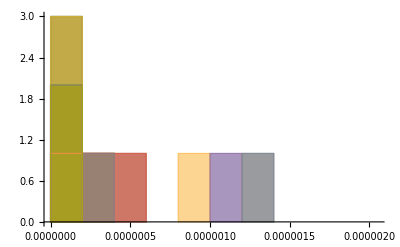

```mathematica
Histogram[Values[comparing]]
```

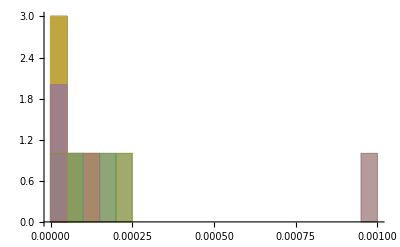

```mathematica
Histogram[Values[comparing]]
```

```mathematica
(*evaluated=(#/.{genSunrise4[__]->unk3L}/.repImaster/.mapGSR3TopK2)&/@mapped*)
```

```mathematica
mapped[[{-2}]]/.mapGSR3TopK2
```

<|loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→m^2 genSunrise3({1,-m^2},{2,-m^2},{2,-m^2,0})+IMaster(0,2,-m^2) IMaster(0,2,-m^2)|>

```mathematica
(mapped[[-2]]/.mapGSR3TopK2)//N
```

m^2 genSunrise3({1.,-1. m^2},{2.,-1. m^2},{2.,-1. m^2,0.})+(IMaster(0.,2.,-1. m^2))^2

```mathematica
List@@(mapped[[-4]]/.mapGSR3TopK2)/.applyAllMaps
```

{-(2 m^2)/(f4π^4 ϵ^2)+(m^2 (2 log(m^2/μb^2)-1))/(f4π^4 ϵ)+O(ϵ^0),-m^2/(64 π^4 ϵ^2)+(((log(m)-log(μb)) m^2)/(64 π^4)+(2 log(m) m^2-2 log(μb) m^2-m^2)/(128 π^4))/ϵ+(-((24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) m^2)/(3072 π^4)-((log(m)-log(μb)) (2 log(m) m^2-2 log(μb) m^2-m^2))/(128 π^4)-(24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2)/(3072 π^4))+O(ϵ^1)}

```mathematica
List@@(mapped[[-4]]/.mapGSR3TopK2)/.mapGSR3TopK2/.mapGSR3Higher/.mapGSR3/.repImaster
```

{-(2 m^2)/(f4π^4 ϵ^2)+(m^2 (2 log(m^2/μb^2)-1))/(f4π^4 ϵ)+O(ϵ^0),-m^2/(64 π^4 ϵ^2)+(((log(m)-log(μb)) m^2)/(64 π^4)+(2 log(m) m^2-2 log(μb) m^2-m^2)/(128 π^4))/ϵ+(-((24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) m^2)/(3072 π^4)-((log(m)-log(μb)) (2 log(m) m^2-2 log(μb) m^2-m^2))/(128 π^4)-(24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2)/(3072 π^4))+O(ϵ^1)}

```mathematica
Identity[List@@(mapped[[-4]]/.mapGSR3TopK2)/.mapGSR3Higher/.mapGSR3/.repImaster/.evalEntirely//N]
```

{-0.000320812/(ϵ+0.)^2+0.000284334/(ϵ+0.)+O((ϵ+0.)^0),-0.000641624/(ϵ+0.)^2+0.000568668/(ϵ+0.)-0.000596064+O((ϵ+0.)^1)}

```mathematica
evalCheck[[{-4}]]
```

<|loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{-(0.000962347-7.34468×10^-8 ⅈ)/(ϵ+0.)^2+(0.000852193+9.20995×10^-8 ⅈ)/(ϵ+0.)-(0.00128758+0.000492811 ⅈ)+(0.00182752+0.000313912 ⅈ) (ϵ+0.)+O((ϵ+0.)^2),-0.000962436/(ϵ+0.)^2+0.000853001/(ϵ+0.)+O((ϵ+0.)^0)}|>

```mathematica
0.000320812/0.0009623
```

0.33338

```mathematica
genSunrise3Evaluator[{1, -m1^2}, {1, -m^2}, {2, -m^2,mom}]/.evalEntirely//N
```

-0.000080203/(ϵ+0.)^2+0.0000710835/(ϵ+0.)+O((ϵ+0.)^0)

```mathematica
genSunrise3Evaluator[{3, -m^2}, {1, -m^2}, {1, -m^2,0}]/.evalEntirely//N
```

0.0000100254/(ϵ+0.)+O((ϵ+0.)^0)

```mathematica
m^2
```

```mathematica
mapGSR3Higher
```

genSunrise3({a_/;a≥1,-m1_^2},{b_/;b≥1,-m2_^2},{c_/;c≥1,-m3_^2,mom_}):>((1/(2 m1))^(a-1) (1/(2 m2))^(b-1) (1/(2 m3))^(c-1) (∂^((a-1)+(b-1)+(c-1)) genSunrise3Eval({1,-m1^2},{1,-m2^2},{1,-m3^2,mom}))/(∂m1^(a-1) ∂m2^(b-1) ∂m3^(c-1)))/((a-1)! (b-1)! (c-1)!)+(O(ϵ))^1/ϵ

```mathematica
genSunrise3[{2, -m^2}, {2, -m^2}, {1, -m^2,0}]/.mapGSR3Higher
```

O(ϵ^0)

```mathematica
D[genSunrise3Eval[{1,-m1^2}, {1, -m2^2}, {1, -m3^2,mom}],{m1,1}, {m2,1}]
```

0

```mathematica
/.mapGSR3TopK2(*/.mapGSR3Higher/.mapGSR3*)
```

```mathematica
genSunrise3Eval[{1,x}, {2,y},{3,z,p}]
```

genSunrise3Eval({1,x},{2,y},{3,z,p})

```mathematica
evaluatedWithEpsFor3L=(evaluated)/.{unknown3L[a_]->unknown3L[a]/ϵ^3+unknown3L[a]/ϵ^2+(unknown3L[a]+O[ϵ])/ϵ, unk3L->unk3L/ϵ^3+unk3L/ϵ^2+(unk3L+O[ϵ])/ϵ};
```

```mathematica
withHigherOrder =Normal[#]+hOϵ(*higher order in eps*)*ϵ^(#/.HoldPattern@SeriesData[x_,x0_,list_, nmin_, nmax_, den_]->nmax)&/@evaluatedWithEpsFor3L;
properReplacementRule = Dispatch@Normal[withHigherOrder, Association];
```

```mathematica
allDone =((#/.diag[{{0, b_,c_}}]:>ev@Series[b/.properReplacementRule,{ϵ,0,10}])&/@#)&/@allAnalysedDropBad;
```

```mathematica
Cases[Normal@Normal@Normal[allDone],loopIntegral[_,_],Infinity]/.properReplacementRule
```

{}

```mathematica
Length/@allDone
```

<|{ϕϕ,1}→1,{ϕϕ,2}→2,{ϕϕ,3}→5,{g,1}→1,{g,2}→3,{g,3}→14|>

```mathematica
justEvals =FullSimplify[Total[#/.fullContrib[num_,b_,c_,ev[d_]]->num*d],{m>0,μb>0}]&/@allDone[[{1,2,3,4,5,6}]];
```

```mathematica
justEvals =FullSimplify[Total[#/.fullContrib[num_,b_,c_,ev[d_]]->num*d],{m>0,μb>0}]&/@allDone[[{1,2,4,5}]];
```

```mathematica
Print["NB, we have no dZ and dg on g and h at present."]
```

NB, we have no dZ and dg on g and h at present.

```mathematica
simpled=FullSimplify[#/.π->f4π/4/.f4π->1/Λ^(1/2)]&/@justEvals;
```

```mathematica
drophigher = Normal[#/.hOϵ->hOϵ+O[ϵ]]&/@ simpled;
```

```mathematica
tree = <|{ϕϕ,0}-> ct I (dZϕ2 p^2-m^2 dZmϕ2), {g,0}-> -I g(*nb counterterms added in later*)|>;
drophigherAndTree =Merge[{drophigher, tree}, Total]
```

<|{ϕϕ,1}→1/2 g hOϵ ϵ^2 (ct dZmϕ2 m^2-ct dZϕ2+1)+1/2 ⅈ g Λ m^2 (2 (ct (dZmϕ2-2 dZϕ2)+1) log(μb/m)-ct dZϕ2+1)+1/768 ⅈ g m^2 ϵ (ct (dZmϕ2-2 (96 dZϕ2 Λ+dZϕ2))+384 Λ ((ct (dZmϕ2-2 dZϕ2)+1) log^2(m/μb)+ct dZϕ2 log(m/μb)+log(μb/m))+192 Λ+1)+(ⅈ g Λ m^2 (ct (dZmϕ2-2 dZϕ2)+1))/ϵ,{ϕϕ,2}→-1/384 ⅈ g^2 (64 hOϵ (ct m^2 (dZϕ2-3 dZmϕ2)+3 ct dZϕ2-1)+384 Λ^2 m^2 log(m/μb) (2 (ct (dZmϕ2-4 dZϕ2)+1) log(m/μb)+ct (dZmϕ2+2 dZϕ2)-1)+Λ m^2 (ct (-96 Λ (dZmϕ2+2 dZϕ2)+dZmϕ2-4 dZϕ2)+96 Λ+1))-(ⅈ g^2 Λ^2 (24 m^2 (-2 (ct dZmϕ2-4 ct dZϕ2+1) log(m/μb)-3 ct dZϕ2+1)+p^2 (3 ct dZϕ2-1)))/(12 ϵ)-(2 ⅈ g^2 Λ^2 m^2 (ct (dZmϕ2-4 dZϕ2)+1))/ϵ^2,{g,1}→1/16 ⅈ g^2 Λ ϵ (2 ct^2 (dZmϕ2-dZϕ2)^2+4 log(μb/m) (ct (dZmϕ2-dZϕ2) (ct dZmϕ2+5 ct dZϕ2-6)-6 (ct dZϕ2-1)^2 log(m/μb))+(ct dZϕ2-1)^2/(16 Λ))+3/2 g^2 hOϵ ϵ^2 (ct dZmϕ2 m^2-ct dZϕ2+1)^2+1/4 ⅈ g^2 Λ (ct (dZmϕ2-dZϕ2) (ct (dZmϕ2+5 dZϕ2)-6)+12 (ct dZϕ2-1)^2 log(μb/m))+(3 ⅈ g^2 Λ (ct dZϕ2-1)^2)/ϵ,{g,2}→-1/128 ⅈ g^3 (384 hOϵ (ct m^2 (dZϕ2-4 dZmϕ2)+4 ct dZϕ2-1)+Λ (96 Λ (2 ct (dZmϕ2+dZϕ2)-1)-4 ct dZϕ2+1)-384 Λ^2 (log(m)-log(μb)) (-2 ct dZmϕ2+(2-8 ct dZϕ2) log(μb)+(8 ct dZϕ2-2) log(m)+6 ct dZϕ2-1))+(3 ⅈ g^3 Λ^2 (6 ct dZmϕ2+(12-56 ct dZϕ2) log(m/μb)-4 ct dZϕ2-1))/(2 ϵ)+(3 ⅈ g^3 Λ^2 (14 ct dZϕ2-3))/ϵ^2,{ϕϕ,0}→ⅈ ct (dZϕ2 p^2-dZmϕ2 m^2),{g,0}→-ⅈ g|>

```mathematica
(*https://homepages.dias.ie/ydri/QFTNOTES5.pdf)*)
(*From this formula it is now obvious that subtracting−Nd/ϵ is precisely the above mod-ified minimal subtraction*)
fromPaperZ=1-gR^2((N+2)/144)Nd^2/ϵ
fromPaperZg =1+ (N+8)/6 gR Nd/ϵ+gR^2((N+8)^2/36 Nd^2/ϵ^2- (5N+22)/36 Nd^2/ϵ) 
fromPaperZm=1+ (N+2)/6 gR Nd/ϵ+gR^2(((N+2)(N+5))/36 Nd^2/ϵ^2- (N+2)/24 Nd^2/ϵ)
```

1-(gR^2 (N+2) Nd^2)/(144 ϵ)

gR^2 (((N+8)^2 Nd^2)/(36 ϵ^2)-((5 N+22) Nd^2)/(36 ϵ))+(gR (N+8) Nd)/(6 ϵ)+1

gR^2 (((N+2) (N+5) Nd^2)/(36 ϵ^2)-((N+2) Nd^2)/(24 ϵ))+(gR (N+2) Nd)/(6 ϵ)+1

```mathematica
getOur=(#/.{ Nd->(*2/((4π)^(4/2)Γ[2])*)2Λ,gR->a g,N->1})+O[a]^3&
ourZ=getOur[fromPaperZ]
ourZg=getOur[fromPaperZg]
ourZm=getOur[fromPaperZm]
```

(#1/.{Nd→2 Λ,gR→a g,N→1})+(O(a))^3&

1-(a^2 (g^2 Λ^2))/(12 ϵ)+O(a^3)

1+(3 a g Λ)/ϵ-(3 a^2 (g^2 Λ^2 (ϵ-3)))/ϵ^2+O(a^3)

1+(a g Λ)/ϵ-(a^2 (g^2 Λ^2 (ϵ-4)))/(2 ϵ^2)+O(a^3)

```mathematica
fromPaperBetagButOurs=-ϵ g/(1+ g D[Log[ourZg],g] - 2 g D[Log[ourZ],g])
```

-g ϵ+3 a g^2 Λ-17/3 a^2 (g^3 Λ^2)+O(a^3)

```mathematica
ourZg/ourZ^2//Simplify
```

1+(3 a g Λ)/ϵ-(a^2 (g^2 Λ^2 (17 ϵ-54)))/(6 ϵ^2)+O(a^3)

```mathematica
(*Matches!*)
```

```mathematica
additionalScalingRequired = {sc[g]->-Dminus4,sc[m2]->0}
scalingSolutions ={sc[g]->0-Dminus4, sc[m2]->-2}
```

{sc(g)→-Dminus4,sc(m2)→0}

{sc(g)→-Dminus4,sc(m2)→-2}

```mathematica
Clear[weinbergb]
```

```mathematica
(*C.f. WEinberg 18.6*)
weinbergb[l_, nu_Integer] := Coefficient[l counterTerms[ dZ[l]],Dminus4^-nu]
```

```mathematica
weinbergblnum[l_, nu_Integer,m_] := D[weinbergb[l,nu],m]
weinbergρ[l_]:=(sc[l]/.additionalScalingRequired)/Dminus4 (*Nb Dminus3 = - Epsilon!!!!!!!!!!!!!!*)
weinbergΔ[l_]:=sc[l]/.scalingSolutions/.Dminus4->0
sumOvercouplingConstants = Join[couplingConstants, {m2}]
```

{g,m2}

```mathematica
weinbergBetaFuncNoEps[l_]:=- weinbergΔ[l] l - weinbergb[l,1]*weinbergρ[l] + Sum[weinbergblnum[l,1,idxm] weinbergρ[idxm] idxm,{idxm, sumOvercouplingConstants}]
weinbergα[l_]:=-weinbergρ[l]l
weinbergBetaFunc[l_]:=Simplify[ weinbergBetaFuncNoEps[l] + Dminus4 weinbergα[l]]
```

```mathematica
ourBeta =Series[weinbergBetaFunc[g]/.ct->1,{a,0,5}]
```

Dminus4 g+3 a g^2 Λ-17/3 a^2 (g^3 Λ^2)+O(a^6)

```mathematica
ourBetam2 =Series[weinbergBetaFunc[m2]/.ct->1,{a,0,5}]
```

2 m2+a g Λ m2-5/6 a^2 (g^2 Λ^2 m2)+O(a^6)

```mathematica
-fromPaperBetagButOurs* D[Log[ourZm/ourZ],g]//Simplify
```

a g Λ-5/6 a^2 (g^2 Λ^2)+O(a^3)

```mathematica
fromPaperGammam =getOur[ (N+2)/6 Nd gR- 5(N+2)/72 gR^2 Nd^2]
```

a g Λ-5/6 a^2 (g^2 Λ^2)+O(a^3)